### Loading the McGowan and Saunders datasets and showing re-population after mass extinction

Ammonite data  is as reported in (Tendler, Mayo and Alon, 2015)

```mathematica
MC=Import["/Users/avimayo/Downloads/Mcgowan2004data.xlsx"][[1]];
SA=Import["/Users/avimayo/Downloads/Saunders2004data.xls"][[1]];
```

```mathematica
TableView/@{MC[[;;10]],SA[[;;10]]}
```

{GenusLMUspeciesSourceWDSAHVAVLGTVSPLURRIBBIFCONVGSDIameterRAngeSTRAT CODESFamilySUPERFAMILYP. C. IP. C. IIP. C. IIIP. C. IVP. C. VP. C. VIAAMorphotypesPC 1PC2PC3AcanthitiesUexcelsusArkell et al. (1957) Fig. 195 (5 a-b)2.4690.1640.6120.7120.4670.81.0.8160.40.1.0.1.92.Norian (L-M)8.TIBETITIDAECLYDONITACEAE1.31046863-0.67937950.602463030.16876754-0.46325080.218108580.335933923.-0.56046570.550471120.35089595AcrochordicerasMhyattiMeek 1877 fig 5a2.7350.2561.0.8530.6151.11.0.7210.0.72.3850.1.69.Anisian (M)5.ACROCOHORDICERATIDAECERATITACEAE3.027734391.744352870.83412738-0.641283-0.74557061.173097330.434746168.2.056565251.498359740.92529095AlanitesMlaevisGSC 282452.5880.1351.0670.80.5631.21.0.0.20.1.0.1.30.Anisian (M)5.KHVALYNITIDAEDINARITACEAE1.00373037-1.2150531-0.49060320.341665380.07597557-0.09204760.62702742.-0.70285730.31861107-0.7619301AlbanitesLwelteriC337042.2140.2950.9050.7780.6351.1.0.6830.0.31.0.1.51.Spathian4.NORITIDAEMEEKOCERATACEAE1.655205180.68897626-0.88400680.33439294-0.13574750.255832760.353278088.1.155180080.14620896-0.5885848AmarassitesUsemiplicatus1980/10/541.6650.1250.5570.4560.571.1.0.4210.0.61.0.1.71.Norian (M2)8.HALORITIDAETROPITACEAE0.41411369-0.03961720.37425491-0.40241761.447772390.401718850.33493553.-0.1305173-0.58575880.54032407Ambites*LfuliginatusGSC 281232.0.2210.4860.6420.7061.0.70.4140.50.1.0.0.979.Dienerian2.MEEKOCERATIDAEMEEKOCERATACEAE0.85079067-0.55551910.05923279-0.5186398-0.1777379-2.07367030.231633343.-0.46644820.156576810.34230854AmphipopanocerasMselwyniGSC 282612.0070.2650.70.6830.6861.1.0.0.40.11.0.1.58.Anisian (M)5.PARAPOPANOCERATIDAEMEGAPHYLLITACEAE0.64688083-0.5257051-0.4728877-0.13068780.68350155-0.579060.297004213.-0.2891655-0.4956649-0.3495553AnagymnotocerasMcolumbianumGSC 283032.0660.2611.3330.6980.4581.1.0.3610.70.1.8750.1.39.Anisian (M)5.CERATITIDAECERATITACEAE0.359899280.511385431.721157920.248383160.03648203-0.40781180.57175368.-0.2143937-0.7921581.34131576AnasibiritesLfreboldiC 271572.0190.2220.5240.6490.5711.1.0.5250.0.51.0.1.46.Smithian3.PRIONITIDAEMEEKOCERATACEAE1.311110990.21875198-0.2075928-0.0027590.446374210.553992640.249103813.0.445275290.21773369-0.1568409,NumberTaxonomyLevelDSW1.Anetoceras1 to 10.6060.534.792.Erbenoceras1 to 10.6090.534.193.Luofuceras1 to 10.7510.534.234.Ruanites1 to 10.7190.534.075.Mimosphinctes1 to 10.4550.552.216.Talenticeras1 to 10.4590.672.357.Lenzites1 to 10.4530.732.418.Teicherticeras1 to 10.3870.562.189.Convoluticeras1 to 10.4020.672.95}

#### Identifying the FF, DM and PT survivors

```mathematica
FFsurvivors={158,159,167,171,176};
DMsurvivors={208,209};
PTsurvivors={566,572};
```

```mathematica
Row[Framed@TableForm[SA[[#+1,;;3]]]&/@{FFsurvivors,DMsurvivors,PTsurvivors},Spacer[20]]
```

158. | Tornoceras | 2 to 4
159. | Aulatornoceras | 2 to 4
167. | Crassotornoceras | 3 to 4
171. | Linguatornoceras | 3 to 4
176. | Phoenixites | 2 to 4208. | Rectimitoceras | 4 to 5
209. | Mimitoceras | 4 to 5566. | Episageceras | 13 to 14
572. | Xenodiscus | 12 to 14

#### Plotting the series of mass extinction and re-populations

```mathematica
dictionary={"CLIONITITIDAE"->"CLIONITIDAE","DIDYAMITIDAE"->"DIDYMITIDAE","GYMINITIDAE"->"GYMNITIDAE","ISCULTIDAE"->"ISCULITIDAE","Juvavitidae"->"JUVAVITIDAE","NORTITDAE"->"NORITIDAE","OPHICERATiDAE"->"OPHICERATIDAE","PINACOCOCERATIDAE"->"PINACOCERATIDAE","SIBERITIDAE"->"SIBIRITIDAE","Sturiidae"->"STURIIDAE","THETITIDAE"->"THETIDITIDAE","USSURITIDAE"->"USSURIIDAE","Ussuriidae"->"USSURIIDAE","i.s"->"I.S."};
```

```mathematica
g=#[[1,1]]->#[[;;,2]]&/@GatherBy[SortBy[{ToExpression@StringSplit[#[[1]],"to"],#[[2;;]]}&/@SA[[2;;,{3,4,6}]],#[[1]]&],#[[1]]&];
```

```mathematica
grule = # -> Which[
      #[[2]] <= 4, "D",
      #[[1]] <= 4 && 5 <= #[[2]], "DM",
      5 <= #[[1]] && #[[2]] <= 7, "M",
      #[[1]] <= 7 && 8 <= #[[2]], "MP",
      8 <= #[[1]] && #[[2]] <= 10, "P",
      #[[1]] <= 10 && 11 <= #[[2]], "PP",
      11 <= #[[1]] && #[[2]] <= 13, "P",
      #[[1]] <= 13 && 14 <= #[[2]], "PT",
      #[[1]] <= 14, "T"] & /@ Select[g[[;; , 1]], #[[2]] >= 4 &];
```

```mathematica
G=#[[1,1]]->Join@@#[[;;,2]]&/@GatherBy[g/.grule,First];
G[[-1]]=("T"->Join[G[[-1,2]],MC[[2;;,{6,5}]]]);
```

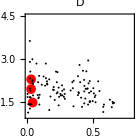
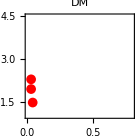
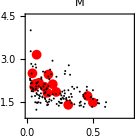
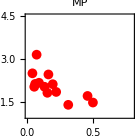
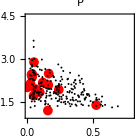
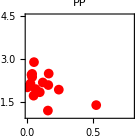
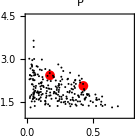
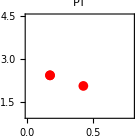
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Riffle[ListPlot[SortBy[#/.Select[G,StringQ@#[[1]]&],Length],PlotRange->{{0,.8},{1,4.5}},AspectRatio->1,Frame->True,PlotStyle->{{Red,PointSize[.05]},{Black,PointSize[.01]}},PlotLabel->#[[1]],FrameLabel->{"D","W"},ImageSize->140]&/@({{"D","DM"},{"DM"},{"M","MP"},{"MP"},{"P","PP"},{"PP"},{"P","PT"},{"PT"},{"T","PT"}}),Graphics[{Thickness[.2],Arrowheads[.75],Arrow[{{0,0},{1,0}}]},ImageSize->20]]]
```

#### Concentrating on the FF, DM and PT transitions

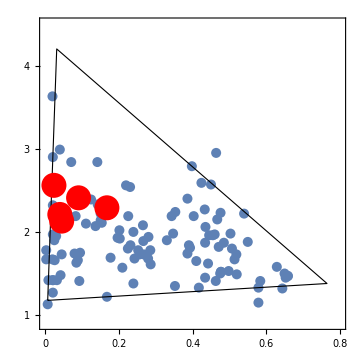
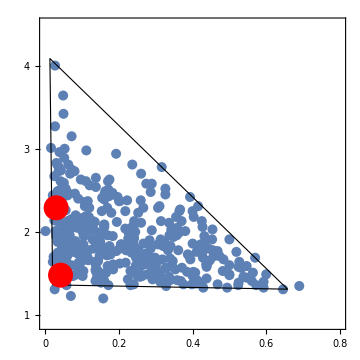
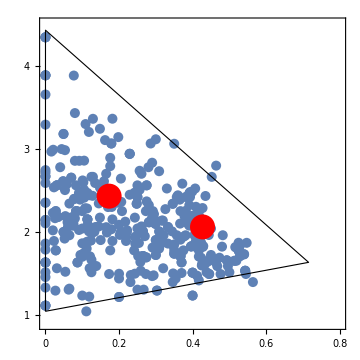

```mathematica
Row[Show/@({
Show[{
ListPlot[#,PlotStyle->PointSize[.02],PlotRange->{{0,.8},{.9,4.5}}],
Graphics[{FaceForm[],EdgeForm[Black],Triangle@Last@findTriangle[MeshCoordinates@ConvexHullMesh@Nest[Complement[#,MeshCoordinates@ConvexHullMesh@#]&,#,1]]}]},
Frame->{{True,False},{True,False}},FrameTicks->{{0,.2,.4,.6,.8},{1,2,3,4}},AspectRatio->1,ImageSize->Medium,FrameStyle->Directive[Black,20,"Helvetica"]]&/@Import["/Users/avimayo/Google Drive/SibSwap and Parti response/allAmmonitesDat.mat"][[1,1,2;;,;;,{1,3}]],
(ListPlot[#,PlotStyle->{Red,PointSize[.05],PlotRangePadding->None}]&@SA[[#+1,{-3,-1}]])&/@{FFsurvivors,DMsurvivors,PTsurvivors}}ᵀ),Spacer[50]]
```

### SibSwaping Ammonites data and calculating t-ratios

### Auxiliary Function

```mathematica
insideQ[{p1_,p2_,p3_},v_]:=(Det[{v,p3-p1}]-Det[{p1,p3-p1}])/Det[{p2-p1,p3-p1}]>0&&(Det[{p1,p2-p1}]-Det[{v,p2-p1}])/Det[{p2-p1,p3-p1}]>0&&(Det[{v,p3-p1}]-Det[{p1,p3-p1}]+Det[{p1,p2-p1}]-Det[{v,p2-p1}])/Det[{p2-p1,p3-p1}]<1
findTriangle[pts_]:=Module[{xmin,xmax,ymin,ymax,cpts},
cpts=pts;
{{xmin,xmax},{ymin,ymax}}=MinMax/@Transpose[cpts];
{Abs[1/2 (-p1y p2x+p1x p2y+p1y p3x-p2y p3x-p1x p3y+p2x p3y)],{{p1x,p1y},{p2x,p2y},{p3x,p3y}}}/.FindMinimum[{ 
(-p1y p2x+p1x p2y+p1y p3x-p2y p3x-p1x p3y+p2x p3y)^2,
(And@@(insideQ[{{p1x,p1y},{p2x,p2y},{p3x,p3y}},#]&/@cpts))&&
(And@@(0<#&/@Flatten[{{p1x,p1y},{p2x,p2y},{p3x,p3y}}]))},
{{p1x,xmin},{p1y,ymin},{p2x,xmax+ymax},{p2y,ymin},{p3x,xmin},{p3y,xmax+ymax}}][[2]]]
```

#### Concentrating on the McGowen datasets (for which phylogeny data is available)

```mathematica
AmmonitesData=Union[TakeDrop[#,4]&/@SortBy[MC[[2;;,{22,21,1,3,6,5}]],First][[3;;]]]/."OTOCERARTACEAE"->"OTOCERATACEAE"/.dictionary;
```

```mathematica
AmmonitesGraph=Graph[Union@@(Rule@@@Partition[Prepend[#,"Node 0"],2,1]&/@(AmmonitesData[[;;,1,1;;4]]))];
```

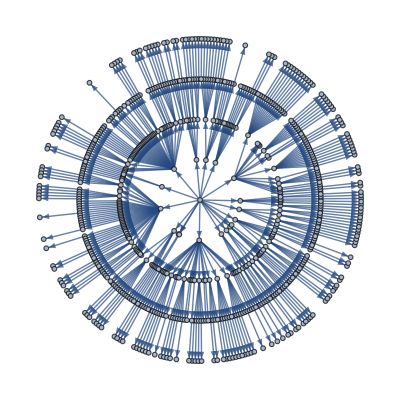

```mathematica
TreePlot[Graph[Union@@(Rule@@@Partition[Prepend[#,"Node 0"],2,1]&/@(Delete[AmmonitesData[[;;,1,1;;4]],Position[AMdata[[;;,1,1;;4]],Alternatives@@Select[{VertexInDegree[AmmonitesGraph],VertexList[AmmonitesGraph]}ᵀ,#[[1]]>1&][[;;,2]]]])),VertexLabels->Placed["Name",Tooltip]],Center]
```

#### Calculating t-ratios

```mathematica
RealTRatio=Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh@AmmonitesData[[;;,2]]
```

0.171665

Generating 10^3SibSwaped datasets at the various levels.

```mathematica
SibSwapAll=Table[Join@@((RandomSample/@(#ᵀ))ᵀ&/@GatherBy[AmmonitesData,#[[1,;;0]]&][[;;,;;,2]]),10^3];
SibSwapSuperFamily=Table[Join@@((RandomSample/@(#ᵀ))ᵀ&/@GatherBy[AmmonitesData,#[[1,;;1]]&][[;;,;;,2]]),10^3];
SibSwapFamily=Table[Join@@((RandomSample/@(#ᵀ))ᵀ&/@GatherBy[AmmonitesData,#[[1,;;2]]&][[;;,;;,2]]),10^3];
SibSwapGenus=Table[Join@@((RandomSample/@(#ᵀ))ᵀ&/@GatherBy[AmmonitesData,#[[1,;;3]]&][[;;,;;,2]]),10^3];
```

Calculating the t-ratio for each generated dataset

```mathematica
tvalsAll=ParallelMap[Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh[#]&,SibSwapAll];//Quiet
tvalsSuperFamily=ParallelMap[Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh[#]&,SibSwapSuperFamily];//Quiet
tvalsFamily=ParallelMap[Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh[#]&,SibSwapFamily];//Quiet
tvalsGenus=ParallelMap[Abs[1-(findTriangle[MeshCoordinates@#][[1]])/(RegionMeasure@#)]&@ConvexHullMesh[#]&,SibSwapGenus];//Quiet
```

#### Calculating p-vals

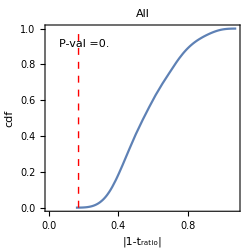
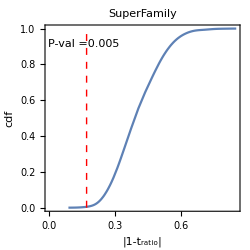
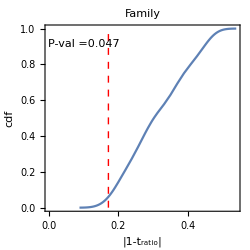
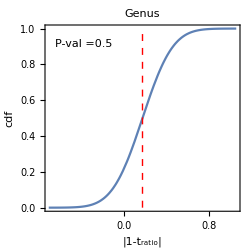

```mathematica
Row[MapIndexed[SmoothHistogram[#1,Automatic,"CDF",Epilog->{Red,Dashed,Line[{{RealTRatio,0},{RealTRatio,1}}],Black,Text["P-val ="<>ToString@Round[N@(Total@((Sign[RealTRatio-#]+1)/2))/10^3.,.001],Scaled@{.2,.9}]},Frame->True,ImageSize->250,FrameLabel->{"|1-t_ratio|","cdf"},PlotLabel->{"All","SuperFamily","Family","Genus"}[[#2[[1]]]],AspectRatio->1]&,(Select[#,#≤1&]&/@{tvalsAll,tvalsSuperFamily,tvalsFamily,tvalsGenus})],"       "]
```

### t-flipping algorithm generate outliers in the WD distributions

WDflipping data generated using the code of  Mikami and Iwasaki, 2021.

```mathematica
(WDflipping=Import["/Users/avimayo/Downloads/marginal_dist.csv"])//TableView
```

DWlogitDlogitWlogit_flipDlogit_flipWflipDflipW00.1983.1400000000000006-1.3987786044911446-0.76081050192003862.951391687196965-1.07579975905465290.95031922226141263.93232712616886110.1983.1400000000000006-1.3987786044911446-0.76081050192003862.52698472125861030.050279652222627870.92600203053147421.950953448270078820.1983.1400000000000006-1.3987786044911446-0.76081050192003862.52698472125861030.050279652222627870.92600203053147421.950953448270078830.1983.1400000000000006-1.3987786044911446-0.76081050192003863.954748567310472-0.53814080841682410.98118684768047812.71280944060183740.1983.1400000000000006-1.3987786044911446-0.76081050192003863.954748567310472-0.53814080841682410.98118684768047812.71280944060183750.1983.1400000000000006-1.3987786044911446-0.76081050192003862.6089505048330333-0.87060276089069320.93142540218800933.388340023730536660.1983.1400000000000006-1.3987786044911446-0.760810501920038613.0655285476260480.134412064644377380.99998788304254871.874219751200692470.1983.1400000000000006-1.3987786044911446-0.76081050192003863.6129704806226304-0.98034700667354820.97372675292335463.66537098646372780.1983.1400000000000006-1.3987786044911446-0.76081050192003862.0976786112971464-0.63431604432402430.89066734728794992.88572194322389490.1983.1400000000000006-1.3987786044911446-0.760810501920038613.065528547626048-0.054189018735252060.99998788304254872.055674127376066100.1983.1400000000000006-1.3987786044911446-0.760810501920038622.392391623448137-0.400930351775415860.99998999981158832.4932032652253318110.1983.1400000000000006-1.3987786044911446-0.760810501920038621.50011344062363-0.19159501520733090.99998999954014672.2111699081830576120.1983.1400000000000006-1.3987786044911446-0.76081050192003861.8876729139239279-1.23370792148361690.86847996993488934.433928734581136130.1983.1400000000000006-1.3987786044911446-0.76081050192003865.443923301641101-0.67735023008982310.99568611199683472.968644333867366140.1983.1400000000000006-1.3987786044911446-0.76081050192003862.5471849227747354-0.93508114612402250.92737416746310213.5474101626246974150.1983.1400000000000006-1.3987786044911446-0.7608105019200386-7.971158702076578-0.78470239669068810.000335159502681285833.1917445702509175160.1983.1400000000000006-1.3987786044911446-0.76081050192003863.292514447868623-1.54631416413528290.96416111760754965.69412644110302170.1983.1400000000000006-1.3987786044911446-0.76081050192003864.613887155151557-0.144240439544302850.990174097955232.155151821718969180.1983.1400000000000006-1.3987786044911446-0.76081050192003867.3895568705472880.33282145678788720.99937271167976361.716888180033675190.1983.1400000000000006-1.3987786044911446-0.76081050192003867.0959911290239290.33282145678788720.99916226640901981.716888180033675200.1983.1400000000000006-1.3987786044911446-0.76081050192003867.3895568705472880.98502474911787640.99937271167976361.373419984759582210.1983.1400000000000006-1.3987786044911446-0.76081050192003866.256303358580439-0.71422160603113060.99807534885950183.0425861187966565220.1983.1400000000000006-1.3987786044911446-0.76081050192003865.3108554044757930.71368875021162850.99507655991989991.4898239855858644230.1983.1400000000000006-1.3987786044911446-0.76081050192003864.983519253951833-0.68749851504488850.99318668859076762.988724516398613240.1983.1400000000000006-1.3987786044911446-0.76081050192003864.983519253951833-0.68749851504488850.99318668859076762.988724516398613250.1983.1400000000000006-1.3987786044911446-0.76081050192003864.983519253951833-0.68749851504488850.99318668859076762.988724516398613260.1983.1400000000000006-1.3987786044911446-0.76081050192003865.845893008374455-0.06551237723472420.99710658691198652.0676959524789047270.1983.1400000000000006-1.3987786044911446-0.76081050192003865.845893008374455-0.06551237723472420.99710658691198652.0676959524789047280.1983.1400000000000006-1.3987786044911446-0.76081050192003866.2975525453871680.225694919915816970.9981525777813081.7979515066984109290.1983.1400000000000006-1.3987786044911446-0.76081050192003866.2975525453871660.225694919915816920.9981525777813081.7979515066984109300.1983.1400000000000006-1.3987786044911446-0.76081050192003866.2975525453871660.225694919915816920.9981525777813081.7979515066984109310.1983.1400000000000006-1.3987786044911446-0.76081050192003866.618529445977208-0.22848869775238950.99865638762663562.2566893215247275320.1983.1400000000000006-1.3987786044911446-0.76081050192003865.97657564479712460.67987853758402330.99745892187718711.5066685310266987330.1983.1400000000000006-1.3987786044911446-0.76081050192003865.9039531232913090.42408034027889520.99726878836591731.654361307423623340.1983.1400000000000006-1.3987786044911446-0.76081050192003865.9039531232913090.42408034027889520.99726878836591731.654361307423623350.1983.1400000000000006-1.3987786044911446-0.76081050192003865.121974850002516-0.55285805098125250.99406112837869142.738203829104735360.1983.1400000000000006-1.3987786044911446-0.76081050192003863.1831865001525443-0.100568230897649990.96018662984024372.1057890887945856370.1983.1400000000000006-1.3987786044911446-0.76081050192003865.121974850002516-0.100568230897650020.99406112837869142.1057890887945856380.1983.1400000000000006-1.3987786044911446-0.76081050192003864.1118509990132050.247002073798551770.98387646645474381.781129073604617390.1983.1400000000000006-1.3987786044911446-0.76081050192003864.5192339482235830.134505995114808960.98921010407707791.8741376382454116400.1983.1400000000000006-1.3987786044911446-0.76081050192003865.8152254235432820.117489240227277160.99701705666450381.8891400787477426410.1983.1400000000000006-1.3987786044911446-0.76081050192003865.8152254235432820.398100699289394730.99701705666450381.6715843951784395420.1983.1400000000000006-1.3987786044911446-0.76081050192003865.9259550315073430.117489240227277110.99732784872382641.8891400787477426430.1983.1400000000000006-1.3987786044911446-0.76081050192003865.925955031507343-0.163122218834840460.99732784872382642.177170554532563440.1983.1400000000000006-1.3987786044911446-0.76081050192003866.187719192564153-0.163122218834840460.99793970499703432.177170554532563450.1983.1400000000000006-1.3987786044911446-0.76081050192003865.925955031507343-0.63400045317824030.99732784872382642.8851269168167617460.1983.1400000000000006-1.3987786044911446-0.76081050192003865.345412382589223-0.21774227992769660.99524266098845262.243256611565832470.1983.1400000000000006-1.3987786044911446-0.76081050192003865.345412382589223-0.21774227992769660.99524266098845262.243256611565832480.1983.1400000000000006-1.3987786044911446-0.76081050192003864.8111971242476290.57399114945771170.99191758269902311.5632628403700368490.1983.1400000000000006-1.3987786044911446-0.76081050192003864.8046120947120490.151756430136785830.99186468353084561.8591875298815237500.1983.1400000000000006-1.3987786044911446-0.76081050192003864.622300481540916-0.53013835152549760.99025553536799842.6991573747556696510.1983.1400000000000006-1.3987786044911446-0.760810501920038613.651532829804328-0.61261427483397430.99998882181331382.8452390869076947520.1983.1400000000000006-1.3987786044911446-0.76081050192003867.390604180936931-1.01631170791202590.99937335743536773.762975251064537530.1983.1400000000000006-1.3987786044911446-0.76081050192003867.135546993321892-0.336453558967101940.99919434347503982.399963851528441540.1983.1400000000000006-1.3987786044911446-0.76081050192003867.1149445044883410.217412420497791970.99917779439368911.8045880681325006550.1983.1400000000000006-1.3987786044911446-0.76081050192003867.209167811995434-0.88819349171968890.99925077432964493.4307245405084745560.1983.1400000000000006-1.3987786044911446-0.76081050192003865.0394410151630690.17095924174750740.99355431822253791.8428459261061896570.1983.1400000000000006-1.3987786044911446-0.76081050192003864.754800171454855-0.122835063521378180.99145323867991972.130687912234838580.1983.1400000000000006-1.3987786044911446-0.76081050192003864.5668879882658056-0.207795750057434860.98970660298600912.2309517200098528590.1983.1400000000000006-1.3987786044911446-0.76081050192003865.056894725226473-0.182478209164344230.99366496586244472.2001779975692153600.1983.1400000000000006-1.3987786044911446-0.76081050192003865.2583013768979540.44827468756510410.99481280574597371.6387192089614389610.1983.1400000000000006-1.3987786044911446-0.76081050192003867.52819792522671-0.062939473187430320.99945258260155612.0649523785022463620.1983.1400000000000006-1.3987786044911446-0.76081050192003866.1065850602019990.13277201685488910.99776680677819471.8756547061473585630.1983.1400000000000006-1.3987786044911446-0.76081050192003866.1065850602019990.13277201685488910.99776680677819471.8756547061473585640.1983.1400000000000006-1.3987786044911446-0.76081050192003865.316163077903246-0.11823844531474540.99510244264367292.1255024525447195650.1983.1400000000000006-1.3987786044911446-0.76081050192003865.316163077903246-0.11823844531474540.99510244264367292.1255024525447195660.1983.1400000000000006-1.3987786044911446-0.76081050192003866.898717068054974-0.36826385635698570.99898193803545132.4452133200302053670.1983.1400000000000006-1.3987786044911446-0.76081050192003868.06287445526367-0.417101208987846360.99967507921458832.51754609547941680.1983.1400000000000006-1.3987786044911446-0.76081050192003866.329244858301170.103416286151560760.9982097948169281.9017415086713287690.1983.1400000000000006-1.3987786044911446-0.76081050192003864.2349400342237650.29833570636090440.98571601842154081.7420421862898534700.1983.1400000000000006-1.3987786044911446-0.76081050192003865.8451484450229220.29633572569405780.99710444542608691.7435277613817737710.1983.1400000000000006-1.3987786044911446-0.76081050192003866.71786075351208-0.112762678979541150.99878233815123122.1193562522827705720.1983.1400000000000006-1.3987786044911446-0.76081050192003866.07706574670911250.191045225308424580.99770035390734051.8260852268949386730.1983.1400000000000006-1.3987786044911446-0.76081050192003866.07706574670911250.61500146058395570.99770035390734051.5406301056584757740.1983.1400000000000006-1.3987786044911446-0.76081050192003867.200457453892681-0.112762678979541180.99924431210748532.1193562522827705750.1983.1400000000000006-1.3987786044911446-0.76081050192003867.1662296841643180.071498758140706250.99921836708130811.930987433761959760.1983.1400000000000006-1.3987786044911446-0.76081050192003866.2285944373779550.487486903131349350.99802165997261241.6141579198476401770.1983.1400000000000006-1.3987786044911446-0.76081050192003866.3924953392022010.346174677423149830.99831872423507331.7073789114416609780.1983.1400000000000006-1.3987786044911446-0.76081050192003867.0707843217967970.46784009875411820.99914115463634331.6263436703828063790.1983.1400000000000006-1.3987786044911446-0.76081050192003865.8049941485684720.53729237709403820.99698657535348181.5843182529481217800.1983.1400000000000006-1.3987786044911446-0.76081050192003866.1153360470176160.51759955419076640.99778613434528051.595939376554774810.1983.1400000000000006-1.3987786044911446-0.76081050192003866.1779392291143930.215942181608909930.99791959653243411.805771889539077820.1983.1400000000000006-1.3987786044911446-0.76081050192003866.555923156692288-0.69614315504798410.99857034843879643.0059909338097475830.1983.1400000000000006-1.3987786044911446-0.76081050192003866.575271344255492-0.71515071764211120.99859751422331043.0444848004741845840.1983.1400000000000006-1.3987786044911446-0.76081050192003866.882241445114664-0.209035430256477920.99896520917603252.2324786651462025850.1983.1400000000000006-1.3987786044911446-0.76081050192003865.9269892422323770.00116889325159388880.99733059320784961.9988217896380223860.1983.1400000000000006-1.3987786044911446-0.76081050192003864.371359781933721-0.241841328466732790.98751357839556032.2735820939726445870.1983.1400000000000006-1.3987786044911446-0.76081050192003865.0327899437959240.92104606945907370.99351164960549311.3980923804527519880.1983.1400000000000006-1.3987786044911446-0.76081050192003865.032789943795924-0.241841328466732760.99351164960549312.2735820939726445890.1983.1400000000000006-1.3987786044911446-0.76081050192003865.855716508958556-1.02125831583602890.99713469296901343.776676515254434900.1983.1400000000000006-1.3987786044911446-0.76081050192003865.855716508958556-1.02125831583602890.99713469296901343.776676515254434910.1983.1400000000000006-1.3987786044911446-0.76081050192003864.2122798874171560.10112149857864940.98539365044147621.9038132129787906920.1983.1400000000000006-1.3987786044911446-0.76081050192003863.1414652241345960.31005409600927580.95856110758209591.7333972807440943930.1983.1400000000000006-1.3987786044911446-0.76081050192003863.6407407399437064-0.141800252728219330.97442766918950152.1523364474877225940.1983.1400000000000006-1.3987786044911446-0.76081050192003864.007486737305421.4338490829007470.98213554998048391.2383795728242617950.1983.1400000000000006-1.3987786044911446-0.76081050192003864.007486737305421.4338490829007470.98213554998048391.2383795728242617960.1983.1400000000000006-1.3987786044911446-0.76081050192003862.80450940117431550.35677105909112480.94290901776327681.6999227226265645970.1983.1400000000000006-1.3987786044911446-0.76081050192003863.1790004168734950.187825814643857470.96002633309935391.8287490523516028980.1983.1400000000000006-1.3987786044911446-0.7608105019200386-2.43595086288294-0.60653409105479360.080462024729405532.8340536724876944990.1983.1400000000000006-1.3987786044911446-0.7608105019200386-1.38678251622326480.4622037785406190.199911906621515261.62988396798909021000.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.7378228503683899-1.1065224238050560.32347040978147794.0238145087273391010.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.29250731709084654-0.5569182997318410.57259985455982292.74527575681000521020.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.8301603116645233-0.9600603108805370.303601174184745973.61184399188711641030.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.68038843239758170.141196462458503370.66381538597632841.86830870291196721040.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.1654464739731285-0.81491974532146690.54125752833510633.25898437020763731050.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.7349822129612074-0.63395669897883540.93904957718704322.8850444359646531060.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.0852823074139721-0.205785880438761030.7474823087777972.228480132063831070.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.2095904861152802-0.61574706393691510.77021648226264012.8510289275789511080.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.0140667131190093-0.0490736395499257740.73380525698320382.0502876913416081090.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.17250618740662650.24646775837223560.54300991612526021.78154655978646351100.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-8.553030028182811.2751872688468710.000182922313829790381.27936864440567161110.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.96754996560944481.15799843901046030.7246208847159791.31410427096363171120.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.5881478192531543-1.13158767278685920.357049943330771454.1005652933912951130.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.79009494407833650.142870050750339870.31213828344602421.86685671025505331140.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.8401393631774244-0.248605440999395520.30149543331338142.282226015488671150.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.28082687666111020.13674581698004430.21739950374880631.87218189432845121160.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.2174389698573689-1.17690078583934140.77160254169365754.2442938134833341170.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.33487166659848-0.53618012271573940.08826578882068112.709454430151421180.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.8395852137536020.56598882135357060.86288964400134841.56778841787843311190.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.7736845924455132-1.29415478465362250.68430740557245424.6479014000626721200.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.83911853458434840.465477474544401250.6982695367272411.62782525825680341210.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-6.437533337778856-0.95789241006192390.00158779231139630983.60618788463498861220.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209814.669958685526271-0.055274295439925460.99070437423754962.05682045869782561230.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209813.1656415521480820.267282390651881750.95951063768141831.7654468830738221240.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-6.437533337778854-1.34635201519151470.00158779231139631264.8433693366892911250.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-7.489183653419115-0.323193491321306040.00054878677571142492.38152263962164051260.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-6.680997706192191-0.358605124986764330.00124295383711763522.4313214929236611270.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-7.00648450500709-0.20080831891784140.00089516792151549012.2223804402431731280.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-5.986355172452279-0.87136282412274370.0024965077563824873.39015601081392331290.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.2846348279274968-0.8049733027929750.78322769379844153.2366267860675911300.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.2846348279274968-0.8049733027929750.78322769379844153.2366267860675911310.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.8845168215173937-0.34776533697041470.292232657675371652.41588995138029761320.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.7279606147589202-0.39008437080826710.32563241591477212.47709541320305961330.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.78042273570199780.3736249058083170.68576121600840271.68822501637635061340.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.33319235191564645-1.09315625178916220.58252592189745493.98366646077286651350.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.7718331901215565-2.3811354774091890.68390731609405811.8171685551078111360.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.23102093266197066-1.46569027939490160.44249027289864295.3305214854734791370.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.3228366479278393-1.75540018768919070.58000540900196086.7857526697160841380.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.1268012270786762-0.75628780908452950.53164790036795663.1303432458320631390.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.18319456095161601-1.28967548934788740.54566098416389364.6315978690771511400.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.4687361485009667-1.66423278089261070.3849054238978446.2816095354904961410.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.88451682151739370.395162356497315460.292232657675371651.67356067179588221420.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.5504661339210304-0.400978812499529940.17500895414067432.4932756291748121430.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.273939094766561-0.525349062981070.218573689766347832.69103902798301631440.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.5782690199515557-0.69486839174541140.359320989334319333.0034353866393441450.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.8839661302058994-0.57219115891845150.052941889937952052.77213585353769831460.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.3404547413082324-0.9406725487332720.2074252864643813.5616937096868851470.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.8998579563964753-0.87394674322442880.28906968825380363.3963399924389031480.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.23193385024183977-1.49463992905102750.442265073645688575.4577211643476811490.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.6547602540027595-1.913795762327780.341907628145435577.778760628815951500.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.5193208737227271-1.55495758440376490.37300104983173655.7348756879005811510.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.12989860047356006-1.27611640733674440.46756093677504484.58268892962671520.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.5193208737227271-1.5549575844037650.37300104983173655.7348756879005811530.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.8519148734384774-2.3812825384133740.299021323458436711.8187594572255371540.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.3713339919664638-2.1600799852594620.202394405457993929.6718212493970541550.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.2427938345682572-2.7205192737841850.439587969412743916.188197035336481560.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.1600378945165324-1.8829886023035210.238650399594112727.5731099782091231570.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.6060729204396442-1.41343957170834590.35294553745675835.1100579931152441580.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.6988147017907274-1.8423354356707780.33206507607224457.3112506059369841590.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-6.078650894655910.380736166596719940.00227602783032800941.6833481585471600.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-6.078650894655910.380736166596719940.00227602783032800941.6833481585471610.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-6.078650894655910.380736166596719940.00227602783032800941.6833481585471620.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.9923200114566004-0.23340648916530710.87997836733162022.2628847280290431630.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.9923200114566004-0.23340648916530710.87997836733162022.2628847280290431640.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.9923200114566004-0.23340648916530710.87997836733162022.2628847280290431650.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.9923200114566004-0.54355908648447420.87997836733162022.72211516033302741660.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.9923200114566004-0.54355908648447420.87997836733162022.72211516033302741670.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209815.3161540495363635-0.33832872898650920.99510239873248722.40259150339982731680.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209815.3161540495363635-0.33832872898650920.99510239873248722.40259150339982731690.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.850262532210907-0.313818905392818150.0546577481787834452.36863186044345041700.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.850262532210907-0.313818905392818150.0546577481787834452.36863186044345041710.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.850262532210907-0.313818905392818150.0546577481787834452.36863186044345041720.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209815.9112949108011520.53237776841453670.9972886399918481.58719706597706871730.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209816.9591629288743010.78239507111083440.99904101006886241.4572994100537111740.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209816.6984229957913921.00084316431674950.9987586634715551.36755938908457741750.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209816.6984229957913921.00084316431674950.9987586634715551.36755938908457741760.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.7232085515541030.68768679000876710.99954775692890611.50272766282756161770.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.7232085515541030.68768679000876710.99954775692890611.50272766282756161780.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.7232085515541030.68768679000876710.99954775692890611.50272766282756161790.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209818.7547658235872050.233718832774090220.99983231694475581.79157435218553961800.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.9665849064063160.233718832774090220.99964325874111911.79157435218553961810.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209818.7547658235872050.106708223410025170.99983231694475581.89877787999824891820.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209816.3050468172677210.209683547289930330.99816627143390481.8108307981427381830.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209814.9850611197515090.38288140267306740.9931970990999621.6818837652684641840.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209814.9850611197515090.38288140267306740.9931970990999621.6818837652684641850.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209818.2675441567842-0.243531436307046380.99973335091620042.27573642196653261860.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.495823959752375-0.057542625748623290.99943490939454932.0592204201820841870.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.495823959752375-0.057542625748623290.99943490939454932.0592204201820841880.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.2659595900164830.065788314012160730.99929155790106551.93631905105431361890.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.2659595900164830.065788314012160730.99929155790106551.93631905105431361900.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.8703569523277120.179180040801920070.99960824777193881.83594537977066151910.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.8703569523277120.34857352200687550.99960824777193881.70568402907531411920.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.8703569523277120.179180040801920070.99960824777193881.83594537977066151930.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.76390501398857951.55239528284565290.99956538586466211.21173018828379121940.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.76390501398857951.55239528284565290.99956538586466211.21173018828379121950.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.9546175413143954-0.60974555629878560.9504712731460362.83995317217588151960.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.795262838535552-0.62876341142930540.94240929936675492.8752801824655761970.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.293878844047643-0.213586678821624350.90835881710877362.23810081160331231980.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.64429636266094150.188754862208552140.93364857848076941.8279794533247031990.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.850413838096692-0.281244600408132430.94533007065929442.3247676054511692000.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.44531540055523560.24413663392045460.92020819948525811.78337059058883022010.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.8181097448884205-0.21670677370753070.94363663132619882.2419698675869062020.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.1572382447403835-0.121652584571305890.89633322894426732.12935167594607132030.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.4099130849977297-0.15544961798493020.80374223449477722.1681730791671012040.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.04924501507165324-0.41303059889371170.51229876639855332.5113812721273412050.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.66903695978425140.460856721295770650.93516467346454851.6307330429700672060.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.751276061967771-0.127522123077116470.9399753765713972.13599999999999972070.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.7056544137661687-0.50802771326232720.84626179182715282.6622080.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.10468921031492018-0.223151551282209760.5261384250804922.24999999999999962090.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.239477750862910.92379380969530530.096250965086924321.3972100.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.1046892103149204-0.223151551282209760.5261384250804922.24999999999999962110.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.5521565278943-3.54717369424171560.0722717414199266535.7150533214841062120.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.3305512212695008-0.183931145818821970.209058201369403922.2019230621302912130.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.126559448932900720.371113815004173450.53158769768653871.68995540867389552140.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.22851992825127287-0.154354401867524140.44310734355144822.1668943665918452150.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.8061052931369266-0.38238039600172760.1410994954171182.4657595519741842160.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.330551221269501-0.53013599457853840.209058201369403872.6991533699130122170.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.3566366406434582-0.65005416774378880.204777480090804542.9156345923490262180.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.138691131560083-0.38896859311910090.105382732597211252.47544821106505042190.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.138691131560083-0.18430508319345430.105382732597211252.2023725938671492200.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-3.6412020689832234-0.38896859311910090.0255408421272372252.47544821106505042210.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.152228427688969-0.0262712728442758840.104113168509003282.02660940466882572220.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.99346112382986050.0111280735683512160.119881173358903331.98892361440750332230.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.9676921049624463-0.35098383189232580.122626993588046612.4204543595058222240.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.4486226403071413-0.305663284765108730.389678295519218072.3575151301900072250.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.5283254561598291-0.25720466135753560.62908246659175262.29329979021261782260.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.8005929713576615-0.0044217577579105380.69009130915995382.0044215481536792270.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.5792130623322502-0.43931755839070710.1708969604601072.55163794798462672280.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.1876556876898734-0.54944424100946640.100854502403002322.732280014543512290.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.5994938402736019-1.0228438219785060.16804236955788283.7810824606838912300.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.59949384027360190.27786297882269010.16804236955788281.75739059432576622310.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.98087195385556550.61744035568928950.121215917794617731.53931314776491332320.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.59949384027360190.97052070327489530.16804236955788281.37887569970583472330.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.219181542675595-0.101997342546638060.098031155925324992.1073705289119142340.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.881176294414704-0.30581877136865870.292924081119319832.35772622357240462350.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.2406432241944536-0.22519834720100490.096149622675076552.2525611355332022360.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209813.29993715921967960.063393079823685970.96441665485619121.93856446648343922370.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209813.2167958777635195-0.218220040714888650.96145146653215792.2438507375146032380.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.736630955988867-0.55101317707097330.93914386101626792.73499999999999942390.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.2774736046156790.166167360142423920.90698414989512061.84689448427298022400.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.4672635928002960.081476591744345540.92180477321987771.9217442862613372410.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209814.223924259197808-0.271539327181173960.98556019167953572.3119724674141182420.082999999999999992.2499999999999996-2.4021354846046505-0.2231515512822098113.334704239513385-0.289328755718199440.99998838262461762.3355207197250622430.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.5846620497186716-0.72416608138710970.92985790803174913.06299999999999932440.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209813.4275915370460592-1.03181876063281350.96854579961673453.80615493858825052450.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.1544753464990056-0.465083439257179930.89607624116636092.59213703091048452460.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209813.2564846659444697-1.3111558121957980.96289543215078694.7104498294826732470.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209813.253363495799665-1.19362272454088460.96278378723025094.2990009932576752480.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209813.420792695463813-1.03803170057650450.96833807682169573.82364374501927972490.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209813.0763574583758535-0.85507154502892240.95589691022659163.35153261574109032500.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209813.119164231968079-1.13372523547273740.95766636547501564.1072000560274432510.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.11859052516176460.150811261895210440.470377066226739861.862520.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.8514841172423717-0.83160827720205610.70086837723426393.29700000000000062530.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.50686214021177170.92379380969530530.18139428946289061.3972540.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.53749201516566610.125551885171138470.82308984221398911.88199999999999972550.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.42295334086726390.57445788901084590.80579098961270071.56300000000000022560.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.244681516302979520.141552043650822520.56085701083785941.86800000000000032570.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.86336647954058011.52321434568548280.70335352819972861.2182580.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.86336647954058011.52321434568548280.70335352819972861.2182590.082999999999999992.2499999999999996-2.4021354846046505-0.2231515512822098110.7307386408980320.019446341279662520.99996813799814281.98073151911168482600.082999999999999992.2499999999999996-2.4021354846046505-0.2231515512822098110.522817440510650.080470539720230080.99996308547233941.92267208565574072610.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.58117923788967470.368950287560441240.82936146199016921.6914497837486182620.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.58117923788967470.368950287560441240.82936146199016921.6914497837486182630.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.7901036864605198-0.79237311990885950.312136406357081453.20862155952479672640.082999999999999992.2499999999999996-2.4021354846046505-0.2231515512822098110.626778040704341-0.83400367796178950.99996574292663783.3025088548225042650.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.698029212620488-0.273431140376516830.93690025207886632.31445684240376842660.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209811.11570132772372550.0074602140863306850.75318048659126751.99255754424019822670.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.5960565729923970.37960046690433270.35523640506095891.6841246890667242680.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209810.18701175121465452-0.050578168590295040.54660715358694412.05186908404658432690.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.8665994718480454-0.2359052082879230.9461604149695042.2660442930246362700.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209812.0751523805703127-0.192292446459358580.88845456090700662.21201491753656662710.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.74192802375369990.251015901415913350.3225726820063781.7782720.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.3753544668890153-0.58612417261621130.40723782997749162.7972730.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.8488327822183397-0.43370282965444150.135999999999999982.54295027794118232740.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.13215199154789492-1.02034945664574120.46699999999999993.7741540446554262750.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-11.454293086559469-2.50271241589247766.037410447947558e-713.2155728060006532760.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-11.454293086559469-2.50271241589247766.037410447947558e-713.2155728060006532770.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.292079494693774-0.78851235993040580.091771061661546173.2001110023730072780.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.292079494693774-0.78851235993040580.091771061661546173.2001110023730072790.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.292079494693774-1.64561238791144150.091771061661546176.1841736664713782800.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.2920794946937740.068587668050630550.091771061661546171.93370159983950152810.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.292079494693774-1.64561238791144170.091771061661546176.1841736664713792820.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-2.292079494693774-1.64561238791144170.091771061661546176.1841736664713792830.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-13.272821045670348-2.075740909277756-8.279374664904161e-68.970439651994562840.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-13.272821045670348-2.075740909277756-8.279374664904161e-68.970439651994562850.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-10.32121699837443-0.58199680816562480.000022925934605319442.7895983699283812860.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-10.32121699837443-1.12310350637390320.000022925934605319444.0743707730865832870.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.20455076687568-0.44737572796154130.230656649831902572.56419190328243872880.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.204550766875680.481847149802125230.230656649831902571.61763146116956772890.082999999999999992.2499999999999996-2.4021354846046505-0.223151551282209817.342885509723008-0.44737572796154130.9993432381927422.56419190328243872900.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.916088210500758-0.0196280259349790320.128288417025842432.01981192215834462910.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.916088210500758-0.0196280259349790320.128288417025842432.01981192215834462920.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.9518764168979583-0.87822540097547840.278497615996215533.40661512011012272930.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.908744227617605-0.53382809218959580.287246875837866572.70543844234269232940.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.42174612322816973-0.87822540097547840.396088993775399743.40661512011012272950.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.45452404984488515-0.4237997580889450.388275672623214162.52774564244347082960.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-0.42174612322816973-0.87822540097547840.396088993775399743.40661512011012272970.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.723596613929784-0.29153275216000790.15139847689790062.338467470800862980.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.9408647106919508-0.207796508514665470.125542889737268352.2309526536420242990.082999999999999992.2499999999999996-2.4021354846046505-0.22315155128220981-1.708937758131107-0.65078909535537720.153291544179569472.91704296991832423000.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.40979787055517260.040811577907841510.19625593944294081.963010.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.06182863542196959-0.63658212006284520.51544223662712912.89000000000000153020.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.29249812051647306-0.294913363529760550.57259760390082292.3433030.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.37542598563816265-0.36667517577731110.407220565678034052.44291914464684373040.27400000000000011.6940000000000002-0.97437163855278920.365268909357242161.0873808901885935-0.438815255107681550.74787820538257022.5508587458405353050.27400000000000011.6940000000000002-0.97437163855278920.365268909357242161.1859754045211228-0.140639817799310920.76601049595272692.1513060.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.009690227737525980.74714138533411150.50241253797794781.47370879855036363070.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.009690227737525980.74714138533411150.50241253797794781.47370879855036363080.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.97111819293909530.74714138533411150.274647678752530661.47370879855036363090.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.0096902277375259250.59950850589160760.50241253797794781.54907144007788673100.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.44306871210794331.18413749782516440.391000000000000071.30600000000000033110.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.0985589560458648-0.378443285011857140.250000000000000062.463120.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.4430687121079434-0.378443285011857140.3912.463130.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.6612342004396774-1.18304940591099550.34045242005957714.2643032572242373140.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.6612342004396774-1.18304940591099550.34045242005957714.2643032572242373150.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.8825985743876987-0.50802771326232740.132080680956295082.6623160.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.3090410919147510.251015901415913230.090366944574209811.7783170.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.175309335226499-0.350663913841893940.101979734359155442.42000000000000043180.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.2784112186880088-0.350663913841893940.092916787131886862.42000000000000043190.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.59490021808732560.298906850081127550.35550130829704751.74161848885115943200.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.549979937073694-0.053028945787124720.365859063753974262.0544501668571373210.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.9034663548327990.351344379102637550.28832868160231811.70373135830257353220.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-3.1873790480719180.272207953674448560.039633443707159311.76168584716879883230.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.179787831363175-0.0274746799750025250.98491886108224112.027845589448553240.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.42007012672692360.301080108110680260.96831592253652311.7400084888891673250.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-6.485877391763967-1.02196439870599230.0015125007698741653.7786377783637743260.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.273312226282094-0.146654048819978230.98624598150719832.1579432984186563270.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.3427082195949560.0230968682131197920.41514176850968631.9771578226876243280.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.3427082195949560.0230968682131197920.41514176850968631.9771578226876243290.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.33201321758443325-0.092442360954487380.417740857088295672.0968399183558943300.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.116262220007087-0.129664828343147020.107516238258166492.1384367442893783310.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.58309672623001150.40349620055283720.358210348711671731.66797056475102943320.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.5239524221849283-0.53879239804427780.17887024233118452.71392585966707543330.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.7264237304228103-0.40999867408407810.32597000523986962.50680578720048563340.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.0352425224593866-0.89072819391253010.115542056622773593.4368935436685953350.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.5254598762188565-0.34609980871662210.17864893148774022.41353369275906943360.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.40784533504122233-0.46677928898869820.60056111825519042.59483936375296683370.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.8055985277489903-1.07316473777605160.308819214987117063.92461052661230043380.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.8402476769741614-0.67335400379181380.69850737707169912.96079284426020453390.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.45602955487516494-1.07881439052039130.387918145404108963.94118037988130573400.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.6373478634579741-0.370213797583321070.345836304291304352.4480341699151333410.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.124162138978376-0.70793925114435420.245230065903294663.02979402938387653420.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.31888349527660687-0.4387579782960890.42093787268085282.55076991956744163430.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.54728495836085370.223131051392333750.63349545149938561.80000000000000053440.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.23351972226551665-0.26160243588823850.441873925919727742.2993450.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.71833565723371430.223131051392333750.32774958778890281.80000000000000053460.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.30091621247456590.62921509326621240.57465647727541481.53300000000000013470.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.4567011911256307-0.125274788484807660.61222131583075612.13344987199851533480.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.489486241706698-0.04355437483431490.076588528185452172.04450678819523063490.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.640298799717834-0.36534425661856630.345168998432791532.44100000000000033500.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.8131629732771177-0.64817808366465220.0566070044873031662.912044051159753510.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.246402408554083-1.43588803232125220.22331352034653115.2033660857067673520.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.8573690964022573-0.462481660034335940.135000000000000042.58800000000000053530.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.72946065398283940.225372999884815540.15064658101488581.79820842784319783540.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.203312798510286270.177575877803261450.44933616625074551.83728746463305483550.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.09438908283026170.379348349687573140.476410233292705761.68429719294510523560.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.09182816746305990.221215032958385740.25126417888501611.8015343033146753570.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.57192564636820140.118755964513797330.360782610836377361.88801448380836463580.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.41819814600691350.47591493173167210.194934212871006261.62130633430405663590.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.56512718654272450.71261621442876740.172902159741111281.49034963189991793600.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.69154251368276860.433207288626204670.3336800212903931.64841606652451643610.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.18518756897630234-0.200303125344010870.54615503394336162.22176305241136343620.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.008987339194340277-0.053854480552183530.49774318032478762.0553210197934773630.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.21717594115391572-0.108968127697237460.44590841273080222.1151168081157983640.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.193129053240247320.17794413504335170.451857251706937361.83697918054700133650.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.095318717886477670.36339930406021190.52380165348944651.69529873845803913660.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.428338146937966350.320626026269653750.394513236477130441.72568459096324233670.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.65074267788645110.25278404894739210.65716780391685011.77662557898667163680.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.05488494685924067-0.110768148637911290.486272206686987952.1171258673538043690.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.30710179897001927-0.110768148637911290.5761676859630722.1171258673538043700.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.05488494685924061-0.43704937242658790.486272206686987952.54812251022818843710.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.416871692688500550.037118080271535310.39725556840129981.96355235092729943720.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.43658816163548790.5632035010312810.19206424737392481.5693721228897243730.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.43658816163548790.5632035010312810.19206424737392481.5693721228897243740.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-0.28903183154057590.168132700915740370.42823090724138521.84523166289948563750.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.3055525736587993-0.269933993353560160.57578932527437622.3098679872265133760.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.3055525736587993-0.269933993353560160.57578932527437622.3098679872265133770.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.3055525736587993-0.269933993353560160.57578932527437622.3098679872265133780.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.6200409509094564-0.117453912594627290.16518922263716692.124619797479963790.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.6200409509094564-0.117453912594627290.16518922263716692.124619797479963800.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.6200409509094564-0.117453912594627290.16518922263716692.124619797479963810.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-3.2650370093083962-0.145721077167409730.03678029689291242.1568634646217213820.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-3.2273917388155553-0.0500738501720208450.038137835695582052.0513387357941393830.27400000000000011.6940000000000002-0.97437163855278920.365268909357242160.2490894348928656-0.32280057898059470.56194236710436442.38097992502505073840.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.6121225191552444-0.103016450491222970.16628413820993412.1084996444541933850.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.3649173765042715-0.122001799011122620.08587734080822112.1297461342223423860.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.3649173765042715-0.122001799011122620.08587734080822112.1297461342223423870.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.3609043276018940.0317443781526754450.086192932152051261.96874418516588563880.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-1.03483717101396480.58997378400329810.262137392970362761.55433181716726553890.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.140199326702811-1.22852399438069580.99919803361233044.4161735071689533900.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.7260571398631654-0.98810872526607360.99674068717406143.6861394187210963910.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.7260571398631654-0.98810872526607360.99674068717406143.6861394187210963920.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.298293293811304-0.39968826462662160.98658052176384312.4913497155915783930.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.298293293811304-0.39968826462662160.98658052176384312.4913497155915783940.27400000000000011.6940000000000002-0.97437163855278920.3652689093572421614.836837120178744-1.07224113768782310.99998963988322413.9219105938568813950.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.380259077385729-0.067226312152752540.9876227501088272.06952750012141533960.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.99391240260263-0.30351302871942130.99965260285736922.35459923965076623970.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.4786205332771460.042517933630102480.9984564274767951.95836327825496033980.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-2.9739375337262723-0.00274792691942327140.0486072737156232962.00274170593129063990.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.460647359271311-0.140153923391502180.99575718978544772.1504408665285824000.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.352925542095819-0.349489259959587130.99825138362977712.4183329590303424010.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.647667712258675-0.58501327894859930.99049705137633942.79500482139119074020.27400000000000011.6940000000000002-0.97437163855278920.365268909357242168.203918099975848-1.1413709703423930.99971649527005374.1310480116995474030.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.544406091125041-0.88364005430819370.99946121837187483.41968150388269354040.27400000000000011.6940000000000002-0.97437163855278920.3652689093572421618.062749715976356-0.73326130487485930.99998998569633073.08184912557430524050.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.799076566031154-1.4948730723194540.99887643728363375.4587605755222534060.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.7627567989615-0.5741205172259190.97729727669007452.77555825832318134070.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.538426514357232-0.097058620893728910.99854532692974422.10191496755413534080.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.538426514357232-0.097058620893728910.99854532692974422.10191496755413534090.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.831992255880591-0.74926191322371820.99891245543952223.11542806339444134100.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.405173002390383-0.79596717853893030.99551682224040393.2165737926779654110.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.4597250482857370.63194317770382880.98855668962451451.53154788536018834120.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.471868348162285-0.97812479065697810.98869312921468663.65945451042400464130.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.471868348162285-0.97812479065697810.98869312921468663.65945451042400464140.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.471868348162285-0.97812479065697810.98869312921468663.65945451042400464150.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.334242102584907-0.35613865284681380.99518959059005392.4277955038377794160.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.882582565572195-0.35613865284681380.99246956593057312.4277955038377794170.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.334242102584907-0.064931355696272620.99518959059005392.0670757725101884180.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.0202088111495740.389252261971933740.98235727701169021.6775533249929414190.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.6992319105595320.84343587964014020.97584488737524111.4302197633446394200.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.0202088111495740.389252261971933860.98235727701169021.67755332499294064210.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.341185711739616-0.064931355696272670.9871362893921532.06707577251018834220.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.413808233245431-0.320729553001400770.98802589644504252.37812281860534164230.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.413808233245431-0.320729553001400770.98802589644504252.37812281860534164240.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.575369707656735-0.391194506509739640.99859765099551122.4787361111872994250.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.636581357806763-0.84348432659334220.9903922393543823.32444203314694334260.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.636581357806763-0.391194506509739640.9903922393543822.4787361111872994270.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.6467052087960745-0.156120280497280660.99647328555448322.16895679854208724280.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.2393222595856965-0.043624201813537880.99471413216126612.0445797261937884290.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.8326011763019365-0.453748494446930.97879570620060752.5741920271312584300.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.8326011763019365-0.453748494446930.97879570620060752.5741920271312584310.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.721871568337875-0.173137035384812370.97637261796451952.18901903297142084320.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.943330784265998-0.173137035384812370.98097503276878142.18901903297142084330.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.94333078426599840.29774119895858740.98097503276878141.74248347296860944340.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.205094945322808-0.173137035384812370.98528994605862172.18901903297142084350.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.6927463995837870.170260098219135150.99091168047792141.84343540941498524360.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.6927463995837870.170260098219135150.99091168047792141.84343540941498524370.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.226961657925381-0.62147333116627310.99464886503189142.86165887704942134380.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.605247233510084-0.38191616665000360.99008976516628462.4650792566440424390.27400000000000011.6940000000000002-0.97437163855278920.36526890935724216-4.241673501582195-1.14628687162076350.0141695493190271144.1464778785597474400.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.787558846681217-1.06381094831228680.99172608716632733.8973817864240874410.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.8351627032324025-0.23469827537473130.99891586266417962.264517172180084420.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.0902198908474410.44515987357019250.99915747953851111.64071183335659954430.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.1108223796809920.99902585303508640.99917444220698951.36822798442106924440.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.016599072173899-0.106580059182394440.99909393315208982.11245698607796234450.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.4702060736900670.04388767826003870.9886745477625251.95705145024338734460.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.754846917398281-0.24990662700884690.99145363432312072.2838955289910924470.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.4527523636266620.12884836479609540.98847761116007671.8790972590478144480.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.942759100587330.103530823903004780.99290566062563661.9016382299959314490.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.0421684731644110.043887678260038670.99911653484463741.95705145024338734500.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.772271924835655-0.467326482492495750.9915998549088962.5957122937733854510.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.193884789860366-0.27161499245017630.99795228171962172.31207174267623874520.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.193884789860366-0.27161499245017630.99795228171962172.31207174267623874530.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.2814309004573550.313735147411076550.99930227318071121.7307025336393734540.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.2814309004573550.313735147411076550.99930227318071121.7307025336393734550.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.5347195230969330.063709736368836230.98937399257291431.93826730778662264560.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.69887691030562850.0148723837379756380.99665145781175761.98522766392853424570.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.982091761872487-0.029331844462685190.99317703619517532.0297562600133324580.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.4979953485942390.165587575746658470.98898125299918121.84738564864862664590.27400000000000011.6940000000000002-0.97437163855278920.365268909357242162.8877869377950830.163587595079811830.94722938891925711.84908211945201934600.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.0378573530349735-0.047391032214780640.99354418394993052.04852193869284534610.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.3970623462320060.25641687207318510.98782631750743451.7738093178815284620.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.9144656458514050.68037310734871610.98042905759928731.50641800510121464630.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.0378573530349735-0.047391032214780690.99354418394993052.04852193869284534640.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.2449279334969106-0.259369149852546170.99474346948634342.2961021761459734650.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.3072926867105480.156618995138096930.98669906082440841.85501976726389334660.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.4711935885347940.13697219076086580.98868559016893981.87198447529781944670.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.149482571129390.0153067694298974630.99422106740795791.98479978372342864680.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.506342471605185-1.10626459636489560.99594549124768164.0230349842904734690.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.1960005731560415-1.08657177346162380.99448183621550913.96408504523020344700.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.755413463481369-0.78491440087976750.9914584279488573.19220928065978044710.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.13339739105926450.127170935777126510.9941280711161471.8805731365687534720.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.7360652759181650.146178498371253680.99129319979919451.86399346620805224730.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.0877831738950490.65229378575688690.98349042056887991.5208396879040614740.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.0430353767773360.86249810926495870.99357726079287521.4220962964825774750.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.520229425743664-1.55745296171858220.97124790941108675.7467057683528834760.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.181659587605868-0.394565563792775630.98494662022711722.4837294607401544770.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.181659587605868-0.394565563792775630.98494662022711722.4837294607401544780.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.3587330224432357-1.17398255116207160.96637964871445364.2348399745606634790.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.3587330224432357-1.17398255116207160.96637964871445364.2348399745606634800.27400000000000011.6940000000000002-0.97437163855278920.365268909357242161.6988825715443585-0.94646098826878410.84537873598182773.57656497590790234810.27400000000000011.6940000000000002-0.97437163855278920.365268909357242162.769697234826919-0.73752839083815770.94100618388106053.0907515776828234820.27400000000000011.6940000000000002-0.97437163855278920.365268909357242162.2704217190178086-0.4946066395312890.90638757296334292.63984305880333154830.27400000000000011.6940000000000002-0.97437163855278920.365268909357242161.9036757216560947-2.07025597516025560.87029697944065938.9268419353694444840.27400000000000011.6940000000000002-0.97437163855278920.365268909357242161.9036757216560947-2.07025597516025560.87029697944065938.9268419353694444850.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.1066530577871996-0.99317795135063310.95715634449074823.6997906888757744860.27400000000000011.6940000000000002-0.97437163855278920.365268909357242162.73216204208802-0.82423270690336590.93888798817313733.2801205655147094870.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.587269166377445-0.47535221430900620.99625873295241412.60857066284796924880.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.2853971788919950.59338565528640640.99930499362966521.55244369708320564890.27400000000000011.6940000000000002-0.97437163855278920.365268909357242166.63643751303712-0.97534054705926860.99868002646640553.6520602119283684900.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.513401848962648-0.19996827029187310.98914773460531062.221354004021984910.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.9012829642693830.498146491898471270.9926078656980231.6076459117139374920.27400000000000011.6940000000000002-0.97437163855278920.365268909357242163.3907342202072783-0.60311028144056910.96740369851501822.82778492527498544930.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.386341005844930.058033175297752790.98769681672263371.94360864208810314940.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.954864048791205-0.359783796233138830.99740351091525832.43300955683916964950.27400000000000011.6940000000000002-0.97437163855278920.365268909357242167.60456395433844-0.78795461477321320.99949207545221573.198884237681534960.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.200527403071476-0.20307155534430350.985223643094862.2251501318661244970.27400000000000011.6940000000000002-0.97437163855278920.365268909357242164.005003630075205-0.76974497973129270.98209195486440653.1592055398391244980.27400000000000011.6940000000000002-0.97437163855278920.365268909357242165.0420879287838590.09246984257785790.99357122119414091.91166670436912534990.27400000000000011.6940000000000002-0.97437163855278920.3652689093572421613.7676241443732971.00400052321608270.99998895094960991.36640067081015335000.2581.6379999999999997-1.05633742212721220.44940132177899174.2470441505810421.12118935305249350.98588532869315881.325881963433165010.2581.6379999999999997-1.05633742212721220.44940132177899174.281433922124077-0.63190773228771050.9863556384102342.88118597649177585020.2581.6379999999999997-1.05633742212721220.44940132177899174.07948679729889550.64254999124948860.98335525098697861.52593954586728295030.2581.6379999999999997-1.05633742212721220.44940132177899174.0294423781998080.251074499499753250.98251650876153241.7779544114405065040.2581.6379999999999997-1.05633742212721220.44940132177899174.4701298916834930.6364257574791930.98867369545124081.52917046719801355050.2581.6379999999999997-1.05633742212721220.44940132177899171.9718640451650145-0.67722084534019280.87780118909510452.9683896364966035060.2581.6379999999999997-1.05633742212721220.44940132177899174.470129891683493-0.465743186590116930.98867369545124082.5931877922481535070.2581.6379999999999997-1.05633742212721220.44940132177899170.295673011331411660.63642575747919320.57337440928887481.52917046719801375080.2581.6379999999999997-1.05633742212721220.44940132177899173.46966321251424-0.365231839780947530.96980216010373132.44083801531789665090.2581.6379999999999997-1.05633742212721220.44940132177899173.4042292703754051.39440041941707630.96782644930818921.24797167680014745100.2581.6379999999999997-1.05633742212721220.449401321778991715.9098835692871640.44440564505922330.99998987685258371.64119526631746185110.2581.6379999999999997-1.05633742212721220.44940132177899174.802391545982037-0.458212469562775170.99184676791136512.58123493379235125120.2581.6379999999999997-1.05633742212721220.44940132177899174.80239154598203650.76696233115103050.9918467679113651.464411687060995130.2581.6379999999999997-1.05633742212721220.449401321778991714.405566435908973-0.84667207469236590.99998944570399643.331863623492455140.2581.6379999999999997-1.05633742212721220.44940132177899174.3394120714177440.141074815512384430.98711376511424711.86841433765537615150.2581.6379999999999997-1.05633742212721220.44940132177899175.1475980186446680.17648644917784270.99421024819685471.83820013751473035160.2581.6379999999999997-1.05633742212721220.44940132177899174.6648988702326450.29887162158130740.99065771119674581.7416446157704495170.2581.6379999999999997-1.05633742212721220.44940132177899173.644769537677834-0.37168288362359490.97452783051635992.4501630347507825180.2581.6379999999999997-1.05633742212721220.44940132177899177.76600570349626-1.3775232052593370.99956627653333054.9650587940308575190.2581.6379999999999997-1.05633742212721220.44940132177899177.76600570349626-1.3775232052593370.99956627653333054.9650587940308575200.2581.6379999999999997-1.05633742212721220.44940132177899175.596854054051369-0.92031523943677660.99629419433381743.51007154192013145210.2581.6379999999999997-1.05633742212721220.44940132177899175.753410260809843-0.9626342732746290.99682808425283423.61857546540444555220.2581.6379999999999997-1.05633742212721220.44940132177899177.26179361127076-0.198924996658044970.99928864418182562.22008045160661865230.2581.6379999999999997-1.05633742212721220.44940132177899176.814563227484409-0.174924324618029040.99889353103917392.1911460720108015240.2581.6379999999999997-1.05633742212721220.44940132177899177.3787765120620260.197609702987710470.99936602526646781.82068010353280375250.2581.6379999999999997-1.05633742212721220.44940132177899176.3759223892784991.1130549010019980.99829084292912961.32854372730138635260.2581.6379999999999997-1.05633742212721220.44940132177899176.4366177922186685-0.059166018646785610.99839074650763072.06094136382962435270.2581.6379999999999997-1.05633742212721220.44940132177899176.240582371369505-1.05827839725144670.99804506981156363.88139608006645135280.2581.6379999999999997-1.05633742212721220.44940132177899177.032155167798311-0.52489071698808850.99910775239037252.69026412003864665290.2581.6379999999999997-1.05633742212721220.44940132177899176.380224458345729-0.150333425443365420.99829812477804162.1622116924149845300.2581.6379999999999997-1.05633742212721220.44940132177899175.31139198048987-0.228137800147144350.9950791827032232.25624842610138955310.2581.6379999999999997-1.05633742212721220.44940132177899175.9773412928935070.5680033688497010.99746085415124821.56664571240108175320.2581.6379999999999997-1.05633742212721220.44940132177899174.9461960326952035-0.82269539462640.99292979561554243.276617985772495330.2581.6379999999999997-1.05633742212721220.44940132177899173.336168997255865-0.65317606586205860.96563899049437552.9216243844927335340.2581.6379999999999997-1.05633742212721220.44940132177899175.641866107510209-0.77585329868901840.99645628685685183.1724350810490835350.2581.6379999999999997-1.05633742212721220.44940132177899175.320277171065289-1.17129307486975880.99512241152806244.2261516110558415360.2581.6379999999999997-1.05633742212721220.44940132177899174.879680386153533-1.23801888037860190.9924478734308674.4487642580039155370.2581.6379999999999997-1.05633742212721220.44940132177899175.988201277219925-2.211142093973110.997488103684660910.1261233452302285380.2581.6379999999999997-1.05633742212721220.44940132177899175.565374873459005-1.79198626069635750.99617645360316647.0013509031245915390.2581.6379999999999997-1.05633742212721220.44940132177899175.700814253739038-1.85230391604909480.99665789792246347.3744789048931565400.2581.6379999999999997-1.05633742212721220.44940132177899176.090236526988205-1.57346273898207430.99773024491079145.8233112123446555410.2581.6379999999999997-1.05633742212721220.44940132177899175.700814253739038-1.8523039160490950.99665789792246347.3744789048931565420.2581.6379999999999997-1.05633742212721220.44940132177899175.368220254023288-2.6786288700587040.995349215438271615.5650989414704355430.2581.6379999999999997-1.05633742212721220.44940132177899174.848801135495301-2.4574263169047920.992213184536815212.674715796579355440.2581.6379999999999997-1.05633742212721220.44940132177899175.977341292893509-3.0178656054295150.997460854151248221.447591824765625450.2581.6379999999999997-1.05633742212721220.44940132177899175.060097232945234-2.1803349339488510.99368506192437889.8492596832568985460.2581.6379999999999997-1.05633742212721220.44940132177899175.032948079412121-0.96421340732181930.99351266734719713.62271382952420945470.2581.6379999999999997-1.05633742212721220.44940132177899175.125689860763204-0.5353175433593870.99408298347257932.70798051719838335480.2581.6379999999999997-1.05633742212721220.4494013217789917-7.544295240740272-0.64384359646028930.00051884021602101872.90377421304235255490.2581.6379999999999997-1.05633742212721220.4494013217789917-7.544295240740272-0.64384359646028930.00051884021602101872.90377421304235255500.2581.6379999999999997-1.05633742212721220.4494013217789917-7.544295240740272-0.64384359646028930.00051884021602101872.90377421304235255510.2581.6379999999999997-1.05633742212721220.44940132177899170.5266756653722382-0.0297009406982623460.62869743051955312.0301364130156335520.2581.6379999999999997-1.05633742212721220.44940132177899170.5266756653722382-0.0297009406982623460.62869743051955312.0301364130156335530.2581.6379999999999997-1.05633742212721220.44940132177899170.5266756653722382-0.0297009406982623460.62869743051955312.0301364130156335540.2581.6379999999999997-1.05633742212721220.44940132177899170.5266756653722382-0.95399619377945650.62869743051955313.5960533300305075550.2581.6379999999999997-1.05633742212721220.44940132177899170.5266756653722382-0.95399619377945650.62869743051955313.5960533300305075560.2581.6379999999999997-1.05633742212721220.44940132177899173.850509703452001-0.92301291493966410.97916405200925283.51685206912500765570.2581.6379999999999997-1.05633742212721220.44940132177899173.850509703452001-0.92301291493966410.97916405200925283.51685206912500765580.2581.6379999999999997-1.05633742212721220.4494013217789917-4.315906878295269-0.89850309134597310.013168442517778863.45591406425993775590.2581.6379999999999997-1.05633742212721220.4494013217789917-4.315906878295269-0.89850309134597310.013168442517778863.45591406425993775600.2581.6379999999999997-1.05633742212721220.4494013217789917-4.315906878295269-0.89850309134597310.013168442517778863.45591406425993775610.2581.6379999999999997-1.05633742212721220.44940132177899175.7567126587436060.197710885157679480.99683847608053471.8205970685281585620.2581.6379999999999997-1.05633742212721220.44940132177899174.708844640670456-0.05230641753861820.99105536010397572.05368856477230075630.2581.6379999999999997-1.05633742212721220.44940132177899174.9695845737533650.41615897836359460.99309188155845441.6595654039304695640.2581.6379999999999997-1.05633742212721220.44940132177899174.9695845737533650.41615897836359460.99309188155845441.6595654039304695650.2581.6379999999999997-1.05633742212721220.44940132177899176.336429776958149-0.96694660413249460.99822251708019853.6298920552134655660.2581.6379999999999997-1.05633742212721220.44940132177899176.336429776958149-0.96694660413249460.99822251708019853.6298920552134655670.2581.6379999999999997-1.05633742212721220.44940132177899176.336429776958149-0.96694660413249460.99822251708019853.6298920552134655680.2581.6379999999999997-1.05633742212721220.44940132177899175.304872504925048-0.51297864689781770.99504722092382542.67024890425069745690.2581.6379999999999997-1.05633742212721220.44940132177899176.093053422105936-0.385968037533752640.99773658712291852.47102765207202655700.2581.6379999999999997-1.05633742212721220.44940132177899175.304872504925048-0.51297864689781770.99504722092382542.67024890425069745710.2581.6379999999999997-1.05633742212721220.44940132177899175.792094171728053-0.99098188961665450.99694769890280223.69386826527764845720.2581.6379999999999997-1.05633742212721220.44940132177899174.472108474211841-0.81778403423351740.98869581092821183.26546405815374865730.2581.6379999999999997-1.05633742212721220.44940132177899174.472108474211841-0.81778403423351740.98869581092821183.26546405815374865740.2581.6379999999999997-1.05633742212721220.44940132177899177.754591511244532-1.44419687321363120.99956141444946515.2384367653986755750.2581.6379999999999997-1.05633742212721220.44940132177899178.526311708276356-1.25820806265520810.99979185468319994.51909980970041855760.2581.6379999999999997-1.05633742212721220.44940132177899178.526311708276356-1.25820806265520810.99979185468319994.51909980970041855770.2581.6379999999999997-1.05633742212721220.44940132177899175.800315243932121-0.82267488403587490.99697253219197413.2765712912669635780.2581.6379999999999997-1.05633742212721220.44940132177899175.800315243932121-0.82267488403587490.99697253219197413.2765712912669635790.2581.6379999999999997-1.05633742212721220.44940132177899176.40471260624335-0.93606661082563420.99833898492910383.54992179263323455800.2581.6379999999999997-1.05633742212721220.44940132177899176.40471260624335-1.10546009203058970.99833898492910384.0206039095340225810.2581.6379999999999997-1.05633742212721220.44940132177899176.40471260624335-0.93606661082563440.99833898492910383.5499217926332355820.2581.6379999999999997-1.05633742212721220.44940132177899176.298260667904217-2.3092818528693670.998153876052614911.0671823331012585830.2581.6379999999999997-1.05633742212721220.44940132177899176.298260667904217-2.3092818528693670.998153876052614911.0671823331012585840.2581.6379999999999997-1.05633742212721220.4494013217789917-3.8113233433363445-0.60997277417901160.021630230839499992.84037129220793235850.2581.6379999999999997-1.05633742212721220.4494013217789917-3.651968640557501-0.62899062930953140.025274141001402522.875706330338025860.2581.6379999999999997-1.05633742212721220.4494013217789917-3.5500548683394535-0.7514712809050430.0279110845365964123.12010701073778975870.2581.6379999999999997-1.05633742212721220.4494013217789917-3.199637349726155-0.34912973987486650.039169372249050752.4178231279023065880.2581.6379999999999997-1.05633742212721220.4494013217789917-3.756172343775204-0.28147181828835850.0228292116561558642.3250686528108265890.2581.6379999999999997-1.05633742212721220.4494013217789917-3.3510739062337476-0.346009644988960250.0338500153200310542.41340624813604485900.2581.6379999999999997-1.05633742212721220.4494013217789917-3.7238682505669325-0.80685305261694550.0235613831081115673.24083505768225475910.2581.6379999999999997-1.05633742212721220.4494013217789917-2.6189409915151667-0.48734189835248720.067919313944335242.6279731189845635920.2581.6379999999999997-1.05633742212721220.4494013217789917-1.871615831772513-0.45354486493886290.13334486801957752.57387150578178545930.2581.6379999999999997-1.05633742212721220.4494013217789917-3.9796090614412430.128964440928213630.0183399314308364641.87899522159963685940.2581.6379999999999997-1.05633742212721220.4494013217789917-1.359817116728645-0.74492287926126880.204260027215173253.1062689909251515950.2581.6379999999999997-1.05633742212721220.44940132177899171.655760217122044-0.31900819736752910.83965804131685572.37575260249150145960.2581.6379999999999997-1.05633742212721220.44940132177899170.61013856892044130.061497392817681630.64796241087669641.94034539741419755970.2581.6379999999999997-1.05633742212721220.4494013217789917-0.9908266345308072-0.223378769162435820.270738832776393662.25028405689264145980.2581.6379999999999997-1.05633742212721220.44940132177899171.353340326647023-0.223378769162435820.79466519420641172.25028405689264145990.2581.6379999999999997-1.05633742212721220.4494013217789917-0.9908266345308074-1.3703241301399510.270738832776393554.9366164679891456000.2.7430000000000003-11.512915464920228-0.5556135037560791.66601910367841270.92371957775639730.84103434234641.3970294719159316010.2.7430000000000003-11.512915464920228-0.5556135037560791.0215453194749258-2.4395229706664960.735263499648036412.4675590709937676020.2.7430000000000003-11.512915464920228-0.555613503756079-0.4355653507274757-2.99456793148949130.392788163220036820.9767167103743376030.2.7430000000000003-11.512915464920228-0.555613503756079-0.08048597354330211-2.46909971461779380.479879361821560612.8117980652544256040.2.7430000000000003-11.512915464920228-0.5556135037560791.4970993913423516-2.241073720483590.8171314621321910.403412516265316050.2.7430000000000003-11.512915464920228-0.5556135037560791.9465680438358202-2.09331812190677930.87506193949079249.11177645488096060.2.7430000000000003-11.512915464920228-0.5556135037560791.9726534632097774-1.9733999487415290.87788583580224248.1950879131200346070.2.7430000000000003-11.512915464920228-0.5556135037560790.6889594810517697-2.5971828436410420.665725418172078814.4258519562489736080.2.7430000000000003-11.512915464920228-0.5556135037560790.6889594810517697-2.39251933371539540.665725418172078811.941013339593046090.2.7430000000000003-11.512915464920228-0.555613503756079-0.8135514563713708-2.5971828436410420.30712421865205714.4258519562489736100.2.7430000000000003-11.512915464920228-0.5556135037560790.6754221849228835-2.2344855233662170.662706211875788610.3416645424059156110.2.7430000000000003-11.512915464920228-0.5556135037560790.8341894887819923-2.55919808241426640.697230045781799313.9254380143700716120.2.7430000000000003-11.512915464920228-0.5556135037560790.8599585076494063-2.19708617695358970.70264198533066049.9987444827483556130.2.7430000000000003-11.512915464920228-0.555613503756079-0.4375147839087459-2.77821407143614340.39232330556111317.0902492189365526140.2.7430000000000003-11.512915464920228-0.555613503756079-1.6867303955735489-2.4769725444289450.1561963090110190512.9051574389323356150.2.7430000000000003-11.512915464920228-0.555613503756079-1.4144628803757164-2.729755448028570.195521097121541716.329127790618166160.2.7430000000000003-11.512915464920228-0.5556135037560790.6930756381163632-2.6445597978105450.666640768156307815.077236884094236170.2.7430000000000003-11.512915464920228-0.5556135037560790.0846330127587398-2.75468648042930430.521135632961544716.7161028213742146180.2.7430000000000003-11.512915464920228-0.5556135037560790.6727948601750116-3.2280860613983440.662118692393368626.2313095318505066190.2.7430000000000003-11.512915464920228-0.5556135037560791.3330441184597082-2.0610335342227460.79133372187460788.8540730805770686200.2.7430000000000003-11.512915464920228-0.5556135037560791.3330441184597082-1.72145615735614690.79133372187460786.5926563400558046210.2.7430000000000003-11.512915464920228-0.5556135037560791.7144222320416718-1.3683758097705410.84739898869533354.9289541252278676220.2.7430000000000003-11.512915464920228-0.5556135037560790.7133564160577148-2.44089385559207450.671132380435452912.483290569139346230.2.7430000000000003-11.512915464920228-0.5556135037560790.6918947345388561-2.6447152844140950.666378287255838615.0794258775747486240.2.7430000000000003-11.512915464920228-0.5556135037560792.0513616643186054-2.56409486024644150.886075135032418313.9888862809279066250.2.7430000000000003-11.512915464920228-0.555613503756079-4.034105677165370.063165861943459910.0173836108256933761.93877775161432796260.2.7430000000000003-11.512915464920228-0.555613503756079-3.9509643957092107-0.21844725859511470.0188630960275994852.24413339702610866270.2.7430000000000003-11.512915464920228-0.555613503756079-3.4707994739345582-0.55124039495119940.030144591852277082.7353942700852816280.2.7430000000000003-11.512915464920228-0.555613503756079-3.201432110745987-1.18373016376651830.0391018654892356244.2665262206810496290.2.7430000000000003-11.512915464920228-0.555613503756079-3.01164212256137-1.26842093216459650.0468926835236746844.5552241716851226300.2.7430000000000003-11.512915464920228-0.555613503756079-4.9580927771435-0.28955597359842550.00696729116050640552.33582421066215276310.2.7430000000000003-11.512915464920228-0.555613503756079-14.068872757459078-0.2717665450614-9.22381390599044e-62.31227060715931556320.2.7430000000000003-11.512915464920228-0.555613503756079-3.6227683802047537-0.72439329926733580.0260038402483781243.0634688060176236330.2.7430000000000003-11.512915464920228-0.555613503756079-4.05295508342442-0.416740620021632040.017064367801057952.5169989801435746340.2.7430000000000003-11.512915464920228-0.555613503756079-2.779838892877366-0.98347594139726560.0584134174343596553.6737238505527496350.2.7430000000000003-11.512915464920228-0.555613503756079-4.246510755762715-1.3113830300760240.0141020904736101164.7112930080887926360.2.7430000000000003-11.512915464920228-0.555613503756079-4.321519976703146-0.9168300961488660.0130956445745704193.50133877439444066370.2.7430000000000003-11.512915464920228-0.555613503756079-4.488949176367293-1.07242112011324590.0110976746254965613.92243653554096656380.2.7430000000000003-11.512915464920228-0.555613503756079-4.144513939279333-1.2553812756608280.0155938006862189554.5091660827384596390.2.7430000000000003-11.512915464920228-0.555613503756079-4.187320712871559-0.97672758521701320.014949728326858943.65574128681483366400.2.7430000000000003-11.512915464920228-0.555613503756079-1.1308189405188664-1.01177966028668780.244000000000000053.75048160260790336410.2.7430000000000003-11.512915464920228-0.555613503756079-0.16074429811473-0.238797112486592860.4598902322311782.26971089993298236420.2.7430000000000003-11.512915464920228-0.555613503756079-2.5190905555688734-1.99419919938395430.074520650585364648.3463077359639796430.2.7430000000000003-11.512915464920228-0.5556135037560790.41072492551016204-1.01852060052198380.60125168964197563.76908513432074086440.2.7430000000000003-11.512915464920228-0.5556135037560790.5252635998085643-0.56961459668227630.62836774598252252.76757568675402876450.2.7430000000000003-11.512915464920228-0.555613503756079-0.7675468990541224-1.00252044204229970.317000000000000063.72513174163756446460.2.7430000000000003-11.512915464920228-0.555613503756079-0.14886193581652185-2.384182744076960.462843088303545511.8501816570745546470.2.7430000000000003-11.512915464920228-0.555613503756079-0.14886193581652185-2.384182744076960.462843088303545511.8501816570745546480.2.7430000000000003-11.512915464920228-0.555613503756079-12.008060879124304-0.3798491984893402-3.9051534638192585e-62.46205409133526446490.2.7430000000000003-11.512915464920228-0.555613503756079-11.800139678736922-0.3188250000487727-2.4965465411260316e-62.37550058955623166500.2.7430000000000003-11.512915464920228-0.555613503756079-2.858501476115949-0.66832894632955140.0542335251710091562.95096441219521036510.2.7430000000000003-11.512915464920228-0.555613503756079-2.858501476115949-0.66832894632955140.0542335251710091562.95096441219521036520.2.7430000000000003-11.512915464920228-0.5556135037560790.9471257662723369-1.56616791747559740.72052677920654585.7882539686622216530.2.7430000000000003-11.512915464920228-0.555613503756079-10.469755960892524-1.52453735942266720.0000183811790363444855.5930081611208026540.2.7430000000000003-11.512915464920228-0.555613503756079-18.39850478897638-0.9639648218373945-9.989775763412773e-63.6220619394790936550.2.7430000000000003-11.512915464920228-0.555613503756079-19.98083267387314-0.683073467374547-9.997898958527722e-62.97994371342387476560.2.7430000000000003-11.512915464920228-0.555613503756079-3.748547512528592-0.39020797134002570.0229999999999999962.47727799550099766570.2.7430000000000003-11.512915464920228-0.555613503756079-2.9654791883215403-0.82038660683465350.0489999999999999953.2713677979894976580.2.7430000000000003-11.512915464920228-0.555613503756079-0.2858914676881497-0.204880931642397760.4292.22736891427091086590.2.7430000000000003-11.512915464920228-0.555613503756079-1.0773385589658824-0.248493693470962170.2542.282082736788746600.2.7430000000000003-11.512915464920228-0.555613503756079-0.5107829573268717-0.140182560297785420.375000000000000062.15047381235396176610.2.7430000000000003-11.512915464920228-0.555613503756079-0.1442094004621871-0.97732263432991010.4643.6573220595341866620.2.7430000000000003-11.512915464920228-0.5556135037560798.9703103253633340.26346288662202680.99986288742489831.76837613931526426630.2.7430000000000003-11.512915464920228-0.5556135037560797.253629534692889-0.32318374036927270.99928289888742352.3815091684288186640.2.7430000000000003-11.512915464920228-0.5556135037560793.94275691557017270.0316257899066914040.98096432521222351.9688590748376426650.2.7430000000000003-11.512915464920228-0.5556135037560793.94275691557017270.0316257899066914040.98096432521222351.9688590748376426660.2.7430000000000003-11.512915464920228-0.555613503756079-5.2194566762955221.74582584586876340.0053711543683008231.1744908186635916670.2.7430000000000003-11.512915464920228-0.555613503756079-5.2194566762955221.74582584586876340.0053711543683008231.1744908186635916680.2.7430000000000003-11.512915464920228-0.555613503756079-5.219456676295522-0.82547423807434450.0053711543683008233.2829531767093956690.2.7430000000000003-11.512915464920228-0.555613503756079-5.2194566762955220.88872581788772750.0053711543683008231.41116933646646756700.2.7430000000000003-11.512915464920228-0.555613503756079-5.2194566762955220.88872581788772750.0053711543683008231.41116933646646756710.2.7430000000000003-11.512915464920228-0.555613503756079-5.2194566762955220.88872581788772750.0053711543683008231.41116933646646756720.2.7430000000000003-11.512915464920228-0.5556135037560795.7612848746810521.31885433925404170.9968528075349961.26743152377483156730.2.7430000000000003-11.512915464920228-0.5556135037560795.7612848746810521.31885433925404170.9968528075349961.26743152377483156740.2.7430000000000003-11.512915464920228-0.555613503756079-1.218754681463201-0.157668072848763270.22814567775109582.17076751735888656750.2.7430000000000003-11.512915464920228-0.555613503756079-1.218754681463201-0.69877477105704160.22814567775109583.0112769102608456760.2.7430000000000003-11.512915464920228-0.5556135037560797.897911550035548-0.0230469926446796870.99961861934595352.02330462667798466770.2.7430000000000003-11.512915464920228-0.5556135037560797.897911550035548-0.0230469926446796870.99961861934595352.02330462667798466780.2.7430000000000003-11.512915464920228-0.555613503756079-0.6495247265631399-0.95226987040834620.3430866471001393.59157555139000456790.2.7430000000000003-11.512915464920228-0.5556135037560797.18637410641047050.40470070938188260.99923374402550441.66716646063562856800.2.7430000000000003-11.512915464920228-0.5556135037560797.18637410641047050.40470070938188260.99923374402550441.66716646063562856810.2.7430000000000003-11.512915464920228-0.5556135037560790.02260680340171839-0.37229786550320370.50564146016265012.4510551391753636820.2.7430000000000003-11.512915464920228-0.5556135037560790.06573899268207173-0.71669517428908640.51641883200584143.04764487372839856830.2.7430000000000003-11.512915464920228-0.5556135037560790.837459189713897-0.37229786550320370.69791982229858782.4510551391753636840.2.7430000000000003-11.512915464920228-0.5556135037560790.837459189713897-0.372297865503203650.69791982229858782.4510551391753636850.2.7430000000000003-11.512915464920228-0.5556135037560790.8702371163306124-0.82672350838973710.704785034578823.2858069970625616860.2.7430000000000003-11.512915464920228-0.555613503756079-0.4643913009877172-0.95899051431867430.385934603615028463.6090513335210096870.2.7430000000000003-11.512915464920228-0.555613503756079-0.47905015678639407-1.31824685751404380.382466441945184644.7368543755600986880.2.7430000000000003-11.512915464920228-0.555613503756079-0.24712320422555023-0.8752542706733320.43852170279069853.39947533515783956890.2.7430000000000003-11.512915464920228-0.555613503756079-3.47658305847377220.143660608394808040.0299759080809664961.86617167296693666900.2.7430000000000003-11.512915464920228-0.555613503756079-2.0049565524966297-0.53373308957587870.118673497251122792.7052764279791266910.2.7430000000000003-11.512915464920228-0.555613503756079-1.7742870674021263-0.192064333042794020.144999999999999962.21173846992356946920.2.7430000000000003-11.512915464920228-0.555613503756079-0.9794042977300059-0.120302520795243420.272999999999999962.127827994422356930.2.7430000000000003-11.512915464920228-0.555613503756079-2.442211173556762-0.048162441464873030.079999999999999992.04933109798572586940.2.7430000000000003-11.512915464920228-0.555613503756079-0.8808097833974764-0.34633787877324360.2932.4138702552471776950.2.7430000000000003-11.512915464920228-0.5556135037560790.009690227737525980.74714138533411150.50241253797794781.47370879855036366960.2.7430000000000003-11.512915464920228-0.5556135037560790.009690227737525980.74714138533411150.50241253797794781.47370879855036366970.2.7430000000000003-11.512915464920228-0.5556135037560790.009690227737525980.74714138533411150.50241253797794781.47370879855036366980.2.7430000000000003-11.512915464920228-0.555613503756079-0.97111819293909530.59950850589160760.274647678752530661.54907144007788676990.2.7430000000000003-11.512915464920228-0.555613503756079-0.44306871210794351.18413749782516460.390999999999999961.3067000.112999999999999992.282-2.0603573979168095-0.248429158780068580.21242153182997814-0.378443285011857030.55289659081176962.467010.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.4430687121079434-0.378443285011857030.3912.467020.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.22490322377620940.42616283588728140.4441.6537030.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.22490322377620940.42616283588728140.4441.6537040.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.7500356964581074-0.110874713987235470.32080352279483982.1172449216711717050.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.3235931789310551-0.86991832866547610.41979031307491183.3867059192898587060.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.35422305215779737-0.268238513407668970.41234871791771482.3076489970258687070.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.4573249356193075-0.268238513407668970.387610615019474472.3076489970258687080.112999999999999992.282-2.0603573979168095-0.24842915878006858-4.4391663274469440.41069293606869720.011658026456854511.6631805422334887090.112999999999999992.282-2.0603573979168095-0.24842915878006858-4.3942460464333130.058757140200444950.0121875689169347121.94292574253718557100.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.80176721644872060.38399403966201820.141626078934347371.68112548696516177110.112999999999999992.282-2.0603573979168095-0.24842915878006858-4.085679909687840.46313046509020720.0165237445523938041.62930052409784427120.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.09770721591058070.084311406012567150.0431919291718524251.91913498424953497130.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.85742492054683250.412866194098249930.0206753975947496541.66174082306972757140.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.9509493154657527-0.91017831271842260.0188633752690198953.48475555918657647150.112999999999999992.282-2.0603573979168095-0.248429158780068586.80824030258031-0.034867962832408620.99888658385803162.0354729775335757160.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.556927576128266-0.180144448953473980.17407796199757092.1973803124078657170.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.556927576128266-0.180144448953473980.17407796199757092.1973803124078657180.112999999999999992.282-2.0603573979168095-0.248429158780068580.21662642428386492-0.33290614550974080.55393581125688682.39500636377576957190.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.567622578138789-0.295683678121081150.17254557617631632.34403493876232857200.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.2431951357961460.83030968969457030.22387031581941631.43590426725932237210.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.1840508317510627-0.111978908902544640.101181900583110752.1184792702300717220.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.7319050355216876-0.463914704770796940.32476681977934262.59027732073346467230.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.0407238275582640.0168148150576550860.114983047839612381.9833157649002077240.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.3075557515278302-0.234313722729052430.212886142769866732.26403098839810657250.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.240860962787909-0.35499320300112850.037646677954714182.42616096056612657260.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.5209996143180433-0.56156791780424410.074389078577245612.7534095639009097270.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.8751534095948914-0.96137865178848190.294173117279363743.61528957657878367280.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.6260201197091977-0.8158628252011870.164366294612598773.2611157872368657290.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.4447018111263885-0.10726223226411680.190808301948387052.1132161400179217300.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.3075557515278304-0.74731864448841910.21288614276986673.11132119041571147310.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.1128343952295996-0.47813737164015390.107845630040861942.61305705783166437320.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.8143268887794170.33491713737990340.0565448700641260771.715387363596557330.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.033522208153047-0.149816349900668830.1157179886774272.16161089134580087340.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.2798909540393350.33491713737990350.092792133277752011.715387363596557350.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.29914282374761520.74100117925378220.035590607167473731.4766264780072717360.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.14314802913910762-0.493627638764755240.464263978116470352.63823842699780687370.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.0893354619714364-0.5753480524152480.043539306406588672.77773916913985677380.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.9923354711279722-0.25355817063099660.119999999999999982.28859233611612877390.112999999999999992.282-2.0603573979168095-0.248429158780068580.180528702431311140.81698560507168940.5451.44175129247175867400.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.38623186229172330.0292756564150894460.199999999999999981.9711387241903097410.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.8573690964022578-0.084043868222935910.134999999999999952.0876666072021557420.112999999999999992.282-2.0603573979168095-0.24842915878006858-4.32824344686612150.55601366961466150.0130089680460617841.57348063642612257430.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.8020955913935690.60381079169621550.05720103908542551.54671420916916557440.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.43972807791334830.59965282476978580.0310666709375913841.54899220297826867450.112999999999999992.282-2.0603573979168095-0.24842915878006858-4.4371671625461470.75778614149897320.011681103114861921.4686929212073997460.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.1133580993694950.77277005972994870.0425495970589598251.46172226922023987470.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.95963059900820721.12992902694782350.0187032920976194541.3230461838920227480.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.96642905883368350.53606877703285340.0489557473766266961.58503367463993367490.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.840013731693640.81547770283541610.0210310641685440071.44241792779670977500.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.69909753572398440.178134666467389120.063016629416969881.83681972299784767510.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.50492262755334140.324583311259216470.075503805247409131.722818485389997520.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.88323924976989150.55638192685475170.052978353376026171.57326948322886767530.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.90728613768355970.269469664114162570.051784556341594211.76377444924878177540.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.9223520741659452-0.7975414296731850.28446888547647093.2200660003124557550.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.4460089389903892-0.84031470746374310.19060655424076783.3170860694768927560.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.3669281141659717-0.90815668478600480.409273505503003073.47973736189962327570.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.7721484094202269-0.323373976975061760.31600454550745352.38177200894640347580.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.77214840942022690.0029072468136148720.31600454550745351.99708697513599527590.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.1341351552494867-0.323373976975061760.243388780222743352.38177200894640347600.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.41016166359096706-0.64965520076373840.39886335788876662.9148704658519237610.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.4298781325379544-1.1757406215234840.193107673305510684.2405320705110487620.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.4298781325379544-1.1757406215234840.193107673305510684.2405320705110487630.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.5380015247388917-0.95670727438883390.368642600886061543.6031010160910957640.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.132585929938267-0.51864058011953330.243674192474747922.67973262138075137650.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.132585929938267-0.95670727438883390.243674192474747923.6031010160910957660.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.132585929938267-0.95670727438883390.243674192474747923.6031010160910957670.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.050419500014042-0.40588571045796080.113999999999999992.50062103622305057680.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.050419500014042-0.40588571045796080.113999999999999992.50062103622305057690.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.050419500014042-0.40588571045796080.113999999999999992.50062103622305057700.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.6577702879201404-0.47326577288056720.025131553359166432.60521795234532457710.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.6954155584129817-0.377618545885178350.0242251974829629762.45879636903665777720.112999999999999992.282-2.0603573979168095-0.24842915878006858-2.497836338494349-0.59061898994052660.075999999999999982.8050954117489027730.112999999999999992.282-2.0603573979168095-0.24842915878006858-0.6366243844462387-0.81040311842989840.346000000000000033.24880434248670777740.112999999999999992.282-2.0603573979168095-0.248429158780068580.11617047290278854-0.176743458371316890.52900000000000012.19331491633768667750.112999999999999992.282-2.0603573979168095-0.248429158780068580.11617047290278854-0.176743458371316890.52900000000000012.19331491633768667760.112999999999999992.282-2.0603573979168095-0.248429158780068580.11215742400041107-0.88871904138573750.5283.43200234798072627770.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.2139097325875183-0.330489635535114960.228999999999999982.3916393626523127780.112999999999999992.282-2.0603573979168095-0.24842915878006858-4.245616899427993-0.207187631520697020.0141145320453262562.23020337693361057790.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.7453564307294730.28080541110670780.148623845539860471.75516526990385317800.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.7453564307294730.28080541110670780.148623845539860471.75516526990385317810.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.17312027678133470.86922587174615980.0401798789897778451.41926599704480237820.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.17312027678133470.86922587174615980.0401798789897778451.41926599704480237830.112999999999999992.282-2.0603573979168095-0.248429158780068587.36542354958610451.20168782422002880.99935764278306651.3006762777987357840.112999999999999992.282-2.0603573979168095-0.24842915878006858-3.09115449320691130.196672998684958360.043463601605675021.82144920763933677850.112999999999999992.282-2.0603573979168095-0.24842915878006858-7.5941692896361660.234296083209931450.00049312468245936221.79111754163296547860.112999999999999992.282-2.0603573979168095-0.24842915878006858-6.078877420310682-0.111734879139592350.00227551122842908342.11820635885919467870.112999999999999992.282-2.0603573979168095-0.248429158780068583.3736806466927370.81442310879870380.96686178777760451.44288475576476867880.112999999999999992.282-2.0603573979168095-0.24842915878006858-5.0609042463048460.467681775758540030.00628988400086603551.6264428444227517890.112999999999999992.282-2.0603573979168095-0.24842915878006858-5.9531824291293540.6770171123266250.00258083095651142881.50812043003235367900.112999999999999992.282-2.0603573979168095-0.24842915878006858-4.247924599292210.19126189744413290.0140824332614762281.82590625446769787910.112999999999999992.282-2.0603573979168095-0.24842915878006858-7.804174987009383-0.365095793949660850.00039786148787790762.4406420072852357920.112999999999999992.282-2.0603573979168095-0.24842915878006858-7.144662978158577-0.066469018590066540.0007784419846466892.06871785286654357930.112999999999999992.282-2.0603573979168095-0.24842915878006858-6.399333453064691-0.67770203660132690.00164990528160541622.96933704112323767940.112999999999999992.282-2.0603573979168095-0.24842915878006858-17.663006603009890.08390973084326786-9.978666913749784e-61.91950425612540057950.112999999999999992.282-2.0603573979168095-0.24842915878006858-4.073872200275384-0.18038083584397790.0167168424734210762.1976633932375157960.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.29820248487965270.29668106048821220.214457691239050171.74327103625261187970.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.2982024848796527-0.3555222318417770.214457691239050172.42691564574347267980.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.0046367433562930.29668106048821220.2680207595723381.74327103625261187990.112999999999999992.282-2.0603573979168095-0.24842915878006858-1.0699474957386452-0.75036200233080560.255403069159454933.1177565142816058000.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.01539544984329130.67754835391195340.117585951218713291.50785056170613538010.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.54251521456045730.0058202621393902420.028116452025369741.9941866427733868020.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.54251521456045730.0058202621393902420.028116452025369741.9941866427733868030.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.54251521456045730.0058202621393902420.028116452025369741.9941866427733868040.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.6801414601378360.62780639994955460.064145382689871341.53375137673014728050.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.1318009971505480.62780639994955460.0418043888294136261.53375137673014728060.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.6801414601378360.33659910279901340.064145382689871341.71418510133526628070.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.2284819231251243-0.73957065267935730.097211800726204143.0950258233507888080.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.2284819231251243-0.73957065267935730.097211800726204143.0950258233507888090.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.9075050225350818-0.28538703501115090.12925140943236132.3302667921922898100.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.5494588237151667-0.28538703501115090.07245285047948562.3302667921922898110.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.6220813452209826-0.5411852323162790.067720752276139912.7180319347515278120.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.6220813452209826-0.5411852323162790.067720752276139912.7180319347515278130.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-4.594232590836952-0.41141370428128650.0099987876869790452.5089394863093128140.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.655444240986980.040876115802316040.06564424845768631.95993804497517048150.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.65544424098697940.040876115802316040.065644248457686321.95993804497517048160.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.64532038999766830.2759503418147750.161732415677010441.75884061296991578170.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.05270333920804670.38844642049851780.113769508762259971.6780995536783918180.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.3486948145277450.103430103739506450.033927930141476231.90172904872663658190.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.3486948145277450.103430103739506450.033927930141476231.90172904872663658200.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.2379652065636835-0.177181355322611170.03775175686817032.1938375841094148210.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.4594244224918063-0.177181355322611170.0304790424283639462.1938375841094148220.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.45942442249180630.293696879020788670.0304790424283639461.74549243462548728230.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.7211885835486163-0.177181355322611170.023623136517714412.1938375841094148240.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.1413804063457310.42474597753154970.10512944298843661.65392587843928748250.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.1413804063457310.42474597753154970.10512944298843661.65392587843928748260.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.675595664687325-0.36698745185385860.064418851178847312.4433698072607848270.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.3385438602717494-0.30306465530736720.0342623199386480062.3539920050280878280.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.1562322471006166-1.06743536027812750.04083641142705423.9079021814907728290.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-12.185464595364028-0.9849594369696506-4.895916740517565e-63.6776932664592648300.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.0076089616619070.86500348274144430.267438041447713661.4210400862161828310.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-0.75255177404686880.185145333796520540.32025553644472211.83097350508807938320.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-0.9339881429883652-0.368720645668373370.28210630768725082.44587363339592578330.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.02821145049545780.73688526654910750.263420998693298941.47859231497405968340.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.92654037516632020.190725907074750960.127124002981687581.82634905628416228350.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.641899531458106-0.103068398194134640.16219675871114922.1085572304795968360.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.4539873482690575-0.188029084730191340.189378667643660962.20685861628723328370.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.943994085229725-0.16271154383710070.125199720105677062.1766872151654818380.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-4.2771947585187460.389707139366240460.013681489536328751.67724518684104348390.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.00729821018999-0.121507021386293960.118428783803868982.12918729442772928400.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.4289110752147020.074204468656025450.0313940380751305051.92847182899952448410.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.4289110752147020.074204468656025450.0313940380751305051.92847182899952448420.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-4.219333057513454-0.45125008087127960.01448524827727732.5702639284666618430.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-4.219333057513454-0.45125008087127960.01448524827727732.5702639284666618440.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.4726216801530319-0.152387317198178720.186534458510372062.1646012230449168450.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.6367790673617275-0.20122466982903930.06679856523444162.2228894895810328460.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.6703889449641893-0.387217626165687450.15836232927392622.4728669929696028470.367000000000000051.9069999999999998-0.54506552859132540.097601803569455250.42391587911321515-0.192298205956343780.60440990458782222.21202189821052738480.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.1862925316859407-0.194298186623190430.23391266915898142.21444836420828578490.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.6595081835624321-0.193298696280017420.159818028496459872.2132351312094078500.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.30030319036540.11050920800794830.091087854032722081.89536808550299958510.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.17691148318183150.110509208007948330.235597974128444221.89536808550299958520.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.3003031903654-0.61725493155554840.091087854032722082.85382215461773968530.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.5416015405556998-0.61725493155554840.072982731375904182.85382215461773968540.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.6039662937693375-0.201266786564905380.167418000379919252.22294099520044248550.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.3777006387314543-0.220913590942136470.084879016308108752.247205655178038560.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.699411656136858-0.342579012273104830.15453212179548642.40856564402899358570.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.194607629435573-0.66890777936134780.100225771977695642.95209402752697258580.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.88426573098643-0.68860060226461960.131889670770259732.9909174834911148590.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.4049822461853492-0.367250406779491330.19701669435961832.4437494009964968600.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.02699831860745270.54483492987740270.263656456414739451.57992750579435058610.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.4243304337485530.56384249247152980.193973605712881941.56900840880443588620.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.1173603328893817-0.152477118422175320.24649124290237432.164705811254238630.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.07261253577166830.057727205085896490.111777374170682091.94389740545817578640.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-0.6256469984688462-0.27798172476640780.348488221740399842.32045206523589588650.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.2870771603310498-1.44086912269221430.2163379426233285.224355714072448660.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-1.2870771603310498-0.27798172476640780.2163379426233282.32045206523589588670.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.110003725493682-1.05739871213570380.108118307487622223.8788624645807078680.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.110003725493682-1.05739871213570380.108118307487622223.8788624645807078690.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.1798508483741577-0.95222350348835830.101564538241310183.59145539033587158700.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.250665511656718-1.16115610091898480.0372929804827155244.1936132935134598710.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-2.6791263641832677-0.70930175218148960.064206355483135973.03256152440838148720.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.0458723615449816-2.2849510878104560.04538601030580107610.8251956399436868730.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.0458723615449816-2.2849510878104560.04538601030580107610.8251956399436868740.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.140866687253479-0.37967568480941280.041442668362427192.46180042522239358750.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-3.5153577029526586-0.210730440362145470.0288684021983996142.2345695173959978760.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-5.924267723412977-0.85113107197198020.00265663494899937063.3422846580519018770.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-7.6223957359275270.217606797623432380.00047912866511471861.80443168787158658780.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-6.973436070072652-1.35111940472224260.00092555365304442194.8617359687599718790.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-8.652725903386763-0.40374616422842980.000164619622004871672.497413798987228800.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-9.775393532142132-0.00060415307973382680.0000468297635385169942.0005943356169648810.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-8.264844788080026-1.10186092641877420.00024734263166942594.0097517608792678820.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-8.525665060269045-0.66174760981805570.000188273463097907952.93816655276682868830.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-7.1265564748130625-0.83689454428942370.00079283637361249993.3091747595260728840.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-5.476856569265827-0.408723725749349340.004155036235402872.5048858990610088850.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-7.1977720691080250.33907131098380860.0007376915432964021.71242164307633578860.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-7.0022482961117540.90574473537079790.00089900704226419971.4042307206100588870.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-8.0393325948204080.0435299130616472740.000312420144303346561.95739391478038880.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-8.834376373023225-0.86800076757657750.000135618262342747083.38213363093493158890.367000000000000051.9069999999999998-0.54506552859132540.097601803569455250.6862036207690307-0.98518959741298830.66511187185720683.6783096387597398900.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-8.981208179294203-0.0600677945602483550.000115735014859265782.0618985357272988910.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-9.183155304119385-1.33452551809744730.000092745237642962154.7981833447976638920.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-8.931163760195115-0.451543286309983860.00012218660551475152.5707244088271178930.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-10.988742093229908-1.379838631149936.890504060317061e-64.9742502539402278940.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-8.49047624671143-0.066192028330544050.00019537322157970062.068421866655768950.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-6.25143918326409-0.163968604593639930.0019139690646452332.1781673251561818960.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-10.425896063616172-1.266137548662950.000019653638717847824.5471154697941888970.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-7.3173398045721770.59400605734424320.000653485531799851.5521010599700518980.367000000000000051.9069999999999998-0.54506552859132540.09760180356945525-7.251905862433342-1.16562620185378060.0006983201101152764.2079210667538638990.367000000000000051.9069999999999998-0.54506552859132540.097601803569455252.1971188642031450.290695142271436340.89998048541570561.74773359868968149000.3.29-11.512915464920228-0.8285561843688409-8.910373159101981-0.61192297235056210.000124963237496927692.8439639024512769010.3.29-11.512915464920228-0.82855618436884092.19711886420314430.61325182836324370.89998048541570551.5415768549972029020.3.29-11.512915464920228-0.8285561843688409-7.4060560257237915-1.0003825774801530.0005971932774012653.71931198082807159030.3.29-11.512915464920228-0.8285561843688409-7.813008119750254-0.181768972621815960.00039427610807899392.1993270821692529040.3.29-11.512915464920228-0.8285561843688409-8.621194066977178-0.146357338956357660.00017021241929898012.1575997732195819050.3.29-11.512915464920228-0.8285561843688409-9.315836600717088-0.69452667175779540.000079979689578188553.00275088626702229060.3.29-11.512915464920228-0.8285561843688409-8.295707268162278-0.0239721665528930260.000239523658665616932.0242518087569929070.3.29-11.512915464920228-0.8285561843688409-9.408649164208272-1.57313919330882230.000072004931480493445.821750900065459080.3.29-11.512915464920228-0.8285561843688409-9.408649164208272-1.57313919330882230.000072004931480493445.821750900065459090.3.29-11.512915464920228-0.8285561843688409-7.239497514763381-1.1159312274862620.0007071576051113074.0523993435722379100.3.29-11.512915464920228-0.8285561843688409-8.904437071982773-0.39454098470753040.000125766664509823932.483692992229659110.3.29-11.512915464920228-0.8285561843688409-7.396053721521856-1.15825026132411460.00060329334102601444.1843466067692779120.3.29-11.512915464920228-0.8285561843688409-8.457206688196422-0.37054031266751460.00020231935397216672.44850705537710539130.3.29-11.512915464920228-0.8285561843688409-9.021419972774039-0.7430743402732540.000110779889984690443.10237904855354879140.3.29-11.512915464920228-0.8285561843688409-8.01856584999051-1.65851953828754170.00031918354088458556.2515203968562399150.3.29-11.512915464920228-0.8285561843688409-8.079261252930682-0.033671869962882070.000299803880322392.03423518413313039160.3.29-11.512915464920228-0.8285561843688409-7.883225832081519-1.03278424856754310.00036687281961381453.8088655653074529170.3.29-11.512915464920228-0.8285561843688409-8.022867919057743-0.567059550226240.000317770875605867752.7630651879301759180.3.29-11.512915464920228-0.8285561843688409-8.674798628510326-0.9416168417709630.000160808168763636063.56411385114609979190.3.29-11.512915464920228-0.8285561843688409-7.239497514763381-0.70218731396293020.0007071576051113073.01815223764081259200.3.29-11.512915464920228-0.8285561843688409-6.5735482023597450.093953855033915180.00138488394591514981.9103147681771329210.3.29-11.512915464920228-0.8285561843688409-7.045424180017781-1.85616608586716540.0008606285048737877.3991458668835529220.3.29-11.512915464920228-0.8285561843688409-7.741094254832786-1.8093239899297840.00042440696486264917.1063081041238439230.3.29-11.512915464920228-0.8285561843688409-5.435397144578442-1.6866467571028240.0043305805488665926.4013283048875079240.3.29-11.512915464920228-0.8285561843688409-6.97890853347611-1.44084260011496350.00092045260401422745.2242436744922499250.3.29-11.512915464920228-0.8285561843688409-7.419505318387866-1.50756840562380660.00058908648713759415.51572699282207259260.3.29-11.512915464920228-0.8285561843688409-7.664603020781582-0.8868752197972080.000458922966413196663.42752228259981359270.3.29-11.512915464920228-0.8285561843688409-8.087429424542503-0.46771938652045560.000297284430312710852.59633938267492379280.3.29-11.512915464920228-0.8285561843688409-7.800042401061615-0.82655756444447050.00039954980638374213.28542771104289079290.3.29-11.512915464920228-0.8285561843688409-8.189464674310782-0.82655756444447050.00026748541125099433.28542771104289079300.3.29-11.512915464920228-0.8285561843688409-7.800042401061615-0.54771638737744980.00039954980638374212.72928945531850489310.3.29-11.512915464920228-0.8285561843688409-7.7224278326172895-0.221435163588773080.000432588320576711362.24785633842276869320.3.29-11.512915464920228-0.8285561843688409-8.241846951145275-0.00023261043486132170.00025332795806784592.00022263749076639330.3.29-11.512915464920228-0.8285561843688409-8.850967990015496-0.49852654654471440.00013322249571860352.64628374550889549340.3.29-11.512915464920228-0.8285561843688409-7.9337239300672220.33900412493594990.00034832064538522381.71246951015078549350.3.29-11.512915464920228-0.8285561843688409-7.132176226734698-2.14354393713417850.00078834087788323059.5296025389290929360.3.29-11.512915464920228-0.8285561843688409-7.2249180080857816-1.7146480731717460.00071768233696997796.554710313236419370.3.29-11.512915464920228-0.82855618436884090.16077378673895382-0.354965120004392340.54009709249876272.42612090997406869380.3.29-11.512915464920228-0.82855618436884090.16077378673895382-0.354965120004392340.54009709249876272.42612090997406869390.3.29-11.512915464920228-0.82855618436884090.16077378673895382-0.354965120004392340.54009709249876272.42612090997406869400.3.29-11.512915464920228-0.8285561843688409-7.91019711937355650.25917753575763470.00035684760760215411.77167600902135159410.3.29-11.512915464920228-0.8285561843688409-7.91019711937355650.25917753575763470.00035684760760215411.77167600902135159420.3.29-11.512915464920228-0.8285561843688409-7.91019711937355650.25917753575763470.00035684760760215411.77167600902135159430.3.29-11.512915464920228-0.82855618436884090.16077378673895382-0.66511771732355950.54009709249876272.94470943502997879440.3.29-11.512915464920228-0.82855618436884090.16077378673895382-0.66511771732355950.54009709249876272.94470943502997879450.3.29-11.512915464920228-0.8285561843688409-8.0056427950083170.044567714076864660.000323463776601152541.95640083542408129460.3.29-11.512915464920228-0.8285561843688409-8.0056427950083170.044567714076864660.000323463776601152541.95640083542408129470.3.29-11.512915464920228-0.8285561843688409-8.209971537728128-0.99588317390130250.000261854535895644873.70710413837576449480.3.29-11.512915464920228-0.8285561843688409-8.209971537728128-0.99588317390130250.000261854535895644873.70710413837576449490.3.29-11.512915464920228-0.8285561843688409-8.209971537728128-0.99588317390130250.000261854535895644873.70710413837576449500.3.29-11.512915464920228-0.82855618436884091.5994539233570806-0.149686500093947680.83193204955330882.1614600648901819510.3.29-11.512915464920228-0.82855618436884090.55158590528393090.100330802602350.63449345482667721.90452814496625379520.3.29-11.512915464920228-0.82855618436884091.33871399027417140.318778895808265130.79226837806210021.72702628230587429530.3.29-11.512915464920228-0.82855618436884091.33871399027417140.318778895808265130.79226837806210021.72702628230587429540.3.29-11.512915464920228-0.8285561843688409-0.318776120586144630.64842885532799970.42096404556551841.52285663087314049550.3.29-11.512915464920228-0.8285561843688409-0.318776120586144630.64842885532799970.42096404556551841.52285663087314049560.3.29-11.512915464920228-0.8285561843688409-0.318776120586144630.64842885532799970.42096404556551841.52285663087314049570.3.29-11.512915464920228-0.82855618436884090.71278115144695661.10239681256267640.67100540112102061.33206420946349259580.3.29-11.512915464920228-0.8285561843688409-0.075399765733931481.22940742192674170.48114898384801121.29245583518259779590.3.29-11.512915464920228-0.82855618436884090.71278115144695661.10239681256267640.67100540112102061.33206420946349259600.3.29-11.512915464920228-0.82855618436884092.13094288573333921.12643209804683650.89386448641306261.32417786595073359610.3.29-11.512915464920228-0.82855618436884090.81095718821712760.95323424266369950.69230343779285361.38548222967626529620.3.29-11.512915464920228-0.82855618436884090.81095718821712760.95323424266369950.69230343779285361.38548222967626529630.3.29-11.512915464920228-0.82855618436884090.168445546216860361.57964708164381330.54200209624032671.20603780342670639640.3.29-11.512915464920228-0.8285561843688409-0.60327465081496491.76563589220223640.353584863116316761.17106796474540399650.3.29-11.512915464920228-0.8285561843688409-0.60327465081496491.76563589220223640.353584863116316761.17106796474540399660.3.29-11.512915464920228-0.82855618436884091.17003011298457720.95812509246605710.76314045874723851.38360144814003279670.3.29-11.512915464920228-0.82855618436884091.17003011298457720.95812509246605710.76314045874723851.38360144814003279680.3.29-11.512915464920228-0.82855618436884090.56563275067334871.07151681925581640.63774484569992241.34247862988196739690.3.29-11.512915464920228-0.82855618436884090.56563275067334871.24091030046077180.63774484569992241.28911091121441959700.3.29-11.512915464920228-0.82855618436884090.56563275067334871.07151681925581640.63774484569992241.34247862988196739710.3.29-11.512915464920228-0.82855618436884090.5668964273636204-0.258989030148401470.63803673399123472.29560959199543969720.3.29-11.512915464920228-0.82855618436884090.5668964273636204-0.258989030148401470.63803673399123472.29560959199543969730.3.29-11.512915464920228-0.82855618436884095.8457281912131425-0.52928603975866530.99710611300750052.69770977140066669740.3.29-11.512915464920228-0.82855618436884096.005082893991986-0.51026818462814550.99752988219717412.66572786033747549750.3.29-11.512915464920228-0.82855618436884095.344344196725233-0.114109307150984220.99523761135108832.12086463780153039760.3.29-11.512915464920228-0.82855618436884095.6947617153385310.28823223387919230.99663773690291441.74957749241272769770.3.29-11.512915464920228-0.82855618436884095.900879190774282-0.18176722873749230.99726043354282172.199324990665949780.3.29-11.512915464920228-0.82855618436884096.305977628315739-0.70714846306607940.99816796509924993.0281895190536419790.3.29-11.512915464920228-0.82855618436884095.9331832839825545-0.246305055438094030.99734697137144492.27927976832391779800.3.29-11.512915464920228-0.82855618436884094.0359437602342165-0.74043428040457240.98262777613516383.09683593589233439810.3.29-11.512915464920228-0.82855618436884094.783268919976871-0.77423131381819680.99169085428460473.1689142641227159820.3.29-11.512915464920228-0.82855618436884093.5241450451903487-0.1579249745374960.97135701630556542.17106833071830169830.3.29-11.512915464920228-0.82855618436884096.143936989902947-1.03181229472697830.99784814102246223.80613679424865929840.3.29-11.512915464920228-0.82855618436884091.5541893595412628-0.225392022648027880.82550798212655292.25280375130140489850.3.29-11.512915464920228-0.82855618436884090.5085677113396601-0.60589761283323860.62446065259746092.8328867023181559860.3.29-11.512915464920228-0.82855618436884093.1551545629925113-0.51026818462814540.95910134618585212.66572786033747549870.3.29-11.512915464920228-0.82855618436884095.499321524170341-0.51026818462814540.99591711110808482.66572786033747549880.3.29-11.512915464920228-0.82855618436884093.155154562992511-1.65721354560566050.95910134618585216.2446664131897119890.3.29-11.512915464920228-0.82855618436884095.8120003012017305-3.8342903275876510.997007481723354747.260576154197899900.3.29-11.512915464920228-0.82855618436884094.590394994576932-0.49085214119303620.98994311547111392.63369777666365539910.3.29-11.512915464920228-0.82855618436884093.4883637015587040.064192819629959210.97034486177227521.93781415118993549920.3.29-11.512915464920228-0.82855618436884093.1332843243745305-0.46127539724173840.95823500170359852.5860855974911189930.3.29-11.512915464920228-0.82855618436884095.065949066444357-0.29240289101013060.99372161903012692.33963263890371839940.3.29-11.512915464920228-0.82855618436884094.616480413950889-0.144647292433319750.99019927125033172.1556218982629339950.3.29-11.512915464920228-0.82855618436884094.590394994576932-0.0247291192680693660.98994311547111392.02502742002767689960.3.29-11.512915464920228-0.82855618436884095.398534904867514-0.64851201416758240.99548716422717122.9126826509487239970.3.29-11.512915464920228-0.82855618436884095.398534904867514-0.64851201416758240.99548716422717122.9126826509487239980.3.29-11.512915464920228-0.82855618436884093.896023967444373-0.44384850424193580.98007222588564992.55868433215480239990.3.29-11.512915464920228-0.82855618436884095.4120722009964-0.28581469389275730.99554744073583672.330835818543378410000.101000000000000022.619-2.1860523890981383-0.481814851328677135.570839504855509-0.32321404030538440.99619715756583882.381551029005541510010.101000000000000022.619-2.1860523890981383-0.481814851328677135.59660852372292350.038897865155292590.99629329014495421.961838942422127210020.101000000000000022.619-2.1860523890981383-0.481814851328677134.839056835639681-0.36912000224674940.99213763246123632.44645117185070310030.101000000000000022.619-2.1860523890981383-0.481814851328677133.8621087391727107-0.067878475239551180.97939927220797452.07022524049446910040.101000000000000022.619-2.1860523890981383-0.481814851328677133.5898412239748785-0.32066137883917620.97312873116277842.378028868757511710050.101000000000000022.619-2.1860523890981383-0.481814851328677133.708466413614572-0.235465728621151060.97606151842358582.265488010152281610060.101000000000000022.619-2.1860523890981383-0.481814851328677134.316909038972195-0.125339046002391650.98682458399612062.133522707656265310070.101000000000000022.619-2.1860523890981383-0.481814851328677133.72874719155592340.348060534966647850.97653064885335921.706046133836179610080.101000000000000022.619-2.1860523890981383-0.481814851328677134.859337613581032-0.95264626583454830.99229406731779883.592551195940713710090.101000000000000022.619-2.1860523890981383-0.481814851328677134.859337613581032-0.25998854138234320.99229406731779882.29690522572492410100.101000000000000022.619-2.1860523890981383-0.481814851328677134.477959499999069-0.6130688889679490.98876096069335722.846078153934720410110.101000000000000022.619-2.1860523890981383-0.481814851328677135.479025315983026-0.57278594446522010.9958339493847452.773190213806189210120.101000000000000022.619-2.1860523890981383-0.481814851328677134.141020067722135-0.36896451564319950.98433244139513132.44622628399990310130.101000000000000022.619-2.1860523890981383-0.481814851328677135.500486997501884-0.44958493981085330.99592183588669622.5676513766095910140.101000000000000022.619-2.1860523890981383-0.481814851328677136.115292324170916-0.223723553522249650.99778603819627052.250715213052305610150.101000000000000022.619-2.1860523890981383-0.481814851328677136.198433605627075-0.50533667406082430.99796151111486052.657533478424467510160.101000000000000022.619-2.1860523890981383-0.481814851328677135.635127402396263-0.83812981041690890.99643247879236423.31202897973946110170.101000000000000022.619-2.1860523890981383-0.481814851328677135.175970051023075-0.12094927320351170.99437101860687392.128557662293171210180.101000000000000022.619-2.1860523890981383-0.481814851328677135.365760039207691-0.205640041601590080.99533783723592812.22830098355521610190.101000000000000022.619-2.1860523890981383-0.481814851328677137.1224207056052045-0.55865596052710950.99918383908714292.74831110788767710200.101000000000000022.619-2.1860523890981383-0.4818148513286771316.23320068592078-0.5764453890641350.99998991087275562.779691029183601410210.101000000000000022.619-2.1860523890981383-0.481814851328677135.787096308666458-1.01128271473304520.99693250244451313.74911509760307110220.101000000000000022.619-2.1860523890981383-0.481814851328677135.356909605446791-1.2703653568629750.99529667493548314.56214378196750210230.101000000000000022.619-2.1860523890981383-0.481814851328677136.630025795993845-0.70363003548734150.99867161141150963.021065985098497610240.101000000000000022.619-2.1860523890981383-0.481814851328677136.410838684224419-1.28314258610661260.99834905171278594.607950254152620510250.101000000000000022.619-2.1860523890981383-0.481814851328677136.413959854369224-1.40067567376152620.99835415704188195.05793088493895710260.101000000000000022.619-2.1860523890981383-0.481814851328677136.246530654705077-1.55626669772590630.99805658216637125.74107824887521210270.101000000000000022.619-2.1860523890981383-0.481814851328677136.548159118200811-1.7392268532734880.99855929914086116.69293024262639310280.101000000000000022.619-2.1860523890981383-0.481814851328677136.5909658917930365-1.46057316282967320.99861916832860235.30841825171558210290.101000000000000022.619-2.1860523890981383-0.48181485132867713-3.2125125500649587-0.14556458969511310.038687559043237562.156682442581685510300.101000000000000022.619-2.1860523890981383-0.48181485132867713-2.24243790766082230.62741795810498180.095993754451111181.533958752257944810310.101000000000000022.619-2.1860523890981383-0.48181485132867713-4.600784165114966-1.12798412879237950.0099340786417432064.08941234105947410320.101000000000000022.619-2.1860523890981383-0.48181485132867713-4.7540564160939870.29660047390929820.0085330586815166431.743330937142066910330.101000000000000022.619-2.1860523890981383-0.48181485132867713-4.86859509039239-0.152305529930409270.007615557297907142.16450597656999710340.101000000000000022.619-2.1860523890981383-0.48181485132867713-3.5757845915297026-0.13630537145072520.027221159524972952.146021805560621510350.101000000000000022.619-2.1860523890981383-0.48181485132867713-4.194469554767303-1.51796767348538550.0148447479225409885.56293237670141510360.101000000000000022.619-2.1860523890981383-0.48181485132867713-4.194469554767303-1.51796767348538550.0148447479225409885.56293237670141510370.101000000000000022.619-2.1860523890981383-0.48181485132867713-1.9799754286719530.112345753434789420.121311457233867771.893725192060770510380.101000000000000022.619-2.1860523890981383-0.48181485132867713-1.77205422828457240.051321554994221860.145277051568352741.949963152803022810390.101000000000000022.619-2.1860523890981383-0.481814851328677137.169583974336403-0.237158192845989320.99922094903876582.267631633752506610400.101000000000000022.619-2.1860523890981383-0.481814851328677137.169583974336403-0.237158192845989320.99922094903876582.267631633752506610410.101000000000000022.619-2.1860523890981383-0.48181485132867713-4.247297752828458-1.07948975325479510.0140911452170926773.94316742116995710420.101000000000000022.619-2.1860523890981383-0.481814851328677137.169583974336403-1.12112031130772530.99922094903876584.068279718177242510430.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.7591648537474502-1.96258420335584540.318817612957066078.11768689544822310440.101000000000000022.619-2.1860523890981383-0.48181485132867713-2.3414927386442126-1.68169284889299790.087734354588371946.37463673908526810450.101000000000000022.619-2.1860523890981383-0.481814851328677132.862410088312705-0.75787706039738720.94594664218454183.133731604288244410460.101000000000000022.619-2.1860523890981383-0.481814851328677132.0793417641056533-0.327698424902759470.88886903393127332.38776039218494610470.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.6002459565277374-0.94320410009501520.35427742481294673.568187009795061610480.101000000000000022.619-2.1860523890981383-0.481814851328677130.19120113474999534-0.89959133826645080.54764519103025973.45858817084001310490.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.7419280237536999-1.00790247143962740.3225726820063783.739838074060743510500.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.3753544668890153-0.170762397407502870.40723782997749162.18619886923278110510.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.1321519915478948-0.057334509445318650.466999999999999972.05910520.101000000000000022.619-2.1860523890981383-0.48181485132867713-1.84883278221833970.5293121175459810.135999999999999981.58910530.101000000000000022.619-2.1860523890981383-0.48181485132867713-8.6452895582729460.050706719807757760.000165922764640403551.950547409315888310540.101000000000000022.619-2.1860523890981383-0.48181485132867713-8.6452895582729460.050706719807757760.000165922764640403551.950547409315888310550.101000000000000022.619-2.1860523890981383-0.481814851328677130.5169240335927476-1.66349333615431430.62641822164166866.27770551329751510560.101000000000000022.619-2.1860523890981383-0.481814851328677130.5169240335927476-1.66349333615431430.62641822164166866.27770551329751510570.101000000000000022.619-2.1860523890981383-0.481814851328677130.5169240335927476-0.80639330817327860.62641822164166863.23980507839963510580.101000000000000022.619-2.1860523890981383-0.481814851328677130.5169240335927476-2.52059336413535060.626418221641668613.43596353545961410590.101000000000000022.619-2.1860523890981383-0.481814851328677130.5169240335927476-0.80639330817327840.62641822164166863.23980507839963510600.101000000000000022.619-2.1860523890981383-0.481814851328677130.5169240335927476-0.80639330817327840.62641822164166863.23980507839963510610.101000000000000022.619-2.1860523890981383-0.48181485132867713-10.463817517383827-0.37626478680696420.0000185502156633804822.456822832818905710620.101000000000000022.619-2.1860523890981383-0.48181485132867713-10.463817517383827-0.37626478680696420.0000185502156633804822.456822832818905710630.101000000000000022.619-2.1860523890981383-0.48181485132867713-11.5129154649202280.36379645002547140.1.695022654224449310640.101000000000000022.619-2.1860523890981383-0.48181485132867713-11.5129154649202280.90490314823374970.1.404571067596529510650.101000000000000022.619-2.1860523890981383-0.48181485132867713-2.9654791883215403-0.113022791799861850.0489999999999999952.119647451666328410660.101000000000000022.619-2.1860523890981383-0.48181485132867713-11.512915464920228-0.11302279179986180.2.119647451666328410670.101000000000000022.619-2.1860523890981383-0.48181485132867713-2.96547918832154-1.04224566956352830.0490000000000000163.83556764014811310680.101000000000000022.619-2.1860523890981383-0.48181485132867713-2.25394174469646250.31472491022670040.0951.7299796593407310690.101000000000000022.619-2.1860523890981383-0.48181485132867713-2.25394174469646250.31472491022670040.0951.7299796593407310700.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.9087442276176052-0.0401913957346277660.28724687583786652.04110710.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.9518764168979585-0.38458870452051040.27849761599621552.46910720.101000000000000022.619-2.1860523890981383-0.48181485132867713-1.723596613929784-0.384588704520510360.15139847689790062.46910730.101000000000000022.619-2.1860523890981383-0.48181485132867713-1.7235966139297840.069836938366023060.15139847689790061.932535869962160610740.101000000000000022.619-2.1860523890981383-0.48181485132867713-1.7563745405464992-0.384588704520510360.147234984683770282.46910750.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.421746123228169730.20210394429496020.396088993775399741.817000000000000210760.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.2044780264660030.56136028749032960.4490478660654131.57042258354285410770.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.436404979026846830.118367700649617820.392587923385213371.888359338568922410780.101000000000000022.619-2.1860523890981383-0.481814851328677131.1188191282807427-0.80364196302703820.75375961117995093.233651043873833510790.101000000000000022.619-2.1860523890981383-0.481814851328677132.590445634257885-0.12624826505635150.93023413986647372.13455380586839110800.101000000000000022.619-2.1860523890981383-0.481814851328677130.8881496431862393-0.461973206493953570.70849817633433532.58719277592869710810.101000000000000022.619-2.1860523890981383-0.481814851328677131.6830324128583598-0.31807131491603260.8432956551514362.37446427825022410820.101000000000000022.619-2.1860523890981383-0.481814851328677130.22022553703160352-0.390211394246402940.55482494189309622.477283052128152410830.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.005327640818410528-0.61624675222440330.498658092945773072.851954101180701710840.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.48071398260078474-1.43021151563657380.382073542816473275.179573145624595510850.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.48071398260078474-1.43021151563657380.382073542816473275.179573145624595510860.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.48071398260078474-1.57784439507907730.382073542816473275.8444917160973610870.101000000000000022.619-2.1860523890981383-0.481814851328677130.5000944380758365-1.43021151563657360.62247152424357435.17957314562459510880.101000000000000022.619-2.1860523890981383-0.48181485132867713-1.0985589560458651.18413749782516460.250000000000000061.30610890.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.4430687121079434-0.378443285011857030.3912.4610900.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.4430687121079434-0.378443285011857030.3912.4610910.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.66123420043967740.42616283588728140.34045242005957711.65310920.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.66123420043967740.42616283588728140.34045242005957711.65310930.101000000000000022.619-2.1860523890981383-0.481814851328677131.12750159397784060.251015901415913350.75536753245278681.77810940.101000000000000022.619-2.1860523890981383-0.481814851328677131.5539441115048929-0.50802771326232730.82547265425912792.66210950.101000000000000022.619-2.1860523890981383-0.481814851328677131.2612333506660929-0.35066391384189380.77922834916164442.4210960.101000000000000022.619-2.1860523890981383-0.481814851328677131.1581314672045828-0.35066391384189380.76098302692115342.4210970.101000000000000022.619-2.1860523890981383-0.48181485132867713-2.69266948081702570.1358082684544170.063397301483619311.873000000000000410980.101000000000000022.619-2.1860523890981383-0.48181485132867713-2.64774919980339440.487744064322669260.06611787193838451.61410990.101000000000000022.619-2.1860523890981383-0.48181485132867713-0.055270369818801290.0833707394329070.486175923985416261.9211000.0442.996-3.0783305719226464-0.6911501878967621-2.33918306305792050.1625071648610960.087919409346494781.8511010.0442.996-3.0783305719226464-0.6911501878967621-1.35121036928066160.30108010811068030.205662561681914661.74000848888916711020.0442.996-3.0783305719226464-0.6911501878967621-2.110928073916913-0.027474679975002470.108029198773929192.0278455894485511030.0442.996-3.0783305719226464-0.6911501878967621-2.204452468835833-1.02196439870599230.099341367885892253.77863777836377411040.0442.996-3.0783305719226464-0.69115018789676218.55473714921023-0.146654048819978230.99979740668358072.15794329841865611050.0442.996-3.0783305719226464-0.69115018789676211.0709987697024574-0.426080997802980530.74477680780203732.531234797574835511060.0442.996-3.0783305719226464-0.69115018789676211.0709987697024574-0.426080997802980530.74477680780203732.531234797574835511070.0442.996-3.0783305719226464-0.69115018789676211.0816937717129802-0.27331930124671370.74680438006598382.31430984179632211080.0442.996-3.0783305719226464-0.6911501878967621-0.7025552307096736-0.310541768635373360.3312359439627212.364153975223505511090.0442.996-3.0783305719226464-0.69115018789676210.50330171083377340.71852360370700090.62322493120511641.487461425945596311100.0442.996-3.0783305719226464-0.6911501878967621-0.4375539851211433-0.223764994890114170.39231395972250472.250767045889961311110.0442.996-3.0783305719226464-0.69115018789676211.014591811108232-0.57570079075836640.73390781200327772.77836636004689711120.0442.996-3.0783305719226464-0.6911501878967621-0.29422698092834465-0.094971270929914420.42695934852328782.099617263403586311130.0442.996-3.0783305719226464-0.69115018789676210.80230551026100370.20291059768283830.69045743600113871.816341221854102811140.0442.996-3.0783305719226464-0.6911501878967621-1.1309997009990750.082231117410762220.243966656816279081.92104906130974111150.0442.996-3.0783305719226464-0.6911501878967621-0.41113835252920916-0.52415433137659120.398629197005613562.689019884671911160.0442.996-3.0783305719226464-0.69115018789676211.2347078521939425-0.124343597392353430.7746314961660692.13239489553063311170.0442.996-3.0783305719226464-0.6911501878967621-0.417721796199114650.19696039795162420.39705203261309081.82121315478779811180.0442.996-3.0783305719226464-0.6911501878967621-0.23640348761630547-0.5116401949854460.44116284410145852.66801483845448511190.0442.996-3.0783305719226464-0.6911501878967621-0.5548678557976727-0.140765055609408880.3647257684156422.15114415899869111200.0442.996-3.0783305719226464-0.69115018789676210.250410787904096430.128416217238856350.56226760720595841.87947724520149311210.0442.996-3.0783305719226464-0.6911501878967621-0.65261770195037030.223131051392333860.342389886861390161.800000000000000511220.0442.996-3.0783305719226464-0.6911501878967621-1.4334223825767407-0.26160243588823840.19255599740728932.29911230.0442.996-3.0783305719226464-0.6911501878967621-1.18705363669045270.62921509326621260.233776304592121041.533000000000000111240.0442.996-3.0783305719226464-0.6911501878967621-0.167801766982172530.223131051392333860.45813771660440821.800000000000000511250.0442.996-3.0783305719226464-0.69115018789676211.6033488174908117-0.125274788484807550.83247590830350172.133449871998515311260.0442.996-3.0783305719226464-0.6911501878967621-1.342838615341517-0.043554374834314790.207033636872676042.0445067881952311270.0442.996-3.0783305719226464-0.6911501878967621-0.24583862449805283-0.36534425661856620.438838019061882362.441000000000000311280.0442.996-3.0783305719226464-0.6911501878967621-0.8519422333343016-1.43588803232125220.29901558853867575.20336608570676711290.0442.996-3.0783305719226464-0.6911501878967621-2.4187027980573363-0.64817808366465220.081747587851486482.9120440511597511300.0442.996-3.0783305719226464-0.69115018789676210.9712316721863704-0.462481660034335830.72535492810011662.58811310.0442.996-3.0783305719226464-0.6911501878967621-0.06482222645130242-0.04462670435481890.483790115542902132.04562745513660911320.0442.996-3.0783305719226464-0.6911501878967621-1.5909700819238557-0.0924238264363730.169237456975649932.09681958895961211330.0442.996-3.0783305719226464-0.69115018789676210.044101489228722146-0.08826585950994320.5110135856794582.092268476050162611340.0442.996-3.0783305719226464-0.6911501878967621-0.953337595404076-0.24639917623913060.278204100190733942.27940018176828611350.0442.996-3.0783305719226464-0.6911501878967621-0.433435074309217460.382684278417848130.39329636655590061.68201819631845611360.0442.996-3.0783305719226464-0.6911501878967621-1.27970757394792930.0255253111999733660.217590005071906321.974787705353829211370.0442.996-3.0783305719226464-0.6911501878967621-0.55305194162378460.068232954305440710.365146625503337761.934032858925609511380.0442.996-3.0783305719226464-0.6911501878967621-1.4266366144837406-0.211175971497122060.1936132796599212.235119683558578711390.0442.996-3.0783305719226464-0.6911501878967621-0.163749379223418980.5174978335340550.459143884597338071.595999999999999911400.0442.996-3.0783305719226464-0.69115018789676210.030425528947223640.37104918874222760.50759579551399571.690000000000000411410.0442.996-3.0783305719226464-0.69115018789676210.214567242993130650.426162835887281540.55342695211536671.65311420.0442.996-3.0783305719226464-0.69115018789676210.238614130906799060.139250573146692370.55936209540418321.8711430.0442.996-3.0783305719226464-0.6911501878967621-0.40087392825206075-0.223151551282209810.401092387354898272.249999999999999611440.0442.996-3.0783305719226464-0.6911501878967621-0.9562978882520342-0.112536296169390010.27761003125080522.119102875686125711450.0442.996-3.0783305719226464-0.69115018789676210.12278293657238326-0.18037827349165170.530647229013582.197660324380241311460.0442.996-3.0783305719226464-0.6911501878967621-0.55107759299777910.25101590141591340.36560443533370441.77811470.0442.996-3.0783305719226464-0.6911501878967621-0.18909084716851920.25101590141591340.45285764075080281.77811480.0442.996-3.0783305719226464-0.6911501878967621-0.55107759299777910.577297125204590.36560443533370441.561403748770009911490.0442.996-3.0783305719226464-0.6911501878967621-0.038887182422800870.103129672506466790.490269429327837241.901999999999999511500.0442.996-3.0783305719226464-0.6911501878967621-1.058603651369788-0.4229557482532790.2575663891502512.526456745652051311510.0442.996-3.0783305719226464-0.6911501878967621-1.058603651369788-0.4229557482532790.2575663891502512.526456745652051311520.0442.996-3.0783305719226464-0.69115018789676210.9808292865241865-0.203922401118628720.72726273391982692.226192997783309511530.0442.996-3.0783305719226464-0.69115018789676210.38624488132481140.234144293150671780.59536840503547841.791237636043730311540.0442.996-3.0783305719226464-0.69115018789676210.3862448813248114-0.203922401118628670.59536840503547842.226192997783309511550.0442.996-3.0783305719226464-0.69115018789676210.3862448813248114-0.203922401118628670.59536840503547842.226192997783309511560.0442.996-3.0783305719226464-0.69115018789676211.164282075798155-0.14063981779931080.76209991941863412.150999999999999411570.0442.996-3.0783305719226464-0.69115018789676211.164282075798155-0.14063981779931080.76209991941863412.150999999999999411580.0442.996-3.0783305719226464-0.69115018789676211.164282075798155-0.14063981779931080.76209991941863412.150999999999999411590.0442.996-3.0783305719226464-0.69115018789676212.7716328637042533-0.168906982372093230.94111352876287992.18411600.0442.996-3.0783305719226464-0.69115018789676212.8092781341970947-0.073259755376704370.94316514259590032.07611610.0442.996-3.0783305719226464-0.6911501878967621-0.249513039769648120.044093461683255010.437933360250554241.956854523124791411620.0442.996-3.0783305719226464-0.69115018789676211.6116989142784620.263877590172626740.83363712473927811.76805755291907911630.0442.996-3.0783305719226464-0.6911501878967621-0.33526126992233335-0.369782069885954750.416951028519650272.447409144070163311640.0442.996-3.0783305719226464-0.6911501878967621-0.33526126992233335-0.369782069885954750.416951028519650272.447409144070163311650.0442.996-3.0783305719226464-0.6911501878967621-0.3392743188247107-0.216035892722156670.41597576446083052.24113692634298711660.0442.996-3.0783305719226464-0.6911501878967621-1.665341475412640.342193513128465960.159036269870989481.71020075630524811670.0442.996-3.0783305719226464-0.6911501878967621-4.245616899427993-0.207187631520697020.0141145320453262562.230203376933610511680.0442.996-3.0783305719226464-0.6911501878967621-3.17312027678133420.86922587174615980.040179878989777851.419265997044802311690.0442.996-3.0783305719226464-0.6911501878967621-3.17312027678133420.86922587174615980.040179878989777851.419265997044802311700.0442.996-3.0783305719226464-0.6911501878967621-1.74535643072947290.28080541110670780.14862384553986051.755165269903853111710.0442.996-3.0783305719226464-0.6911501878967621-1.74535643072947290.28080541110670780.14862384553986051.755165269903853111720.0442.996-3.0783305719226464-0.6911501878967621-3.09115449320691131.20168782422002880.043463601605675021.30067627779873511730.0442.996-3.0783305719226464-0.69115018789676217.36542354958610450.196672998684958360.99935764278306651.821449207639336711740.0442.996-3.0783305719226464-0.6911501878967621-6.0788774203106820.234296083209931450.00227551122842908341.791117541632965411750.0442.996-3.0783305719226464-0.6911501878967621-7.594169289636166-0.111734879139592350.00049312468245936222.118206358859194611760.0442.996-3.0783305719226464-0.69115018789676213.3736806466927370.81442310879870380.96686178777760451.442884755764768611770.0442.996-3.0783305719226464-0.691150187896762112.7005437225148281.16116444183886760.9999869505422561.31311135690705211780.0442.996-3.0783305719226464-0.691150187896762111.808265539690320.95182910527078270.99998255727105321.386024279961238611790.0442.996-3.0783305719226464-0.6911501878967621-10.041401357024943-0.3241999346242660.00003355679171220172.382913773826033311800.0442.996-3.0783305719226464-0.6911501878967621-6.485150969307770.232157756769527770.00151360546473671361.79281104055444611810.0442.996-3.0783305719226464-0.6911501878967621-7.144662978158577-0.066469018590066540.0007784419846466892.068717852866543511820.0442.996-3.0783305719226464-0.6911501878967621-6.3993334530646910.083909730843267860.00164990528160541621.919504256125400511830.0442.996-3.0783305719226464-0.6911501878967621-17.66300660300989-0.6777020366013269-9.978666913749784e-62.969337041123237611840.0442.996-3.0783305719226464-0.6911501878967621-2.787604669488826-0.0070305977327073110.057987683178773522.007045370406485211850.0442.996-3.0783305719226464-0.6911501878967621-0.011934954093094197-0.48409249406489740.49700629689397632.62269172899027611860.0442.996-3.0783305719226464-0.69115018789676210.28163078743026550.16811079826509180.56993598777645351.845250176135085511870.0442.996-3.0783305719226464-0.6911501878967621-0.011934954093094086-0.48409249406489740.49700629689397632.62269172899027611880.0442.996-3.0783305719226464-0.69115018789676210.2163200350479133-0.86495978748863870.553860104335983.374900582938117611890.0442.996-3.0783305719226464-0.6911501878967621-0.72912791905673280.56295056875412040.325376128743791741.569516156221212311900.0442.996-3.0783305719226464-0.6911501878967621-1.8134922942086290.0140743413634867310.140206579864475271.98601423915172511910.0442.996-3.0783305719226464-0.6911501878967621-1.8134922942086290.0140743413634867310.140206579864475271.98601423915172511920.0442.996-3.0783305719226464-0.6911501878967621-1.8134922942086290.0140743413634867310.140206579864475271.98601423915172511930.0442.996-3.0783305719226464-0.6911501878967621-0.95111853978600750.6360604791736510.278649930235602971.529363800650505511940.0442.996-3.0783305719226464-0.6911501878967621-0.95111853978600750.6360604791736510.278649930235602971.529363800650505511950.0442.996-3.0783305719226464-0.6911501878967621-0.49945900277329560.92726777632419210.37765781357497231.39562319338344511960.0442.996-3.0783305719226464-0.6911501878967621-1.944174930631298-0.73131657345526090.125179913045205183.07780440294596811970.0442.996-3.0783305719226464-0.6911501878967621-1.944174930631298-1.18550019112346730.125179913045205184.27231319919838211980.0442.996-3.0783305719226464-0.6911501878967621-2.2651518312213406-0.73131657345526090.094040488216129243.07780440294596811990.0442.996-3.0783305719226464-0.6911501878967621-2.2651518312213406-0.277132955787054440.094040488216129242.319331773498203712000.022.228-3.891310218935281-0.20539497301426995-2.1925293097155247-0.53293115309218250.100413368439330642.703909444767491612010.022.228-3.891310218935281-0.20539497301426995-2.1925293097155247-0.53293115309218250.100413368439330642.703909444767491612020.022.228-3.891310218935281-0.205394973014269950.8492142140132828-0.60282562786873540.70039227995623472.827264710964869612030.022.228-3.891310218935281-0.20539497301426995-1.0895741358366893-0.150535807785132870.251688479873929562.16244692936584812040.022.228-3.891310218935281-0.20539497301426995-1.0895741358366893-0.15053580778513290.251688479873929562.16244692936584812050.022.228-3.891310218935281-0.20539497301426995-0.48683323405775647-0.385610033797591840.38062986001375772.470501109354305712060.022.228-3.891310218935281-0.20539497301426995-0.07945028484737815-0.498106112481334630.480137870485121352.64559173302295912070.022.228-3.891310218935281-0.20539497301426995-1.8935543173415161-0.087981819847942480.130829739350058232.091958269698553712080.022.228-3.891310218935281-0.20539497301426995-1.7828247093774547-0.087981819847942480.14394469003965172.091958269698553712090.022.228-3.891310218935281-0.20539497301426995-1.8935543173415161-0.36859327891006010.130829739350058232.44568948761191712100.022.228-3.891310218935281-0.20539497301426995-1.7828247093774547-0.36859327891006010.14394469003965172.44568948761191712110.022.228-3.891310218935281-0.20539497301426995-1.78282470937745470.102284955433339710.14394469003965171.90276226515099912120.022.228-3.891310218935281-0.20539497301426995-2.044588870434265-0.36859327891006010.114590288732645442.44568948761191712130.022.228-3.891310218935281-0.20539497301426995-0.85511287555917240.066471242650686440.29835141626486321.93567982342853512140.022.228-3.891310218935281-0.20539497301426995-0.85511287555917240.066471242650686440.29835141626486321.93567982342853512150.022.228-3.891310218935281-0.20539497301426995-1.3893281339007664-0.72526218673472190.199505038106274463.06526251604462112160.022.228-3.891310218935281-0.20539497301426995-2.904920796075181-0.059981146239096120.051900845946725572.06180652712171312170.022.228-3.891310218935281-0.205394973014269955.9419999390170980.62191363542318730.99737011083645971.536905992411600612180.022.228-3.891310218935281-0.20539497301426995-3.0872324092463150.70438955873166410.043626988503320751.494400290601591212190.022.228-3.891310218935281-0.20539497301426995-0.5739858974653387-0.54819113534298380.36030760944370622.73011063162718412200.022.228-3.891310218935281-0.20539497301426995-0.31892870985030036-1.22804928428790760.420926851633493754.41455219523629912210.022.228-3.891310218935281-0.20539497301426995-0.59458838629888940.0056748441219101050.355572759356244941.994331227390513412220.022.228-3.891310218935281-0.20539497301426995-0.5003650787917968-1.09993106809557070.37744487776326594.00394894819832612230.022.228-3.891310218935281-0.20539497301426995-0.9993463583274451-0.150762152445459680.269059954530608052.16271007506435812240.022.228-3.891310218935281-0.20539497301426995-0.7147055146192309-0.444556457714345270.32854992841415472.559788205919203612250.022.228-3.891310218935281-0.20539497301426995-1.0168000683908502-0.50419960335731130.265641176902617852.655649805432993612260.022.228-3.891310218935281-0.20539497301426995-0.5267933314301826-0.52951714425040190.37125510259112852.698102167406040612270.022.228-3.891310218935281-0.20539497301426995-1.2182067200623303-0.94107097225589610.228242188491732083.562714556053916412280.022.228-3.891310218935281-0.20539497301426995-3.488103268391087-0.429856811503361750.029642630845171462.5370274217129412290.022.228-3.891310218935281-0.20539497301426995-2.066490403366375-0.62556830154568110.112386692814830822.86929798624526812300.022.228-3.891310218935281-0.20539497301426995-2.066490403366375-0.62556830154568110.112386692814830822.86929798624526812310.022.228-3.891310218935281-0.20539497301426995-3.440701104823697-0.37455783937604660.0310373855749346142.45433821691529512320.022.228-3.891310218935281-0.20539497301426995-3.440701104823697-0.37455783937604660.0310373855749346142.45433821691529512330.022.228-3.891310218935281-0.20539497301426995-1.85814711467197-0.07569507570294570.13490916703541662.078623622408050312340.022.228-3.891310218935281-0.20539497301426995-0.6939897274632743-0.124532428333806290.33313612698757822.13260874880358412350.022.228-3.891310218935281-0.20539497301426995-1.2680274165150842-0.41256546842641460.219585112845442082.510678441465316712360.022.228-3.891310218935281-0.20539497301426995-0.7839310032368358-0.217646048217070950.313463283895603462.24313697564951412370.022.228-3.891310218935281-0.205394973014269950.82627740756232-0.21964602888391760.69555723237068942.24562573347105612380.022.228-3.891310218935281-0.20539497301426995-0.44169965068430206-0.50019440758327850.391326051122019462.64903182577602412390.022.228-3.891310218935281-0.20539497301426995-1.08249465748727-0.196386503295312740.253024216256098442.216987187869084812400.022.228-3.891310218935281-0.20539497301426995-0.44169965068430206-0.92415064285880950.391326051122019463.51971720293199312410.022.228-3.891310218935281-0.20539497301426995-1.5650913578678705-0.19638650329531270.17290728378695482.216987187869084812420.022.228-3.891310218935281-0.20539497301426995-1.5650913578678705-0.92415064285880940.17290728378695483.51971720293199312430.022.228-3.891310218935281-0.20539497301426995-0.6274561110815079-0.50816249786816640.34807758042909742.662224028460204612440.022.228-3.891310218935281-0.20539497301426995-0.722901473449028-0.52780930224539760.32674437896775522.69520453517065912450.022.228-3.891310218935281-0.20539497301426995-1.4011904560436246-0.64947472357636580.19761727200092952.914524904795173612460.022.228-3.891310218935281-0.20539497301426995-0.47358910478769280.64467446057252420.38375710320119721.52482336825398312470.022.228-3.891310218935281-0.20539497301426995-0.78393100323683580.6643672834757960.313463283895603461.514589020026898812480.022.228-3.891310218935281-0.20539497301426995-1.6411984156158128-0.60708337385448050.162292059924136922.835061368846324612490.022.228-3.891310218935281-0.20539497301426995-1.2632144880379164-1.51916871051137470.220411032355863965.568415931760454512500.022.228-3.891310218935281-0.20539497301426995-1.2438663004747128-0.58807581126035350.223753717253516282.800510538697129612510.022.228-3.891310218935281-0.20539497301426995-0.93689619961554160.12824379963335170.28151772193834141.879628897359758112520.022.228-3.891310218935281-0.20539497301426995-1.892148402497828-0.081960523874720110.13098970396952492.08540296108577112530.022.228-3.891310218935281-0.20539497301426995-1.5027884809668304-0.0473317490963240940.1822.04845978029220812540.022.228-3.891310218935281-0.20539497301426995-2.164218642829034-1.21021914702213060.1034.35420963925652312550.022.228-3.891310218935281-0.20539497301426995-2.164218642829034-0.047331749096324150.1032.04845978029220812560.022.228-3.891310218935281-0.20539497301426995-1.3412920776664020.73208523827297190.207287657160321661.480895142014936512570.022.228-3.891310218935281-0.20539497301426995-1.3412920776664020.73208523827297190.207287657160321661.480895142014936512580.022.228-3.891310218935281-0.20539497301426995-3.0569923308721414-0.390294576141706260.044906552757333042.477405941275151712590.022.228-3.891310218935281-0.20539497301426995-4.127806994154701-0.59922717357233270.015852512424194112.820701162827033312600.022.228-3.891310218935281-0.20539497301426995-3.5562678466812514-0.147372824834837570.027742948686004642.1587759066694612610.022.228-3.891310218935281-0.20539497301426995-3.18952184931953741.42827651079412890.039551943745631571.23971172421579912620.022.228-3.891310218935281-0.20539497301426995-3.18952184931953741.42827651079412890.039551943745631571.23971172421579912630.022.228-3.891310218935281-0.20539497301426995-4.018008169751463-0.64594413665418160.017660882572298772.90777739124878412640.022.228-3.891310218935281-0.20539497301426995-4.392499185450642-0.47699889220691440.0122086344200247892.61122165914196112650.022.228-3.891310218935281-0.20539497301426995-8.063075815694056-0.52613133663189450.00030485739917475012.692362408635279512660.022.228-3.891310218935281-0.20539497301426995-9.11224416235373-1.5948692062273070.000100294724316560725.92767451951936212670.022.228-3.891310218935281-0.20539497301426995-9.761203828208604-0.0261430038816320430.000047641862672478522.026477729707844712680.022.228-3.891310218935281-0.20539497301426995-6.9892084982792575-0.57574712795484710.00091092694197005552.778448766930946312690.022.228-3.891310218935281-0.20539497301426995-8.111876127034627-0.17260511680615110.00028986564379325782.18838673451877112700.022.228-3.891310218935281-0.20539497301426995-6.6013273829725225-1.27386189014519150.00134672031538714374.57462077161560312710.022.228-3.891310218935281-0.20539497301426995-6.8621476551615395-0.317745682365221160.00103556928513422552.374016777549324612720.022.228-3.891310218935281-0.20539497301426995-8.196877566548142-0.408723725749349340.000265436611512438372.50488589906100812730.022.228-3.891310218935281-0.20539497301426995-6.547177661000907-0.83689454428942370.0014221037081841713.30917475952607212740.022.228-3.891310218935281-0.20539497301426995-4.7928410152811780.33907131098380860.0082107344373790281.712421643076335712750.022.228-3.891310218935281-0.20539497301426995-4.5973172422849070.90574473537079790.0099682692244632741.40423072061005812760.022.228-3.891310218935281-0.20539497301426995-5.63440154099356150.0435299130616472740.00355009521592584981.957393914780312770.022.228-3.891310218935281-0.20539497301426995-4.8393577627907431.07224942353628270.0078400234504203951.342227813131635212780.022.228-3.891310218935281-0.20539497301426995-14.3599377565830.955060593699872-9.419826323945804e-61.384778828067807512790.022.228-3.891310218935281-0.20539497301426995-8.16832510851731-1.33452551809744760.00027341209291578554.79818334479766412800.022.228-3.891310218935281-0.20539497301426995-7.966377983692128-0.0600677945602484660.000336812990061124372.06189853572729812810.022.228-3.891310218935281-0.20539497301426995-7.91633356459304-0.451543286309983860.00035460417850908112.57072440882711712820.022.228-3.891310218935281-0.20539497301426995-8.357021078076725-0.066192028330544050.00022468748190647972.0684218666557612830.022.228-3.891310218935281-0.20539497301426995-5.858755231558247-1.379838631149930.0028366683759463414.97425025394022712840.022.228-3.891310218935281-0.20539497301426995-6.421601261171983-0.83689454428942380.00161341067005263543.309174759526072312850.022.228-3.891310218935281-0.20539497301426995-10.5960581415240650.26527439977988630.0000150137932403185251.76698545771289112860.022.228-3.891310218935281-0.20539497301426995-9.595591462354813-1.59486920622730690.0000580233528131828545.92767451951936212870.022.228-3.891310218935281-0.20539497301426995-9.5301575202159780.164763052970716920.000062622908214489371.84808463378615512880.022.228-3.891310218935281-0.20539497301426995-7.895542963499907-0.69648961502376890.00036226101600012423.006686053253279312890.022.228-3.891310218935281-0.205394973014269953.2119490598052190.206128499598229540.96127147363675771.813718505778370212900.022.228-3.891310218935281-0.20539497301426995-6.39122583012171750.52868518569003680.00166339525931798771.589369384909954612910.022.228-3.891310218935281-0.205394973014269953.2119490598052183-1.08494922015335970.96127147363675773.959279542654884612920.022.228-3.891310218935281-0.20539497301426995-7.606363871375104-0.25697695964940830.00048702957603609922.29300533488951112930.022.228-3.891310218935281-0.20539497301426995-6.798177924148179-0.29238859331486660.0011045627443923832.33961348523843112940.022.228-3.891310218935281-0.20539497301426995-8.3010064051150130.2557807394865710.000238205223187560871.774301726167657212950.022.228-3.891310218935281-0.20539497301426995-7.280877072560203-0.414773765718331240.00067810754491753492.51401817686664912960.022.228-3.891310218935281-0.20539497301426995-10.005608102797728-0.82774827849007480.0000351439968166199143.288150634615741612970.022.228-3.891310218935281-0.20539497301426995-10.005608102797728-0.82774827849007480.0000351439968166199143.288150634615741612980.022.228-3.891310218935281-0.20539497301426995-7.836456453352838-0.37054031266751450.000384910483880100132.448507055377105312990.022.228-3.891310218935281-0.20539497301426995-6.171516896133447-0.412859346505366930.00207371528194846052.511122464923574613000.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.6799002465943640.35084993011121710.000451807619838459131.704079408546862513010.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-9.054165626785878-1.1159312274862620.000106889382044481044.05239934357223713020.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.489952342208260.172047998133764980.000195480823610543931.841928760709387713030.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-9.492806464991789-0.74339719988052270.000065386536917024933.103057934642641713040.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-9.432111062051618-0.453687291586233670.000070103487240834182.57409568441213913050.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-9.628146482900782-1.45279967019089470.0000558446532005826155.275056552872321413060.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-9.488504395924556-0.54485469838281360.000065711529018956992.7243478121940313070.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.836573686471974-0.91941198992753670.000135298691095269043.507805335628175813080.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.17050714094920050.093953855033915180.00075834187191108041.91031476817713213090.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.836456453352837-0.70218731396293020.00038491048388010053.018152237640812513100.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.447034180103669-1.29674490844218580.00057282873560019184.65736218917685213110.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-5.83700714466433-1.4662642372065270.002899074009436885.33300774128277513120.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.142704254918675-1.34358700437956720.00028076503342347864.83275702960202313130.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-6.836740529915286-0.88142142268998380.00106244568577081753.41431905065964613140.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-6.3961437450035294-0.9481472281988270.00165519951731991133.5809133646980813150.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.081838232309002-0.32745404237222840.00082952180607392022.38742128678211413160.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.5046646360699220.091701790904523960.00054020754573576491.91236718815689313170.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.201652401147504-2.32635342986488070.000264124941764300211.24052055073989813180.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.59107467439667-2.047512252797860.000175721853738832538.74859054947027213190.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.201652401147504-2.32635342986488070.000264124941764300211.24052055073989813200.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.534246400863253-2.9625485069280130.000186579623552545920.34720549256808313210.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-9.05366551939124-3.18375106008192480.0001069478470705246525.13711375548240713220.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.842369421941308-2.6233117715572020.0001344591352404410514.78127857253355513230.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.925125361993034-3.4608424430378660.0003514138558470428332.8437817986071213240.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.022158573079503-1.00936705717517270.0003180033847514723.743853756405307413250.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.114900354430587-1.43826292113760520.00028896042250144725.21336049967716613260.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.681808756928554-0.354965120004392340.0091672436911008382.426120909974068613270.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.681808756928554-0.354965120004392340.0091672436911008382.426120909974068613280.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.681808756928554-0.354965120004392340.0091672436911008382.426120909974068613290.41699999999999991.7039999999999995-0.335059831218107840.350962718379523753.38916214918395650.25917753575763470.96735410343248161.771676009021351513300.41699999999999991.7039999999999995-0.335059831218107840.350962718379523753.38916214918395650.25917753575763470.96735410343248161.771676009021351513310.41699999999999991.7039999999999995-0.335059831218107840.350962718379523753.38916214918395650.25917753575763470.96735410343248161.771676009021351513320.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.681808756928554-0.66511771732355950.0091672436911008382.944709435029978713330.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.681808756928554-0.66511771732355950.0091672436911008382.944709435029978713340.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.0056427950083170.044567714076864660.000323463776601152541.956400835424081213350.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.0056427950083170.044567714076864660.000323463776601152541.956400835424081213360.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.2099715377281280.0200578904831736350.000261854535895644871.980131930774393413370.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.2099715377281280.0200578904831736350.000261854535895644871.980131930774393413380.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.2099715377281280.0200578904831736350.000261854535895644871.980131930774393413390.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.5515859052839311-1.16959552787824530.63449345482667724.220679695849474613400.41699999999999991.7039999999999995-0.335059831218107840.350962718379523751.5994539233570808-1.41961283057454280.83193204955330885.13550898374499613410.41699999999999991.7039999999999995-0.335059831218107840.350962718379523751.3387139902741714-0.95114743467233010.79226837806210023.58866829506360713420.41699999999999991.7039999999999995-0.335059831218107840.350962718379523751.3387139902741714-0.95114743467233010.79226837806210023.58866829506360713430.41699999999999991.7039999999999995-0.335059831218107840.350962718379523751.51831163884392350.56612815916968170.82027972626846571.567709307598549813440.41699999999999991.7039999999999995-0.335059831218107840.350962718379523751.51831163884392350.56612815916968170.82027972626846571.567709307598549813450.41699999999999991.7039999999999995-0.335059831218107840.350962718379523751.51831163884392350.56612815916968170.82027972626846571.567709307598549813460.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.48675436681082230.112160201935004870.6193315466087741.89389104135238413470.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.4867543668108223-0.0148504074290601860.6193315466087742.014951222600090313480.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-0.30142655037006580.112160201935004870.42519878818248191.89389104135238413490.41699999999999991.7039999999999995-0.335059831218107840.350962718379523751.0310899720409188-0.36509006714613180.73711715507376922.440633756977859613500.41699999999999991.7039999999999995-0.335059831218107840.350962718379523752.3510756695571304-0.19189221176299470.91300968953387542.21152992017457113510.41699999999999991.7039999999999995-0.335059831218107840.350962718379523752.3510756695571304-0.19189221176299470.91300968953387542.21152992017457113520.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-0.93140736747555990.088124916450844910.282629277406848731.915636490269306213530.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-0.1596871704437346-0.097863894107578180.46015282540377042.10280267558995913540.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-0.1596871704437346-0.097863894107578180.46015282540377042.10280267558995913550.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.029505405273201780.171013136752594050.50736581622968771.842800501605852413560.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.029505405273201780.171013136752594050.50736581622968771.842800501605852413570.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.63390276758443020.057621409962834710.65336387542914321.943997271540874613580.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.63390276758443020.227014891167790170.65336387542914321.79689891529741213590.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.63390276758443020.057621409962834710.65336387542914321.943997271540874613600.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.63263909089415851.43083665200656760.65307762697175331.239098787686933313610.41699999999999991.7039999999999995-0.335059831218107840.350962718379523750.63263909089415851.43083665200656760.65307762697175331.239098787686933313620.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.3981326654414765-0.65660748435956140.00060202044249210572.928229642486142513630.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.55748736822032-0.63758962922904160.00051191312163325872.89190516197212213640.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-8.05887136270823-0.37674659492489650.00030618356969922462.457524915825292313650.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.708453844094931-0.7790881359550730.00043881366403612163.179473966041452413660.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.50233636865918-0.30908867333838840.00054148936118459122.362173154475987413670.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.907434806200637-0.373626500038990230.000357861983175389042.452984355761039613680.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.534640461867452-0.83446990766697550.00052396803917988083.303582607797689513690.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-3.856201462173077-0.86775572500546850.020700196356773963.381549975847948413700.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-3.1088763024304233-0.90155275841909290.042732597438306813.463415247254478613710.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.3680001772169454-0.28524641913839210.0125078823585708862.330079747311191613720.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-1.7482082325043469-1.15913373932787440.148263334822969584.18716115890186513730.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-7.383577511067634-0.9224657912091590.00061098806698065893.515475410796142313740.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-6.337955862866031-0.54196020102394820.00175479240275629972.71936387953052413750.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.736990659414783-0.63758962922904150.0086788259422074162.89190516197212213760.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.736990659414783-1.78453499020655660.0086788259422074166.95679932877451913770.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-2.3928236982369526-0.63758962922904150.083711564840625072.89190516197212213780.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-2.0801449212055630.50950871768979170.111031660528454651.600780664146662213790.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-2.72461870540905-2.9292696686616880.06152619758334708419.71394811452116613800.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-1.622587412390822-2.37422470783869240.164838343442301411.74267124009062813810.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-1.2675080352066483-2.899692924710390.2196741337927139719.16855539527026413820.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-2.2490646335416242-2.73082041847878230.0954201782309414316.34546156534234713830.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-1.7995959810481557-2.4631466467367210.1418902529777536812.74169045477113613840.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-1.7735105616741984-2.58306481990197150.145096299350980514.23763705586605413850.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-3.070741839961092-2.5731605455042360.0443203887608870614.10717490000768713860.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-3.070741839961092-2.5731605455042360.0443203887608870614.10717490000768713870.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-1.5682309025379515-2.36849703557858950.1724587368281958511.68131656023609813880.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-3.057204543832206-2.93585786577906130.0448974499008045419.83764638630484713890.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-2.8984372399730973-2.9732572121916880.05222086997348559420.55550242562513900.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-2.8726682211056835-2.61114530673101130.0535113273454675414.61462485883745513910.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-3.053088386767613-3.05877065787715050.04507432613077750522.30134440700536313920.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.302303998432416-3.3600121848843490.01334652138113889729.7895316743412413930.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.030036483234584-3.10722928128472380.01745329446664063723.35899797583810813940.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.183678808792722-3.1924249315027490.01500349009725374525.34738668524367713950.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-4.16339803085137-3.30255161412150850.0153063727123799528.1818982497154613960.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-3.5752361834350985-3.7759511950905480.0272356904159738444.63898778075305513970.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-2.413119906424268-2.4752443942893520.082167693721289112.88460128933318113980.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-2.7944980200062313-2.13566701742275230.057612217681942939.46267938596678213990.41699999999999991.7039999999999995-0.335059831218107840.35096271837952375-2.413119906424268-1.78258666983714660.08216769372128916.9452048543655814000.271.949-0.99457184006891490.052335943019929464-3.0328076088262614-2.855104715658680.0459555486936711918.37624667855454414010.271.949-0.99457184006891490.052335943019929464-4.370812857087152-3.05892614448070080.01247316193155479922.3046567397581414020.271.949-0.99457184006891490.052335943019929464-3.011345927307403-2.9783057203130470.0469059260644533820.6544782187509914030.271.949-0.99457184006891490.052335943019929464-1.7768528982363790.196218037231943030.144682172570847261.82182302494382114040.271.949-0.99457184006891490.052335943019929464-1.69371161678021890.477831157770517660.155278349802449561.620116891750261314050.271.949-0.99457184006891490.052335943019929464-2.2570178200110314-0.136575099124141560.094735838803890482.146330963745581414060.271.949-0.99457184006891490.052335943019929464-1.98765045682246-0.85375563633753880.120495654603056993.348440235466153314070.271.949-0.99457184006891490.052335943019929464-1.7978604686378434-0.76906486793946040.142101708265720583.15773753115096714080.271.949-0.99457184006891490.052335943019929464-3.74431112321997260.142898750765657780.023095429011028511.866831831524201814090.271.949-0.99457184006891490.052335943019929464-12.855091103535550.1251093222286323-7.387214635804117e-61.882390431329766114100.271.949-0.99457184006891490.052335943019929464-2.105048913740836-0.309728003440277950.108597061163643952.363044317621668414110.271.949-0.99457184006891490.052335943019929464-1.2621194264134483-0.56881064557020770.220599260536487932.766155205350797614120.271.949-0.99457184006891490.052335943019929464-2.535235616960502-0.00207532419457417960.07341465290709722.002067479170330314130.271.949-0.99457184006891490.052335943019929464-1.4813065381828745-0.037868132066710580.185220155523867782.03858426656850514140.271.949-0.99457184006891490.052335943019929464-1.47818536803806990.079664955588203050.185691665202505661.923415683177818614150.271.949-0.99457184006891490.052335943019929464-1.64561456770221760.235255979552582960.161692534501129361.790358505555439614160.271.949-0.99457184006891490.052335943019929464-1.30117933061425760.418216135100165030.213956604452902651.65820994861502614170.271.949-0.99457184006891490.052335943019929464-1.34398610420648360.13956244465635010.20684530941711871.869728710973740614180.271.949-0.99457184006891490.0523359430199294644.54990578764628050.150811261895210440.98953231887364691.8614190.271.949-0.99457184006891490.0523359430199294643.57983114524214451.1332308009924770.97286582733834531.32198128436532714200.271.949-0.99457184006891490.0523359430199294645.938177402696288-0.62217128590488450.99736010343775722.862958691216846314210.271.949-0.99457184006891490.0523359430199294645.364905570745821-0.29135380170920090.99533387892735232.338227971083995714220.271.949-0.99457184006891490.0523359430199294645.4794442450442220.15755220213050660.99583568287895511.854222219702725214230.271.949-0.99457184006891490.0523359430199294644.1866337461815360.141552043650822520.98502014520294171.868000000000000314240.271.949-0.99457184006891490.0523359430199294643.567948782943935-1.2401102583838380.97255050212710014.45598449612403514250.271.949-0.99457184006891490.0523359430199294643.567948782943935-1.2401102583838380.97255050212710014.45598449612403514260.271.949-0.99457184006891490.0523359430199294642.95409662478853050.33843818834015750.95044674961032051.712872842498834614270.271.949-0.99457184006891490.0523359430199294642.746175424401150.3994623867807250.93968698839836441.670670515841517414280.271.949-0.99457184006891490.052335943019929464-6.19546277821982550.049958440499946270.00202451185713091541.95125895794152214290.271.949-0.99457184006891490.052335943019929464-6.19546277821982550.049958440499946270.00202451185713091541.95125895794152214300.271.949-0.99457184006891490.052335943019929464-10.00109002060811-0.84788053064609950.0000353484132926377243.33468329343643314310.271.949-0.99457184006891490.0523359430199294641.4157917065567496-0.80624997259316940.80466784092801863.239484056213535614320.271.949-0.99457184006891490.0523359430199294649.3445405346406020.035213919454950780.99990256614316331.9653888765654414330.271.949-0.99457184006891490.05233594301992946410.926868419537366-0.245677435007896740.99997203142911712.278477111837327514340.271.949-0.99457184006891490.052335943019929464-6.23369825463112550.37960046690433270.0019483391960818851.68412468906672414350.271.949-0.99457184006891490.052335943019929464-7.016766578838178-0.05057816859029

#### Three examples of the result of the t-flipping algorithm

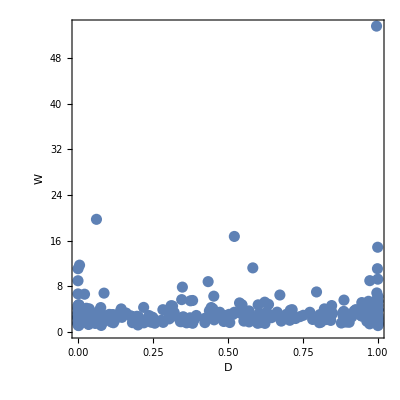
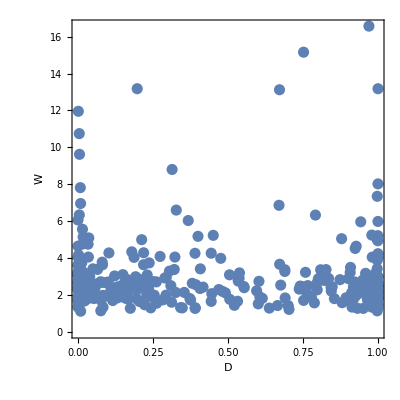
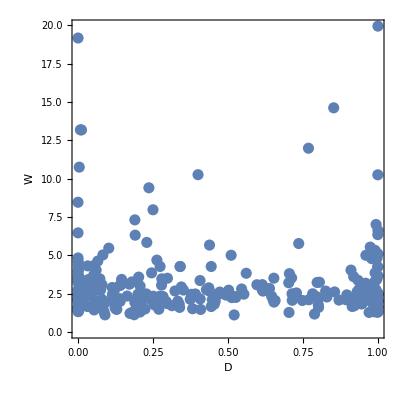

```mathematica
Table[
ListPlot[
RandomChoice/@GatherBy[WDflipping[[2;;,2;;]],#[[;;2]]&][[;;,;;,-2;;]],
AspectRatio->1,PlotStyle->PointSize[.02],Frame->{{True,False},{True,False}},PlotRange->All,FrameStyle->14,FrameLabel->{"D","W"}],{3}]
```

#### Original WD distributions

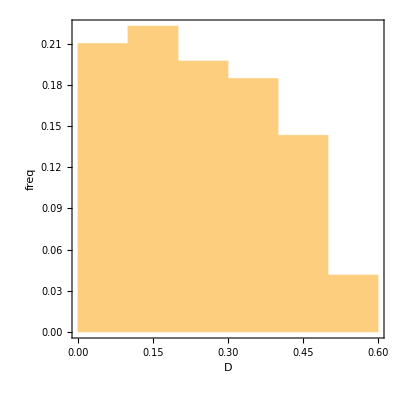
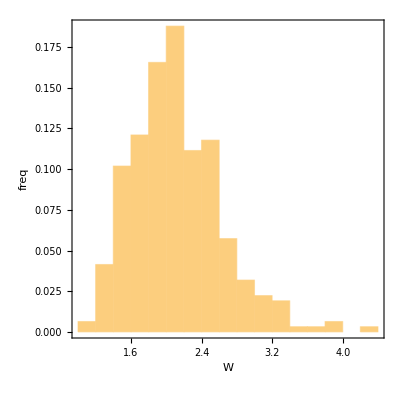

```mathematica
Histogram[#[[1]],Automatic,"Probability",Frame->{{True,False},{True,False}},PlotRange->All,AspectRatio->1,FrameLabel->{#[[2]],"freq"}]&/@({Transpose[Union[WDflipping[[2;;,{2,3}]]]],WDflipping[[1,{2,3}]]}ᵀ)
```

#### logitWD distributions

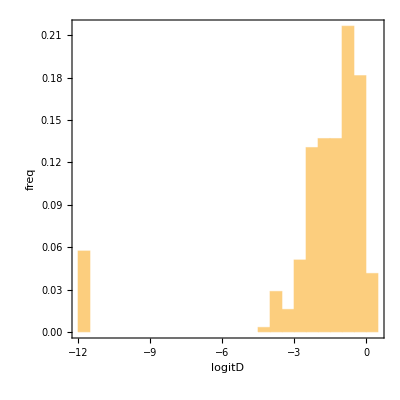
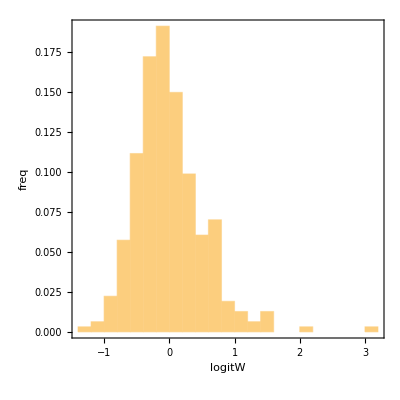

```mathematica
Histogram[#[[1]],Automatic,"Probability",Frame->{{True,False},{True,False}},PlotRange->All,AspectRatio->1,FrameLabel->{#[[2]],"freq"}]&/@({Transpose[Union[WDflipping[[2;;,{4,5}]]]],WDflipping[[1,{4,5}]]}ᵀ)
```

#### logitWD distributions after t-flipping

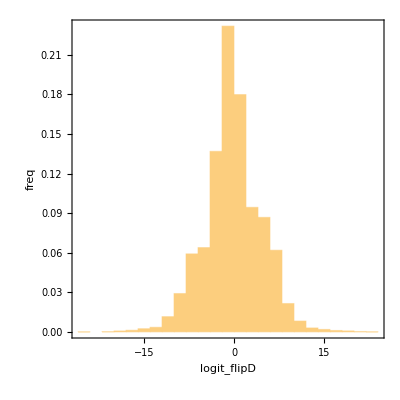
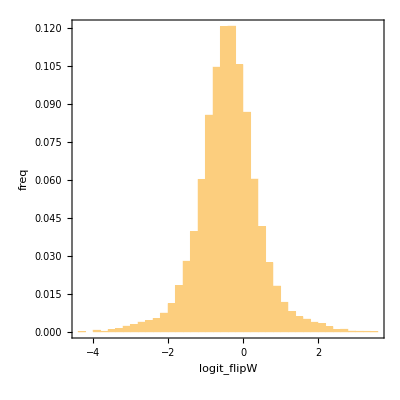

```mathematica
Histogram[#[[1]],Automatic,"Probability",Frame->{{True,False},{True,False}},PlotRange->All,AspectRatio->1,FrameLabel->{#[[2]],"freq"}]&/@({Transpose[Union[WDflipping[[2;;,{6,7}]]]],WDflipping[[1,{6,7}]]}ᵀ)
```

#### WD distributions after t-flipping

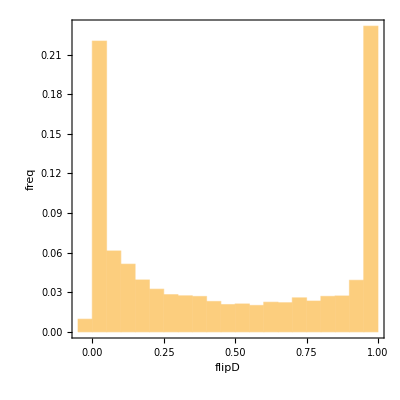
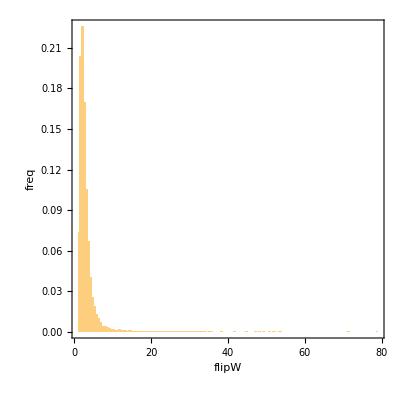

```mathematica
Histogram[#[[1]],Automatic,"Probability",Frame->{{True,False},{True,False}},PlotRange->All,AspectRatio->1,FrameLabel->{#[[2]],"freq"}]&/@({Transpose[Union[WDflipping[[2;;,{8,9}]]]],WDflipping[[1,{8,9}]]}ᵀ)
```

#### Comparison

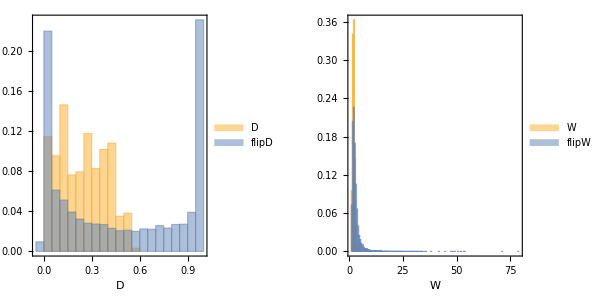

```mathematica
GraphicsRow[Histogram[#[[1]],Automatic,"Probability",Frame->{{True,False},{True,False}},PlotRange->{{0,#[[2]]},{0,All}},AspectRatio->1,ChartLegends->Placed[(Style[#,16]&/@#[[3]]),Scaled@{.8,.8}],ImageSize->Medium,FrameStyle->16,FrameLabel->{#[[3,1]],None}]&/@({{Transpose[Union[WDflipping[[2;;,{2,3}]]]],Transpose[Union[WDflipping[[2;;,{8,9}]]]]}ᵀ,{All,10},{WDflipping[[1,{2,3}]],WDflipping[[1,{8,9}]]}ᵀ}ᵀ),ImageSize->1000]
```

#### Smooth Kernel Distributions version

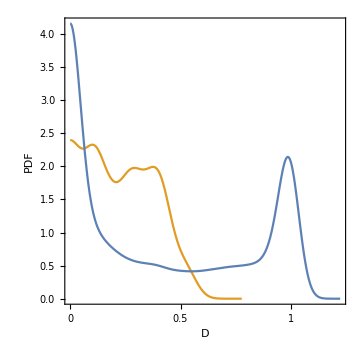
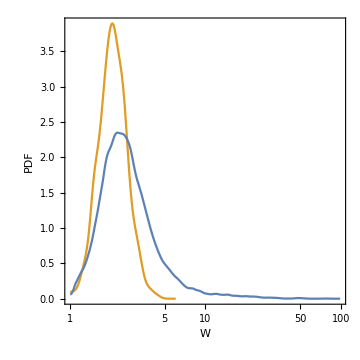

```mathematica
Row[Show[#,ImageSize->Medium]&/@({
Plot[
Evaluate[PDF[#[[1]],x]],Flatten[{x,#[[1]]["Domain"][[1]]}],PlotRange->All,AspectRatio->1,PlotRangePadding->None,Frame->{{True,False},{True,False}},FrameLabel->{#[[2]],"PDF"},FrameTicks->{#[[3]],None},FrameStyle->Directive[Black,14,Thin],PlotStyle->ColorData[97][2]]&@{SmoothKernelDistribution[#[[1]],"Silverman",{"Bounded",0,"Gaussian"}],#[[2]],#[[3]]}&/@({{#[[1]],Log10@#[[2]]}&@Chop[Union[WDflipping[[2;;,{2,3}]]]ᵀ,10^-3],{"D","W"},{{0,.5,1},{Log10@#,#}&/@{1,5,10,50,100}}}ᵀ),Plot[Evaluate[PDF[#[[1]],x]],Flatten[{x,#[[1]]["Domain"][[1]]}],PlotRange->All,AspectRatio->1,PlotRangePadding->None,Frame->{{True,False},{True,False}},FrameLabel->{#[[2]],"PDF"},FrameTicks->{#[[3]],None},FrameStyle->Directive[Black,14,Thin]]&@{SmoothKernelDistribution[#[[1]],"Silverman",{"Bounded",0,"Gaussian"}],#[[2]],#[[3]]}&/@({{#[[1]],Log10@#[[2]]}&@Chop[Union[WDflipping[[2;;,{8,9}]]]ᵀ,10^-3],{"D","W"},{{0,.5,1},{Log10@#,#}&/@{1,5,10,50,100}}}ᵀ)}ᵀ),Spacer[10]]
```

### SibSwap Preserves PICs

Ammonites Phylogeny downloaded from The Paleobiology Database: 
http://paleobiodb.org/data1.2/taxa/list.csv?datainfo&rowcount&base_name=Ammonoidea&taxon_status=accepted

```mathematica
TableView[
AmmonitesPhylogeny=Import["/Users/avimayo/Google Drive/SibSwap and Parti response/pbdb_data.csv"][[16;;,{1,5,6,7}]]
]
```

orig_notaxon_ranktaxon_nameparent_no14505subclassAmmonoidea1231585445genusNeoepigoniceras1450515052genusJimenites1450515433genusPomerania1450515360genusParavirgatites1450514557genusAnclyoceras1450514000orderCeratitida1450514335genusPoporites1400094122suborderPtychitina1400094120suborderMeekocerina1400086840superfamilyArcestoidea1400086839familyArcestidae86840356889genusRhaetites86839329606speciesRhaetites rhaeticus35688914025genusAnisarcestes86839356887speciesAnisarcestes subdimidiatus14025423657subfamilyJoannitinae86839423665subfamilyLobitinae86839356734genusGonarcestes86839356885speciesGonarcestes piae356734356733genusGaleites8683914404genusStenarcestes86839301771speciesStenarcestes subumbilicatus14404301773speciesStenarcestes orbis14404301776speciesStenarcestes peribothrus14404301774speciesStenarcestes diogenis14404301775speciesStenarcestes polysphinctus14404301777speciesStenarcestes ptychodes14404302175speciesStenarcestes julicus14404266597speciesStenarcestes leiostracus1440414340genusProarcestes86839423427speciesProarcestes marcheanus14340266512speciesProarcestes escheri14340267199speciesArcestes (Proarcestes) winnemae14340386752speciesProarcestes pannonicus14340386754speciesProarcestes reyeri14340386750speciesProarcestes boeckhi14340301699speciesProarcestes danai14340267196speciesArcestes (Proarcestes) shastensis14340266593speciesProarcestes planus14340265394speciesProarcestes gabbi14340396984speciesProarcestes esinensis14340301693speciesProarcestes barrandei14340265565speciesProarcestes balfouri14340265318speciesProarcestes nevadanus14340266594speciesProarcestes wittenburgi14340301706speciesProarcestes ausseeanus14340267195speciesArcestes (Proarcestes) carpenteri14340172627speciesProarcestes bramantei14340265317speciesArcestes (Proarcestes) pacificus14340301695speciesProarcestes mojsisovicsi14340270480speciesProarcestes gaytani14340267198speciesArcestes (Proarcestes) whitneyi14340301697speciesProarcestes moeschi14340301709speciesProarcestes dittmari14340301698speciesProarcestes marcoui14340267197speciesArcestes (Proarcestes) traski14340386748speciesProarcestes subtridentinus14340269420speciesProarcestes bicarinatus1434014031genusArcestes86839301763speciesArcestes evolutus14031301716speciesArcestes tomostomus14031301728speciesArcestes clausus14031264209speciesArcestes syngonus14031301713speciesArcestes compressus14031301731speciesArcestes oligosarcus14031278368speciesArcestes intuslabiatus14031301744speciesArcestes biceps14031301742speciesArcestes subdistinctus14031301739speciesArcestes pugillaris14031301759speciesArcestes richthofeni14031301740speciesArcestes distinctus14031388451speciesArcestes taramellianus14031301727speciesArcestes opertus14031395225speciesArcestes muensteri14031301745speciesArcestes cylindroides14031423652speciesArcestes extralabiatus14031423654speciesArcestes marchenanus14031301719speciesArcestes antonii14031301722speciesArcestes microcephalus14031301724speciesArcestes conjugens14031301769speciesArcestes inflatogaleatus14031301747speciesArcestes didymus14031301725speciesArcestes periolcus14031395227speciesArcestes gibbus14031301720speciesArcestes simplex14031301733speciesArcestes polysarcus14031301753speciesArcestes sisyphus14031329607speciesArcestes tenuis14031301756speciesArcestes agnatus14031301736speciesArcestes ooides14031301748speciesArcestes nannodes14031301761speciesArcestes semistriatus14031301711speciesArcestes bufo14031396970speciesArcestes trompianus14031301726speciesArcestes czoernigi14031301718speciesArcestes placenta14031245779speciesArcestes megaphyllus14031423653speciesArcestes cimmensis14031423656speciesArcestes reyeri14031389763speciesArcestes seimkanensis14031301768speciesArcestes parvogaleatus14031301723speciesArcestes pachystomus14031356650speciesArcestes ventricosus14031301730speciesArcestes hypocyrtus14031301750speciesArcestes bicornis14031301767speciesArcestes obtusegaleatus14031421969speciesArcestes leonardi14031301717speciesArcestes aspidostomus14031301735speciesArcestes megalosomus14031301755speciesArcestes oxystomus14031301770speciesArcestes oxycephalus14031301732speciesArcestes stenostomus14031301752speciesArcestes diphyus14031301734speciesArcestes monachus14031301754speciesArcestes monocerus14031301749speciesArcestes simostomus14031301737speciesArcestes pseudogaleatus14031301757speciesArcestes probletostomus14031298145speciesArcestes gigantogaleatus14031301760speciesArcestes decipiens14031301715speciesArcestes cheilostomus14031301765speciesArcestes galeiformis14031301710speciesArcestes colonus1403114304subgenusArcestes (Pararcestes)14031301704speciesPararcestes genuflexus14304301702speciesPararcestes lipoldi14304301700speciesPararcestes sublabiatus14304278366speciesPararcestes sturi14304301703speciesPararcestes rotundatus14304266595speciesPararcestes acutus14304301701speciesPararcestes zitteli14304301764speciesArcestes acutegaleatus14031301762speciesArcestes dimidiatus14031301729speciesArcestes polycaulus14031301714speciesArcestes tacitus14031301712speciesArcestes ciceronis14031265315speciesArcestes andersoni14031421971speciesArcestes subbicornis14031301721speciesArcestes subsimplex14031301743speciesArcestes dicerus14031301746speciesArcestes platystomus14031301738speciesArcestes holostomus14031301758speciesArcestes leptomorphus14031100974familyCladiscitidae86840322318subfamilyProcladiscitinae10097414230genusMesocladiscites322318172660speciesMesocladiscites caucasius1423014324genusPhyllocladiscites322318322326speciesPhyllocladiscites crassus14324235878speciesPhyllocladiscites basarginensis14324322329speciesPhyllocladiscites connectens14324172621speciesPhyllocladiscites proponticus14324322331speciesPhyllocladiscites acheshbokensis1432414373genusPsilocladiscites322318322324speciesPsilocladiscites molaris1437314399genusSphaerocladiscites322318322332speciesSphaerocladiscites buralkitensis14399267200speciesSphaerocladiscites mendenhalli14399259760speciesSphaerocladiscites martini14399322333speciesSphaerocladiscites omolonensis1439914251genusNeocladiscites322318278788speciesNeocladiscites taskanensis14251278789speciesNeocladiscites parenicus1425114343genusProcladiscites100974322323speciesProcladiscites simplex14343175273speciesProcladiscites yasoda14343322321speciesProcladiscites pantanelli14343172659speciesProcladiscites elegans14343388452speciesProcladiscites meneghinianus14343238111speciesProcladiscites griesbachi14343322320speciesProcladiscites rodostoma14343184809speciesProcladiscites brancoi14343322322speciesProcladiscites mulleri14343322319speciesProcladiscites macilentus14343322336subfamilyCladiscitinae10097414285genusParacladiscites322336302211speciesParacladiscites indicus14285266571speciesParacladiscites multilobatus14285302210speciesParacladiscites timidus14285302212speciesParacladiscites gemmellaroi1428514173genusHypocladiscites322336322380speciesHypocladiscites subaratus14173301527speciesHypocladiscites subtornatus14173427865speciesHypocladiscites compressus14173322392speciesHypocladiscites subcarinatus1417314073genusCladiscites322336301519speciesCladiscites quadratus14073301522speciesCladiscites obesus14073301524speciesCladiscites neortus14073322341speciesCladiscites externecavatus14073322349speciesCladiscites angustus14073269423speciesCladiscites striatulus14073270489speciesCladiscites ungeri14073302197speciesCladiscites externeplicatus14073322338speciesCladiscites umbilicatus14073322345speciesCladiscites beyrichi14073322340speciesCladiscites gorgiae14073322339speciesCladiscites tuvalicus14073266573speciesCladiscites tornatus14073302199speciesCladiscites semitornatus14073301526speciesCladiscites crassestriatus14073322394speciesCladiscites indicus14073301523speciesCladiscites striatissimus14073100975familySphingitidae8684014400genusSphingites100975301687speciesSphingites coangustatus14400301691speciesSphingites stoppanii14400270494speciesSphingites meyeri14400395201speciesSphingites turcicus14400301692speciesSphingites favrei14400301686speciesSphingites bacchus14400301690speciesSphingites meriani14400302188speciesSphingites pumilio14400301689speciesSphingites bronni14400100976subfamilyJoannitidae8684014382genusRomanites100976266603speciesRomanites simionescui1438214189genusJoannites100976423658speciesJoannites batyolcus14189395222speciesJoannites trilabiatus14189386755speciesJoannites proavus14189301677speciesJoannites klipsteini14189423660speciesJoannites deschmanni14189254372speciesJoannites cymbiformis14189386757speciesJoannites dieneri14189301680speciesJoannites styriacus14189396974speciesJoannites tridentinus14189301684speciesJoannites salteri14189270477speciesJoannites joannisaustriae14189301683speciesJoannites subdiffissus14189301681speciesJoannites diffissus14189395223speciesJoannites deranicus14189386756speciesJoannites caminensis14189265295familyProarcestidae8684014259genusNevadisculites265295176860speciesNevadisculites smithi14259176859speciesNevadisculites taylori14259193712speciesNevadisculites depressus14259186084speciesNevadisculites minutus1425914153genusHaidingerites14000356831speciesHaidingerites acutinodis1415393258suborderParaceltitina14000185455genusJeanbesseiceras14000185568speciesJeanbesseiceras jacksoni18545586664superfamilyMegaphyllitoidea1400086665familyProcarnitidae8666487027genusProcarinites8666514094genusDigitophyllites8666514342genusProcarnites86665424699speciesProcarnites immaturus14342175271speciesProcarnites xizangensis14342250310speciesProcarnites modestus14342166311speciesProcarnites kunlunensis14342169274speciesProcarnites kokeni14342425780speciesProcarnites ptychitoides14342424701speciesProcarnites lolouensis1434286667familyMegaphyllitidae8666414263genusNitanoceras86667250329speciesNitanoceras compressum14263250326speciesNitanoceras selwyni14263356735genusPtychopopanoceras86667356892speciesPtychopopanoceras hyatti35673514227genusMegaphyllites86667266474speciesMegaphyllites gebzensis14227423678speciesMegaphyllites sandalinus14227266475speciesMegaphyllites procerus14227301489speciesMegaphyllites humilis14227266591speciesMegaphyllites insectus14227172618speciesMegaphyllites prometheus14227329616speciesMegaphyllites johannisboehmi14227269415speciesMegaphyllites jarbas14227266465speciesMegaphyllites chiosensis14227423402speciesMegaphyllites oenipontanus14227301490speciesMegaphyllites applanatus14227388454speciesMegaphyllites obolus14227172645speciesMegaphyllites compressus14227186064speciesMegaphyllites wildhorsensis14227175272speciesMegaphyllites evolutus14227301488speciesMegaphyllites transiens1422714106genusDobrogeites86667356741speciesDobrogeites tirolitiformis14106265529genusHumboldtites86667265430speciesHumboldtites septentrionalis265529100767genusMetasturia86667357911speciesMetasturia gracilis10076787029familyProsphingitidae8666414352genusProsphingites87029389541speciesProsphingites karangatiensis14352181429speciesProsphingites czekanowskii14352422037speciesProsphingites nala14352424712speciesProsphingites coombsi14352235714speciesProsphingites ovalis14352389542speciesProsphingites tenuis1435286666familyParapopanoceratidae8666486914genusAmphipopanoceras86666250319speciesAmphipopanoceras acutum86914389765speciesAmphipopanoceras dzeginense86914432852speciesAmphipopanoceras zvetkovi86914190865speciesAmphipopanoceras medium86914189876speciesAmphipopanoceras tetsa86914192984speciesAmphipopanoceras selwyni86914395819genusGlobopopanoceras86666173261speciesGlobopopanoceras haugi39581914405genusStenopopanoceras86666181370speciesStenopopanoceras karangatiense14405250311speciesStenopopanoceras falcatum14405431676speciesStenopopanoceras russkiense14405181663speciesStenopopanoceras mirabile14405250316speciesStenopopanoceras celere14405250314speciesStenopopanoceras angulatum14405250312speciesStenopopanoceras normale14405172640speciesStenopopanoceras transiens14405250315speciesStenopopanoceras obesum1440514303genusParapopanoceras86666250324speciesParapopanoceras torelli14303181628speciesParapopanoceras asseretoi14303389764speciesParapopanoceras plicatum14303181631speciesParapopanoceras dzeginense14303181639speciesParapopanoceras paniculatum14303427573speciesParapopanoceras routi14303427572speciesParapopanoceras fraseri14303252749speciesParapopanoceras wapii14303250321speciesParapopanoceras malmgreni14303181363speciesParapopanoceras inconstans14303149311superfamilyMeekoceratoidea1400082446familyDieneroceratidae14931114456genusWyomingites82446169464speciesWyomingites whiteanus14456169462speciesWyomingites aplanatus14456169460speciesWyomingites arnoldi14456190565speciesWyomingites angustatus14456175451speciesWyomingites scapulatus1445681792genusDieneroceras82446169554speciesDieneroceras tientungense81792169276speciesDieneroceras mediterranea81792173271speciesDieneroceras marcoui81792191680speciesDieneroceras skutarensis81792172682speciesDieneroceras caucasicum8179282445speciesDieneroceras spathi81792169434speciesDieneroceras subquadratum81792169564speciesDieneroceras goudemandi81792424669speciesDieneroceras karazini81792142171speciesDieneroceras dieneri81792142173speciesDieneroceras woondumense81792172683speciesDieneroceras magnum8179282347familyProptychitidae149311427649genusRoopnarinites82347397491speciesRoopnarinites paucesculptatum427649181318genusClypeoceratoides82347190574speciesClypeoceratoides kulensis181318337853speciesClypeoceratoides kuluensis181318181319speciesClypeoceratoides gantmani18131882357genusBukkenites82347175421speciesBukkenites incisus82357175423speciesBukkenites strigatus82357175426speciesBukkenites macilentus82357175425speciesBukkenites nanus82357175422speciesBukkenites nitidus82357427669speciesBukkenites sakesarensis82357215032genusEvenites82347215033speciesEvenites kummeli21503282346genusHeibergites82347171874speciesHeibergites heibergensis82346245062genusDiscoproptychites82347186144speciesDiscoproptychites walcotti24506286989genusKoninickites82347169546genusWailiceras82347169547speciesWailiceras aemulus16954614307genusParaspidites82347260100speciesParaspidites obesus14307427644speciesParaspidites bicarinatus14307260097speciesParaspidites praecursor14307169543genusNanningites82347166275speciesNanningites tientungense169543166281genusJieshaniceras82347166282speciesJieshaniceras guizhouense166281166279genusHubeitoceras82347166274speciesHubeitoceras yanjiaensis166279181314genusKoninckitoides82347342681speciesKoninckitoides solus181314181315speciesKoninckitoides posterius181314215036speciesKoninckitoides taimyrensis181314428033genusUssuriceras82347428034speciesUssuriceras acutisellatum42803382362genusPrionolobus82347188060speciesPrionolobus buchianus82362397493speciesPrionolobus hanieli82362188055speciesPrionolobus planulatus82362186150speciesMeekoceras (Prionolobus) waageni82362175449speciesPrionolobus konincki82362175450speciesPrionolobus lucinus82362266284speciesPrionolobus ophioneus82362397492speciesPrionolobus indoaustralicus82362427973speciesPrionolobus orbis82362175448speciesPrionolobus welteri82362166262speciesPrionolobus hubeiensis82362266278speciesPrionolobus sequens82362149342genusPachyproptychites82347149343speciesPachyproptychites otoceratoides14934214110genusDunedinites82347175430speciesDunedinites pinguis14110149329speciesDunedinites magnumbilicatus14110175232speciesDunedinites maduoensis14110165621genusGuodunites82347169632speciesGuodunites monneti165621165620speciesGuodunites hooveri165621258609genusMonneticeras82347319127speciesMonneticeras kalinkini258609258610speciesMonneticeras compressum258609169540genusXiaoqiaoceras82347294773speciesXiaoqiaoceras americanum169540169541speciesXiaoqiaoceras involutus169540428030genusEoptychites82347265965speciesEoptychites obliqueplicatus428030428032speciesEoptychites evolutus42803087024genusPleurogyronites82347175441speciesPleurogyronites kraffti87024149321genusPseudoproptychites82347149322speciesPseudoproptychites hiemalis14932114350genusProptychites82347175429speciesProptychites newelli14350427670speciesProptychites wargalensis14350422041speciesProptychites scheibleri14350230788speciesProptychites latifimbriatus14350180597speciesProptychites pagei14350169207speciesProptychites trilobatus14350203116speciesProptychites grandis14350203113speciesProptychites rosenkrantzi14350265964speciesProptychites plicatus14350265962speciesProptychites aberrans14350265957speciesProptychites oldhamianus14350265960speciesProptychites discoides14350174815speciesProptychites subgrandis14350203114speciesProptychites anomalus14350166278speciesProptychites candidus14350203115speciesProptychites intermedius14350265959speciesProptychites magnumbilicatus14350422040speciesProptychites markhami14350188047speciesProptychites lawrencianus14350203118speciesProptychites simplex14350175428speciesProptychites kummeli14350175427speciesProptychites mulleri14350203117speciesProptychites subdiscoides14350169206speciesProptychites ammonoides1435014035genusArctomeekoceras82347185546speciesArctomeekoceras tardum14035175437speciesArctomeekoceras obtusum14035181422speciesArctomeekoceras rotundatum14035185545speciesArctomeekoceras popovi1403514359genusPseudaspidites82347234395speciesPseudaspidites planus14359169518speciesPseudaspidites muthianus1435982451speciesPseudaspidites wheeleri14359186176speciesPseudaspidites popovi14359169469speciesPseudaspidites silberlingi14359422051speciesPseudaspidites yudishthira14359149435genusKummelia82347169548genusLeyeceras82347169550speciesLeyeceras rothi16954814076genusClypeoceras82347428022speciesClypeoceras largisellatum14076266245speciesAspidites magnumbilicatus14076266244speciesAspidites arenosus14076266247speciesAspidites dentosus14076397495speciesAspidites meridianus14076427988subspeciesAspidites meridianus involutus397495149457speciesClypeoceras timorense14076428060speciesClypeoceras excentricum14076260095speciesClypeoceras superbum14076428026subspeciesAspidites superbus praecursor260095101066subfamilyProptychitinae8234714351genusProptychitoides101066191821speciesProptychitoides trigonalis14351424693speciesProptychitoides tunglanensis14351397473speciesProptychitoides arthaberi14351191824speciesProptychitoides decipiens1435114079genusCollignonites101066287415speciesCollignonites asamai14079266283speciesCollignonites undatus1407914087genusDalmatites101066398712speciesDalmatites ropini14087425073speciesDalmatites attenuatus14087425072speciesDalmatites kittli14087398713speciesDalmatites morlaccus1408714366genusPseudokymatites101066425461speciesPseudokymatites involutus14366339262speciesPseudokymatites tabulatus14366424585speciesPseudokymatites svilajanus1436614060genusBoreomeekoceras101066181420speciesBoreomeekoceras keyserlingi1406014300genusParanoritoides101066174820speciesParanoritoides paranoritoides14300224719genusTompoproptychites82347224721speciesTompoproptychites umbonatus224719169843genusTulongites82347169844speciesTulongites xiaoqiaoi169843185488familyAlbanitidae149311185467genusGaudemerites185488185468speciesGaudemerites rectangularis18546714006genusAlbanites185488184800speciesAlbanites arbanus14006342686speciesAlbanites vulgaris14006207579speciesAlbanites guizhouensis14006169277speciesAlbanites triadicus14006175453speciesAlbanites sheldoni14006184798speciesAlbanites osmanicus14006388256speciesAlbanites americanus1400682326familyMelagathiceratidae14931114297genusParanannites82326169628speciesParanannites sinensis14297292021speciesParanannites involutus1429782455speciesParanannites slossi1429782453speciesParanannites mulleri14297169597speciesParanannites subangulosus14297265434speciesParanannites oviformis14297234613speciesParanannites baudi14297169598speciesParanannites dubius14297169445speciesParanannites aspenensis1429714229genusMelagathiceras82326175405speciesMelagathiceras crassum14229181547speciesMelagathiceras globosus14229230874genusUssurijuvenites82326230876speciesUssurijuvenites artyomensis230874230875speciesUssurijuvenites popovi230874230877speciesUssurijuvenites kwangsiensis230874169511genusJinyaceras82326169512speciesJinyaceras bellum169511169861speciesJinyaceras hindostanum169511169505genusHebeisenites82326169509speciesHebeisenites evolutus169505169510speciesHebeisenites compressus169505169507speciesHebeisenites varians16950582325genusThermalites82326175410speciesThermalites needhami8232514277genusOwenites82326169443speciesOwenites koeneni14277169606speciesOwenites simplex14277169609speciesOwenites carpenteri1427782452familyParanoritidae149311169863genusShigetaceras82452169864speciesShigetaceras dunajensis169863176957genusVercherites82452176960speciesVercherites pulchrum176957176958speciesVercherites vercherei176957190009speciesVercherites wyleri176957294772speciesVercherites undulatus17695714216genusLingyunites82452169542speciesLingyunites discoides14216169472genusGalfettites82452234589speciesGalfettites kyrae169472234590speciesGalfettites omani169472169473speciesGalfettites lucasi169472169563speciesGalfettites simplicitatis169472292007speciesGalfettites wanneri169472181344genusLepiskites82452190568speciesLepiskites tsaregradskii181344181345speciesLepiskites kolymensis181344169551genusUrdyceras82452169552speciesUrdyceras insolitus169551169847speciesUrdyceras tulongensis169551234591genusSafraites82452234592speciesSafraites simplex23459114446genusVavilovites82452181338speciesVavilovites turgidus14446175434speciesVavilovites obtusus14446175432speciesVavilovites sverdrupi14446181340speciesVavilovites compressus14446433234speciesVavilovites meridialis14446224720speciesVavilovites subtriangularis14446224722speciesVavilovites kuluensis14446258607genusKoiloceras82452427668speciesKoiloceras sahibi258607258608speciesKoiloceras romanoi258607427664genusPashtunites82452166271speciesPashtunites kraffti42766414298genusParanorites82452428008speciesParanorites hydaspis14298230787speciesParanorites lyellianus14298166269speciesParanorites xiaohensis14298266259speciesParanorites gigas14298142178speciesParanorites queenslandicus14298266253speciesParanorites magnumbilicatum14298428011speciesParanorites inflatus14298142179speciesParanorites hillae14298149414speciesParanorites varians14298169516speciesParanorites jenksi14298166267speciesParanorites lichuanensis14298428010speciesParanorites aequalis14298266260speciesParanorites volutus14298428009speciesParanorites praestans14298260101speciesParanorites ambiensis14298266246speciesParanorites kingianus14298204348speciesParanorites madagascariensis14298427666genusAwanites82452427667speciesAwanites awani42766614207genusKoninckites82452278661speciesMeekoceras (Koninckites) tuberculatum14207428013speciesKoninckites truncatus14207266263speciesKoninckites radiatus14207191682speciesKoninckites timorensis14207265961speciesKoninckites khoorensis14207166272speciesKoninckites lingyunensis14207422053speciesKoninckites varaha14207175431speciesKoninckites dimidiatus14207266257speciesKoninckites vetustus14207395160speciesKoninckites libyssinus14207176951genusRadioceras82452427684speciesRadioceras truncatum176951260091speciesRadioceras evolvens176951425451speciesRadioceras tabulatum176951149468familyArctoceratidae149311169851genusBrayardites149468319128speciesBrayardites involutus169851169853speciesBrayardites compressus169851169852speciesBrayardites crassus16985114032genusArctoceras149468169568speciesArctoceras strigatus14032172685speciesArctoceras robinsoni14032172687speciesArctoceras kiparisovae14032174816speciesArctoceras meridionale14032149466speciesArctoceras septentrionale14032361558speciesArctoceras erebori14032428171speciesArctoceras lindstroemi14032217019speciesArctoceras omoloiense14032203792speciesArctoceras oebergi14032169466speciesArctoceras tuberculatum14032190007speciesArctoceras schalteggeri14032149484speciesArctoceras subhydaspis14032142183speciesArctoceras blomstrandi14032169848genusNammalites149468169849speciesNammalites pilatoides169848258612genusTruempyceras149468174813speciesTruempyceras pluriformis258612260238speciesTruempyceras compressum258612165738genusChurkites149468165739speciesChurkites noblei165738324337speciesChurkites egregius165738427648speciesChurkites warei165738258960genusNuetzelia149468258961speciesNuetzelia himalayica25896014415genusSubmeekoceras149468169572speciesSubmeekoceras hsuyuchieni14415169569speciesSubmeekoceras mushbachanum14415294774genusMinersvillites149468294775speciesMinersvillites farai294774258958genusEscarguelites149468258959speciesEscarguelites spitiensis258958180587familyMullericeratidae149311438036genusOphimullericeras180587438037speciesOphimullericeras paullae438036180588genusMullericeras180587427672speciesMullericeras indusense180588180594speciesMullericeras fergusoni180588149359speciesMullericeras spitiense180588380836speciesMullericeras gujiaoense180588427671speciesMullericeras shigetai180588427673speciesMullericeras niazii180588149318genusUssuridiscus180587149319speciesUssuridiscus varaha149318427675speciesUssuridiscus ventriosus149318180590speciesUssuridiscus ensanus149318427676speciesUssuridiscus ornatus14931893290suborderOtoceratina1400086646superfamilyOtoceratoidea93290357398familyVavilovitidae8664686647familyOtoceratidae8664614027genusAnotoceras86647175224speciesAnotoceras costatum14027427934speciesAnotoceras nala14027422038speciesAnotoceras kama14027427936speciesAnotoceras intermedium14027176940speciesAnotoceras subtabulatus1402793318genusMetotoceras8664714276genusOtoceras86647188046speciesOtoceras woodwardi1427693319genusJulfotoceras86647427305speciesJulfotoceras abadehense93319188034speciesJulfotoceras tarazi93319187093speciesJulfotoceras admirabile9331982317familyAraxoceratidae8664693309subfamilyKonglingitinae8231714389genusSanyangites93309174259speciesSanyangites rotulus14389174263speciesSanyangites circellus14389174256speciesSanyangites serratus14389207784speciesSanyangites umbilicatus14389174261speciesSanyangites multilobatus14389174255speciesSanyangites liratus14389207783speciesSanyangites tricarinatus14389174254speciesSanyangites inflatus14389174258speciesSanyangites obesus14389174257speciesSanyangites lucunensis14389174260speciesSanyangites simplex14389174264speciesSanyangites lenticularis14389174262speciesSanyangites latumbilicatus1438993311genusJinjiangoceras93309165830speciesJinjiangoceras etoushanense93311165832speciesJinjiangoceras penglaense93311174251speciesJinjiangoceras shatangense93311174253speciesJinjiangoceras ventroplanum93311207780speciesJinjiangoceras stenosellatum93311174250speciesJinjiangoceras compressum93311174249speciesJinjiangoceras striatum93311165831speciesJinjiangoceras planodiscum93311174252speciesJinjiangoceras jiangxiense9331193316genusEtoushanoceras93309165828speciesEtoushanoceras stenoventrum93316165827speciesEtoushanoceras ergouense9331693317genusHongshuiheites93309165829speciesHongshuiheites discus9331793313genusEusanyangites93309424260speciesEusanyangites bandoi9331393315genusGeermuceras93309173389speciesGeermuceras platum9331593312genusKiangsiceras93309207782speciesKiangsiceras rotule9331293310genusKonglingites93309207777speciesKonglingites inflatus93310165826speciesKonglingites laibinensis93310186135speciesKonglingites tumidus93310207775speciesKonglingites sinensis93310207774speciesKonglingites striatus93310207773speciesKonglingites latisellatus93310207779speciesKonglingites gaoanensis9331093314genusLijiangoceras93309173388speciesLijiangoceras longilobatum9331414116genusEoaraxoceras82317103998speciesEoaraxoceras ruzhencevi14116352271speciesEoaraxoceras spinosai14116202318speciesEoaraxoceras robustum1411693298subfamilyAraxoceratinae8231793300genusDiscotoceras9329814356genusPrototoceras93298207764speciesPrototoceras plicatum14356165882speciesPrototoceras longilobatum14356207765speciesPrototoceras fengchengense14356427333speciesPrototoceras intermedium14356207768speciesPrototoceras inflatum14356322541speciesPrototoceras parallelum14356427331speciesPrototoceras fedoroffi14356427327speciesPrototoceras discoidale14356266616speciesPrototoceras pulchriforme14356207770speciesPrototoceras pachygyrum14356218690speciesPrototoceras hunanense14356207767speciesPrototoceras complanatum14356207769speciesPrototoceras anfuense14356427337speciesPrototoceras raddei14356165881speciesPrototoceras venustum14356427321speciesPrototoceras tropitum14356266617speciesPrototoceras simplex14356218691speciesPrototoceras xiangulingense14356427326speciesPrototoceras compressum14356207766speciesPrototoceras multidenticulatum14356427335speciesPrototoceras pessoides14356266618speciesPrototoceras diluterotalum1435693302genusVescotoceras93298427328speciesVescotoceras evanidum93302427339speciesVescotoceras serratum93302182449speciesVescotoceras japonicum93302427330speciesVescotoceras acutum9330293299genusRotaraxoceras93298427265speciesRotaraxoceras caucasicum93299427278speciesRotaraxoceras deruptum9329993304genusAvushoceras93298423519speciesAvushoceras jakowlewi9330414030genusAraxoceras93298427264speciesAraxoceras latissimum14030427300speciesAraxoceras varicatum14030266619speciesAraxoceras simplex14030427291speciesAraxoceras rotoides14030427296speciesAraxoceras tectum14030427284speciesAraxoceras latum14030174003speciesAraxoceras abarquense14030174004speciesAraxoceras iranense14030245157speciesAraxoceras trochoides14030207763speciesAraxoceras kiangsiense14030427281speciesAraxoceras glenisteri1403014112genusDzhulfoceras93298427304speciesDzhulfoceras paulum14112183884speciesDzhulfoceras orientale1411282316speciesDzhulfoceras furnishi14112427303speciesDzhulfoceras inflatum1411293306genusAnfuceras93298207772speciesAnfuceras longilobatum9330693301genusUrartoceras93298427323speciesUrartoceras abichianum9330193305genusPeriptychoceras93298207771speciesPeriptychoceras compressum9330593303genusVedioceras93298427275speciesVedioceras nakamurai93303427267speciesVedioceras ogbinense93303427269speciesVedioceras ventroplanum93303427273speciesVedioceras ventrosulcatum93303427271speciesVedioceras umbonovarum9330393307genusEojiangxiceras93298266620speciesEojiangxiceras meixianlingense9330714372genusPseudotoceras93298427348speciesPseudotoceras armenorum14372427349speciesPseudotoceras djoulfense1437293308genusAbadehceras93298427301speciesAbadehceras nakazawai9330886838familyAnderssonoceratidae8664614346genusProharpoceras86838169625speciesProharpoceras carinatitabulatum1434693294subfamilyPlanodiscoceratinae8683893296genusLeptogyroceras93294165880speciesLeptogyroceras compressum93296207749speciesLeptogyroceras dongshenlingense93296207750speciesLeptogyroceras latiumbilicatum9329614214genusLenticoceltites93294427262speciesLenticoceltites okimurai14214207752speciesLenticoceltites fengchengensis14214266614speciesLenticoceltites hastilis14214207753speciesLenticoceltites involutus1421493295genusPlanodiscoceras93294169319speciesPlanodiscoceras gratiosum93295207748speciesPlanodiscoceras longilobatum93295169814speciesPlanodiscoceras involutum9329593297genusFengchengoceras93294207751speciesFengchengoceras tricarinatum9329793291subfamilyAnderssonoceratinae8683814023genusAnderssonoceras93291218692speciesAnderssonoceras hunanense14023207754speciesAnderssonoceras simplex14023207755speciesAnderssonoceras robustum14023266615speciesAnderssonoceras dongshenlingense14023207756speciesAnderssonoceras anfuense1402314319genusPericarinoceras93291207760speciesPericarinoceras robustum14319207761speciesPericarinoceras compressum1431993292genusXiangulingites93291207757speciesXiangulingites orbilobatus93292207758speciesXiangulingites acutus93292207759speciesXiangulingites applanatus9329293293genusPachyrotoceras93291207936speciesPachyrotoceras laevigatum93293207762speciesPachyrotoceras fengchengense9329386774superfamilyClydonitaceae1400086815familyClydonitidae86774437234genusOphiceltites86815437236speciesOphiceltites halleri437234437235speciesOphiceltites fatuensis43723414075genusClydonites86815252138speciesClydonites pacificus14075356749speciesClydonites decoratus1407586817familyThetiditidae8677414369genusPseudothetidites86817278593speciesPseudothetidites zapfei14369278594speciesPseudothetidites trispinatus14369437221speciesPseudothetidites indicus14369252127speciesPseudothetidites brysonis14369278591genusAcanthothetidites86817278592speciesAcanthothetidites spinosus27859114160genusHelictites86817437227speciesHelictites beneckei14160437228speciesHelictites sundaicus14160252126speciesHelictites pacalis14160437224speciesHelictites leislingensis14160437222speciesHelictites subgeniculatus14160252124speciesHelictites minor14160421936speciesCeratites (Helictites) atalanta14160252125speciesHelictites decorus14160356795speciesHelictites geniculatus1416086977genusEothetidites86817252118speciesEothetidites lacrimosus86977252119speciesEothetidites pardoneti8697714423genusThetidites86817421933speciesThetidites guidonis14423252133speciesThetidites nudus14423356843speciesThetidites huxleyi1442314309genusParathetidites86817252123speciesParathetidites laevis14309252122speciesParathetidites robustus14309252120speciesParathetidites exquisitus1430914212genusLeislingites86817252129speciesLeislingites semiviatus14212278600speciesLeislingites reyeri14212278604speciesLeislingites welteri14212278596speciesLeislingites archibaldi14212252130speciesLeislingites quadratus14212252132speciesLeislingites politus14212278595speciesLeislingites pseudoarchibaldi14212278609speciesLeislingites sundaicus14212278598speciesLeislingites nicolai14212252131speciesLeislingites vancouverensis14212278606speciesLeislingites subalemon1421286986genusIdaoceras86817252134speciesIdaoceras idae86986252136speciesIdaoceras maclearni8698614248genusNassichukites86817252137speciesNassichukites dimidiatus1424886787familySteinmannitidae8677487009genusNannosteinmannites86787252045speciesNannosteinmannites yukonensis87009251802genusBihatites86787278611speciesBihatites bihatiensis25180286976genusEosteinmannites86787251808speciesEosteinmannites orientalis86976278613speciesEosteinmannites irregularis86976251809speciesEosteinmannites nitidus86976251810speciesEosteinmannites ursensis86976278615speciesEosteinmannites noetlingi86976278617speciesEosteinmannites lubbocki8697614403genusSteinmannites86787278619speciesSteinmannites ingens14403421950speciesArpadites (Steinmannites) noetlingi14403421949speciesSteinmannites desiderii14403251807speciesSteinmannites pacificus14403356756speciesSteinmannites hoernesi14403421948speciesArpadites (Steinmannites) clionitoides14403421947speciesSteinmannites undulatostriatus14403437246speciesSteinmannites timorensis14403421951speciesArpadites (Steinmannites) lubbocki1440314062genusBrouwerites86787252044speciesBrouwerites maclearni14062437250speciesBrouwerites intermedius14062252043speciesBrouwerites stotti14062251801genusScheutzites86787251803genusBaoenites86787437238speciesBaoenites parvus25180314008genusAlloclionites86787278562speciesAlloclionites ares14008437245speciesAlloclionites procerus14008278620speciesAlloclionites himamalayicus14008251811speciesAlloclionites dieneri14008356683speciesAlloclionites timorensis14008252376speciesAlloclionites welteri14008251812speciesAlloclionites jeanneti14008437241speciesAlloclionites horatii14008421944speciesAlloclionites aberrans14008421942speciesAlloclionites woodwardi1400887005genusMetaclionites86787251804speciesMetaclionites curvicostatus87005251806speciesMetaclionites taylori8700586809familyHeraclitidae8677414452genusWangoceras86809252101speciesWangoceras pax14452278794speciesWangoceras svalbardense1445214163genusHeraclites86809356778speciesHeraclites robustus14163252103speciesHeraclites canadensis1416386816familySandlingitidae8677414141genusGlamocites86816356760speciesGlamocites katzeri1414114436genusTraskites86816267223speciesClionites (Traskites) nanus14436265345speciesClionites (Traskites) robustus14436265342subgenusTraskites (Stantonites)14436267226speciesClionites (Stantonites) evolutus265342265343speciesClionites (Stantonites) rugosus265342265347subgenusTraskites (Neanites)14436265348speciesClionites (Neanites) californicus265347267228speciesClionites (Neanites) osmonti265347267227speciesClionites (Neanites) minutus265347267221speciesClionites (Traskites) stantoni14436265341speciesClionites (Traskites) fairbanksi14436267219speciesClionites (Traskites) americanus14436267222speciesClionites (Traskites) tornquisti14436251798genusShastites86816251800speciesShastites vulcanus251798267224speciesClionites (Shastites) compactus251798267225speciesClionites (Shastites) whitneyi251798265346speciesClionites (Shastites) compressus25179814388genusSandlingites86816265351speciesSandlingites andersoni14388251793speciesSandlingites oribasus14388289876speciesSandlingites pilari1438814128genusEremites86816356791speciesEremites orientalis14128356793speciesEremites crassitesta1412886807familyTibetitidae8677414279genusPalicites86807265059speciesPalicites mojsisovicsi14279252048genusPterotoceras86807356787speciesPterotoceras arthaberi252048101060genusParatibetites86807312689speciesParatibetites angustosellatus101060265098speciesParatibetites bertrandi101060265097speciesParatibetites geikiei101060421961speciesTibetites (Paratibetites) tornquisti101060312688speciesParatibetites yunnanensis101060207606speciesParatibetites clarkei101060265096speciesParatibetites adolphi10106014425genusTibetites86807312686speciesTibetites lanpingensis14425421955speciesTibetites murchisoni14425395007subgenusTibetites (Neotibetites)14425312685speciesTibetites perrinsmithi14425312684speciesTibetites ryalli14425101061genusLanpingoceras86807312690speciesLanpingoceras mirabile10106114264genusNodotibetites86807265088speciesNodotibetites nodosus1426414231genusMetacarnites86807265089speciesMetacarnites hendersoni14231356786speciesMetacarnites footei1423114019genusAnatibetites86807356784speciesAnatibetites kelvini14019312687speciesAnatibetites magnus14019252046subfamilyTibetitinae86807252056genusSirenotibetites252046252057speciesSirenotibetites cornutus25205614096genusDimorphotoceras252046252053speciesDimorphotoceras elegantulum14096252051speciesDimorphotoceras arctum14096356687speciesDimorphotoceras abnorme14096252049speciesDimorphotoceras caurinum14096252055speciesDimorphotoceras ursinum1409687015genusOxytibetites252046252047speciesOxytibetites welteri8701514258genusNeotibetites252046356785speciesNeotibetites weteringi14258252058speciesNeotibetites minor1425886808subfamilyCyrtopleuritinae8680714002genusAcanthinites86808433399speciesAcanthinites excelsus14002356780speciesAcanthinites excelsior14002252072speciesAcanthinites magnificus14002156632genusGandakites86808265077speciesGandakites kelviniformis15663287028genusProdrepanites86808252071speciesProdrepanites catenatus8702814098genusDionites86808421952speciesArpadites (Dionites) asbolus14098356771speciesDionites caesar1409814217genusLipuites86808265073speciesLipuites marianii14217265072speciesLipuites totiae1421714164genusHimavatites86808252086speciesHimavatites planiplicatus14164252088speciesHimavatites apinnatus14164252087speciesHimavatites multiauritus14164437376speciesHimavatites hogarti14164356781speciesHimavatites watsoni1416414254genusNeohimavatites86808252098speciesNeohimavatites peregrinus14254252099speciesNeohimavatites burlingi14254252096speciesNeohimavatites canadensis1425414108genusDrepanites86808252079speciesDrepanites rutherfordi14108356769speciesDrepanites hyatti1410814158genusHauerites86808267201speciesHauerites lawsoni14158356782speciesHauerites rarestriatus14158252084speciesHauerites piceus14158252085speciesHauerites astrictus1415887004genusMesohimavatites86808252090speciesMesohimavatites indigiricus87004252095speciesMesohimavatites caponicus87004252092speciesMesohimavatites costatus87004252089speciesMesohimavatites parvus87004252093speciesMesohimavatites columbianus8700414459genusXenodrepanites86808356773speciesXenodrepanites schucherti14459156631genusThiniites86808265074speciesThiniites thiniensis156631265075speciesThiniites acutus15663186921genusCarinacanthites86808252074speciesCarinacanthites calypso8692114454genusWelterites86808437374speciesWelterites heierlii14454356745speciesWelterites egregius14454252080genusAcanthodrepanites86808252083speciesAcanthodrepanites dieneri252080252081speciesAcanthodrepanites eusebii25208014084genusCyrtopleurites86808252076speciesCyrtopleurites bicrenatus14084252078speciesCyrtopleurites hersiliae14084433397subgenusCyrtopleurites (Acanthinites)14084433398speciesCyrtopleurites (Acanthinites) excelsior43339714041genusArgosirenites86808437372speciesArgosirenites trachyceratoides14041437364speciesArgosirenites argonautae14041437366speciesArgosirenites dianae14041427863speciesArgosirenites tenuistriatus14041156633genusAmmotibetites86807265094speciesAmmotibetites timorensis156633265095speciesAmmotibetites elisae156633265091speciesAmmotibetites wheeleri156633265093speciesAmmotibetites parawheeleri15663314237genusMetatibetites8680786812familyClionitidae8677414074genusClionitites86812421943speciesClionites salteri14074421946speciesClionites spinosus14074432431speciesClionites catharinae14074389757speciesClionites spiniger14074356753speciesClionites angulosus14074421945speciesClionites hughesi14074427732speciesClionites rarecostatus14074251145speciesClionitites laevis14074251144speciesClionitites punctulus14074251139speciesClionitites callazonensis14074251143speciesClionitites arietinus14074251138speciesClionitites venerabilis14074251141speciesClionitites reesidei14074101062genusIndoclionites86812356754speciesIndoclionites gracilis101062265339genusCalifornites86812265340speciesClionites (Californites) merriami265339267231speciesClionites (Californites) careyi26533914419genusSympolycyclus86812251148speciesSympolycyclus kellyi14419251147speciesSympolycyclus gunningi14419251146speciesSympolycyclus antiquus14419265352speciesSympolycyclus nodifer14419251795genusLeconteia86812251796speciesLeconteia californica251795267193speciesLeconteiceras occidentale25179594119suborderOtocerina1400086648superfamilyNoritoidea1400086653familyLanceolitidae8664814209genusLanceolites86653169593speciesLanceolites bicarinatus14209169456speciesLanceolites compactus14209424738speciesLanceolites discoidalis1420986655familyNoritidae8664814016genusAnanorites86655398718speciesAnanorites monticola1401614252genusNeoclypites86655356678speciesNeoclypites desertorum1425214234genusMetahedenstroemia86655191828speciesMetahedenstroemia kastriatae1423414047genusArthaberites86655428174speciesArthaberites alexandrae14047235704familyNoritidae8664814268genusNorites235704172649speciesNorites labensis14268264221speciesNorites gondola14268398717subgenusNorites (Ananorites)14268423675speciesNorites breguzzanus14268175242speciesNorites angusellatus14268356914speciesNorites arcuatus14268356652speciesNorites falcatus1426814061genusBosnites235704423097speciesBosnites clathratus14061235703genusSubalbanites235704235705speciesSubalbanites mirabilis23570386651familyInyoitidae86648258604genusHochuliites86651258606speciesHochuliites retrocostatus25860414182genusInyoites86651294776speciesInyoites beaverensis14182169588speciesInyoites krystyni14182172688speciesInyoites oweni14182260201speciesInyoites sedini1418214414genusSubinyoites86651169204speciesSubinyoites kashmiricus14414260137speciesSubinyoites punjabiensis1441414417genusSubvishnuites86651260240speciesSubvishnuites posterus14417188204speciesSubvishnuites enveris14417172689speciesSubvishnuites welteri14417175229speciesSubvishnuites yushuensis1441782450speciesSubvishnuites stokesi1441714238genusMetinyoites86651397496speciesMetinyoites discoidalis14238181321genusBajarunia14000181575speciesBajarunia euomphala181321215038speciesBajarunia alexeevae181321342682speciesBajarunia magna181321185544speciesBajarunia confusionensis181321185563speciesBajarunia pilata181321181322speciesBajarunia eiekitensis18132186677superfamilyPinacoceratoidea1400086684familyCarnitidae8667714362genusPseudocarnites86684356737speciesPseudocarnites arthaberi1436214066genusCarnites86684254375speciesCarnites floridus1406686680familyGymnitidae8667714460genusXiphogymnites86680357934speciesXiphogymnites spiniger1446014301genusParapinacoceras86680357919speciesParapinacoceras aspidoides14301100803subfamilyGymnitinae8668014176genusInaigymnites10080314063genusBuddhaites100803357936speciesBuddhaites rama14063250924speciesBuddhaites hagei1406386942genusDiscogymnites100803224547speciesDiscogymnites hollandi8694214014genusAnagymnites100803219439speciesAnagymnites acutus14014250923speciesAnagymnites viaalaska14014357932speciesAnagymnites lamarcki14014398727speciesAnagymnites torrensii14014339148speciesAnagymnites grandis1401414355genusProtoplatytes86680301510speciesProtoplatytes neglectus14355182880genusCostigymnites86680182881speciesCostigymnites asiaticus182880193868genusConstrigymnites86680193710speciesConstrigymnites robertsi193868344394subfamilyPlacitinae8668014328genusPlacites344394301500speciesPlacites subsymmetricus14328301497speciesPlacites placodes14328301498speciesPlacites myophorus14328265325speciesPlacites humboldtensis14328421975speciesPlacites oldhami14328301492speciesPlacites platyphyllus14328301496speciesPlacites perauctus14328301493speciesPlacites oxyphyllus14328278369speciesPlacites postsymmetricus14328250928speciesPlacites polydactylus14328301499speciesPlacites omphalius1432814292genusParagymnites344394357926speciesParagymnites sakuntala14292250926speciesParagymnites symmetricus1429214325genusPhyllytoceras86680329674speciesPhyllytoceras intermedium1432514149genusGymnites86680398721speciesGymnites mandiva14149172623speciesGymnites robinsoni14149423725speciesGymnites obliquus14149256424speciesGymnites billingsi14149386762speciesGymnites raphaelis14149175279speciesGymnites toulai14149250918speciesGymnites procerus14149277808speciesGymnites incultus14149398723speciesGymnites sankara14149182882speciesGymnites asseretoi14149182884speciesGymnites aghdarbandensis14149398726speciesGymnites subclausus14149175278speciesGymnites vastesellatus14149423723speciesGymnites palmai14149301512speciesGymnites breunneri14149302249speciesGymnites arthaberi14149398724speciesGymnites depauperatus14149398722speciesGymnites kirata14149250920speciesGymnites perplanus14149250919speciesGymnites compressus14149398720speciesGymnites vasantasena14149398725speciesGymnites religiosus14149175277speciesGymnites humboldti14149207595speciesGymnites machangpingensis14149356665speciesGymnites gibberulus14149172673speciesGymnites evolutus14149175280speciesGymnites petilus14149265437speciesGymnites calli14149265460speciesGymnites tregorum14149429274speciesGymnites watanabei14149186082speciesGymnites tozeri1414914203genusKiparisovia86680389772speciesKiparisovia khivachensis1420314126genusEpigymnites86680423416speciesEpigymnites frequens14126265436speciesEpigymnites alexandrae14126386760speciesEpigymnites credneri14126357930speciesEpigymnites ecki14126423417speciesEpigymnites paronae14126386761speciesEpigymnites moelleri14126423415speciesEpigymnites credneriformis14126219441speciesEpigymnites jollyanus1412614302genusParaplacites8668014440genusTropigymnites86680250917speciesTropigymnites haueri14440398630speciesTropigymnites chandra14440265555speciesTropigymnites planorbis14440100802subfamilyJaponitinae8668014067genusCaucasites100802172652speciesCaucasites evolutus14067250914speciesCaucasites mulleri14067256423speciesCaucasites nicholsi14067172653speciesCaucasites inflatus14067196094speciesCaucasites orchardi1406786682subfamilyPtychitidae8667714377genusPtychites86682423731speciesPtychites evolvens14377193713speciesPtychites domatus14377219448speciesPtychites miyagiensis14377172634speciesPtychites besnosovi14377398738speciesPtychites mahendra14377423522speciesPtychites rectangulatus14377423740speciesPtychites progressus14377398737speciesPtychites vidura14377219447speciesPtychites trochleaeformis14377356659speciesPtychites intermedius14377181636speciesPtychites pseudoeuglyphus14377423727speciesPtychites breunigi14377398735speciesPtychites everesti14377427569speciesPtychites cultrata14377398730speciesPtychites cognatus14377388461speciesPtychites noricus14377250935speciesPtychites wrighti14377398734speciesPtychites durandii14377398732speciesPtychites sumitra14377265435speciesPtychites evansi14377357904speciesPtychites eusomus14377425222speciesPtychites embreei14377398733speciesPtychites sahadeva14377250933speciesPtychites guloensis14377421976speciesPtychites posthumus14377237928speciesPtychites oppeli14377423734speciesPtychites gibbus14377423730speciesPtychites reductus14377252750speciesPtychites stachei14377266508speciesPtychites opulentus14377356660speciesPtychites suttneri14377356657speciesPtychites dontianus14377219449speciesPtychites nipponicus14377356662speciesPtychites maximus14377423737speciesPtychites stoliczkai14377356664speciesPtychites globus14377389769speciesPtychites tibetanus14377195169speciesPtychites gradinarui14377250939speciesPtychites hamatus14377193714speciesPtychites densistriatus14377423738speciesPtychites uhligi14377398728speciesPtychites rugifer14377395199speciesPtychites cylindroides1437714044genusAristoptychites86682267442speciesAristoptychites kolymensis14044357906speciesAristoptychites gerardi14044237934genusLanceoptychites86682292176speciesLanceoptychites styx237934292177speciesLanceoptychites charlyanus237934237933speciesLanceoptychites indistinctus237934292175speciesLanceoptychites velox23793414136genusFlexoptychites86682172635speciesFlexoptychites bugunzhensis14136259223speciesFlexoptychites angustoumbilicatus14136381345speciesFlexoptychites studeri14136237929speciesFlexoptychites flexuosus14136219446speciesFlexoptychites matsushimaensis14136237931speciesFlexoptychites acutus14136100964genusMalletoptychites86682181640speciesMalletoptychites kotschetkovi100964357908speciesMalletoptychites malletianus10096414223genusMalletophychites8668214121genusEosturia86682219432speciesEosturia towaensis1412114037genusArctoptychites86682191106speciesArctoptychites euglyphus14037250941speciesArctoptychites lingulatus14037191105speciesArctoptychites kruzini1403714186genusIstreites86682250942speciesIstreites nanuk14186356891speciesIstreites ptychitiformis1418686678familyJaponitidae86677172616genusAegeiceras86678172617speciesAegeiceras byzovae172616266468speciesAegeiceras ugra17261614118genusEogymnites86678292188speciesEogymnites arthaberi14118175274speciesEogymnites maduoensis1411814187genusJaponites86678266467speciesJaponites asseretoi14187357937speciesJaponites planiplicatus14187250915speciesJaponites wrighti14187207599speciesJaponites kueichowensis14187256422speciesJaponites starensis14187186081speciesJaponites surgriva14187425781speciesJaponites ziyunensis14187182883speciesJaponites kirata14187172648speciesJaponites labaensis14187175275speciesJaponites dieneri14187256421speciesJaponites welteri14187250916speciesJaponites readi1418714064genusBukowskiites86678357940speciesBukowskiites colvini1406486679familySturiidae8667714462genusZiyunites86679425783speciesZiyunites ziyunensis14462266466speciesZiyunites asseretoi1446214308genusParasturia86679266570speciesParasturia acutata14308431677speciesParasturia primorica14308357913speciesParasturia emmrichi1430814374genusPsilosturia86679175283speciesPsilosturia mohamedi14374175281speciesPsilosturia mongolica1437414411genusSturia86679252751speciesSturia japonica14411266501speciesSturia yalakensis14411302250speciesSturia karpinskyi14411386763speciesSturia forojuliensis14411175285speciesSturia semiarata14411172619speciesSturia sansovinii1441114102genusDiscoptychites86679389770speciesDiscoptychites subfastigatus14102266503speciesDiscoptychites pauli14102169693speciesDiscoptychites inaicus14102266505speciesDiscoptychites seebachi14102197644speciesDiscoptychites megalodiscus14102389771speciesDiscoptychites korkodonensis1410286685familyPinacoceratidae86677423691subfamilyPtychitinae86685356736genusBambanagites86685421974speciesBambanagites dieneri356736357925speciesBambanagites schlagintweiti35673614327genusPinacoplacites86685357928speciesPinacoplacites meridianus1432714334genusPompeckjites86685301505speciesPompeckjites layeri14334423418genusPraepinacoceras86685356651speciesPraepinacoceras damesi423418423476speciesPraepinacoceras airaghii423418423419speciesPraepinacoceras stoppanii42341814132genusEupinacoceras86685301509speciesEupinacoceras subimperator1413214326genusPinacoceras86685301504speciesPinacoceras parmaeforme14326250461speciesPinacoceras metternichi14326389133speciesPinacoceras verchojanicum14326301511speciesPinacoceras solum14326302236speciesPinacoceras hutteri14326250930speciesPinacoceras parma14326301494speciesPinacoceras respondens14326301507speciesPinacoceras imperator14326423685speciesPinacoceras philopater14326267216speciesPinacoceras rex14326423683speciesPinacoceras daonicum14326386759speciesPinacoceras dalpiazi14326398739speciesPinacoceras rajah14326301503speciesPinacoceras trochoides14326398740speciesPinacoceras loomisii14326302237subgenusPinacoceras (Pompeckjites)1432686995familyKlamathitidae8667714093genusDieneria86995265324speciesDieneria arthaberi1409314293genusParahauerites86995265323speciesParahauerites ashleyi14293265062speciesParahauerites sirenitoides1429314205genusKlamathites86995267203speciesKlamathites kellyi14205267202speciesKlamathites schucherti14205388257genusCaribouceras14000388258speciesCaribouceras slugense38825714341genusProavites14000264228speciesProavites hueffeli14341428173speciesProavites benigari1434186827familyCycloceratidae1400086656superfamilySagecerataceae1400086657familySageceratidae8665614305genusParasageceras86657172650speciesParasageceras tkhachense14305427923speciesParasageceras gracile14305427922speciesParasageceras discoidale1430514384genusSageceras86657197610speciesSageceras walteri14384301514speciesSageceras haidingeri14384266473speciesSageceras anatolicum1438486658familyHedenstroemiidae86656169613genusMesohedenstroemia86658169616speciesMesohedenstroemia planata169613260200speciesMesohedenstroemia olgae169613169614speciesMesohedenstroemia kwangsiana169613429250speciesMesohedenstroemia bosphorensis169613142180subfamilyHedenstromeniinae86658142182genusPseudohedenstromeia14218082355genusCordillerites86658389534speciesCordillerites bicarinatus82355185489speciesCordillerites angulatus82355250306speciesCordillerites bicarinatus82355169612speciesCordillerites antrum82355149361genusParahedenstroemia86658425453speciesParahedenstroemia petkovici149361149363speciesParahedenstroemia kiparisovae149361428061speciesParahedenstroemia acuta149361175249speciesParahedenstroemia latilobata14936186660subfamilyBeneckeiinae8665814057genusBeneckeia86660423525speciesBeneckeia subdenticulata14057427724speciesBeneckeia wogauana14057427727speciesBeneckeia levantina14057423673speciesBeneckeia buchi14057428070speciesBeneckeia denticulata14057429255speciesBeneckeia majiashanensis14057423671speciesBeneckeia tenuis14057169208genusClypites86658425299speciesClypites japonicus169208186147speciesClypites tenuis169208176966speciesClypites typicus169208177626genusTellerites86658428063speciesTellerites furcatus177626428065speciesTellerites oxynotum177626428068subfamilyAspenitinae86658428067subfamilyLanceolitinae86658181311genusAnahedenstroemia86658428056speciesAnahedenstroemia muthiana181311428050speciesAnahedenstroemia himalayica181311428052speciesAnahedenstroemia kasliuensis181311428054speciesAnahedenstroemia byansica181311397471speciesAnahedenstroemia waageni18131114159genusHedenstroemia86658181312speciesHedenstroemia tscherskii14159422039speciesHedenstroemia mojsisovicsi14159173268speciesHedenstroemia kossmati14159260138speciesHedenstroemia evoluta14159181395speciesHedenstroemia hedenstroemi1415914367genusPseudosageceras86658250305speciesPseudosageceras plicatum14367428066speciesPseudosageceras grippi14367191720subgenusPseudosageceras (Metasageceras)14367424662speciesPseudosageceras simplex14367235699speciesPseudosageceras boreale14367427678speciesPseudosageceras simplelobatum14367429251speciesPseudosageceras striatus14367169476speciesPseudosageceras augustum14367191721speciesPseudosageceras pasquayi14367149470speciesPseudosageceras multilobatum14367169285speciesPseudosageceras albanicum1436786659familyAspenitidae86656319125genusUssuriaspenites86659319126speciesUssuriaspenites evlanovi31912514049genusAspenites86659425300speciesAspenites kamurensis14049169457speciesAspenites acutus14049319109speciesAspenites radiatus14049278249speciesAspenites chaoxianensis14049100757genusPseudaspenites86659169478speciesPseudaspenites balinii100757234687speciesPseudaspenites planus100757169622speciesPseudaspenites evolutus100757169623speciesPseudaspenites tenuis100757169618speciesPseudaspenites layeriformis10075714056genusBeatites86659424737speciesBeatites berthae1405686802superfamilyTrachyceratoidea1400086804familyArpaditidae86802278558familyDronovitidae86802278559genusDronovites278558278560speciesDronovites pamiricus27855986811familyDistichitidae8680214288genusParadistichites86811437389speciesParadistichites ectolcitiformis14288384115genusMesodistichites86811384118speciesMesodistichites tozeri384115384120speciesMesodistichites evolutus38411514331genusPleurodistichites86811252110speciesPleurodistichites hindei14331265069speciesPleurodistichites trailli14331265230speciesPleurodistichites lilli14331252108speciesPleurodistichites stotti1433114113genusEctolcites86811356805speciesEctolcites pseudoaries14113252104speciesEctolcites childerhosei14113437394speciesEctolcites hochstetteri14113437395speciesEctolcites hollandi14113265065genusTrachypleuraspidites86811437423speciesTrachypleuraspidites malayicus265065265066speciesTrachypleuraspidites griffithi26506514104genusDistichites86811437385speciesDistichites leptacanthus14104437380speciesDistichites celticus14104437382speciesDistichites kmetyi14104437384speciesDistichites mesacanthus14104265063speciesDistichites harpalos14104437387speciesDistichites falcatus14104252106speciesDistichites gethingi14104356804speciesDistichites megacanthus14104437388speciesDistichites sollasii14104252105speciesDistichites columbianus14104437381speciesDistichites minos14104437386speciesDistichites tropicus14104252107speciesDistichites canadensis1410486996genusLeiodistichites86811252114speciesLeiodistichites anacanthus86996252112speciesLeiodistichites hacqueti86996252117speciesLeiodistichites beachi86996252116speciesLeiodistichites ursidens86996356723familyBuchitidae86802252214genusBuchites356723356789speciesBuchites aldrovandii25221486805familyTrachyceratidae8680214157genusHannaoceras86805356807speciesHannaoceras nasturtium14157267240speciesPolycyclus henseli14157264246subfamilyAnolcitinae8680565986genusZestoceras264246251030speciesZestoceras enode65986264250speciesZestoceras lorigae65986264248speciesZestoceras barwicki65986251028speciesZestoceras nitidum6598687002genusMaclearnoceras264246251034speciesMaclearnoceras ensio87002251033speciesMaclearnoceras maclearni8700214026genusAnolcites264246251021speciesAnolcites politus14026265500speciesTrachyceras (Anolcites) barberi14026399241speciesAnolcites dieneri14026423356speciesAnolcites doleriticus14026251023speciesAnolcites rasilis14026251026speciesAnolcites anguinus14026251024speciesAnolcites papillatus14026251022speciesAnolcites angustus14026251020speciesAnolcites impolitus14026251025speciesAnolcites gemmatus14026265499speciesTrachyceras (Anolcites) drakei1402614137genusFrankites264246251049speciesFrankites sutherlandi14137264254speciesFrankites regoledanus14137251048speciesFrankites glaber14137264251speciesFrankites apertus14137264247genusFalsanolcites264246425291speciesFalsanolcites arminae264247396978speciesFalsanolcites recubariense264247363620speciesFalsanolcites gortanii264247425293speciesFalsanolcites cappellinii264247396982speciesFalsanolcites julium264247386746speciesFalsanolcites richthofeni264247423430speciesFalsanolcites rieberi264247386745speciesFalsanolcites laczkoi264247423605speciesFalsanolcites doleriticum264247425289speciesFalsanolcites elisabethae264247423429speciesFalsanolcites gervasuttii264247425281speciesFalsanolcites furcosus264247423613speciesFalsanolcites clapsavonum26424714048genusAsklepioceras264246251037speciesAsklepioceras laurenci14048356765speciesAsklepioceras segmentatum14048251035speciesAsklepioceras exilis14048251036speciesAsklepioceras altilis14048395196speciesAsklepioceras squammatum1404814090genusDaxatina264246251055speciesDaxatina megabrotheus14090251054speciesDaxatina laubei14090251052speciesDaxatina canadensis14090251056speciesDaxatina limpida14090100977subfamilyProtrachyceratinae8680514401genusSpirogmoceras100977250971speciesSpirogmoceras shastense1440114357genusProtrachyceras100977425237speciesProtrachyceras mutabile14357265504speciesTrachyceras (Protrachyceras) springeri14357427901speciesProtrachyceras wahrmani14357395181speciesProtrachyceras ibericum14357267217speciesTrachyceras (Protrachyceras) storrsi14357421962speciesTrachyceras (Protrachyceras) ralphuanum14357398714speciesProtrachyceras cautleyi14357425238speciesProtrachyceras guizhouense14357423634speciesProtrachyceras hispanicum14357250967speciesProtrachyceras sikanianum14357423433speciesProtrachyceras parinaense14357207605speciesProtrachyceras costulatum14357386738speciesProtrachyceras pseudoarchelaus14357265221speciesProtrachyceras margaritosum14357363621speciesProtrachyceras archelaus14357351055speciesProtrachyceras ladinum14357423432speciesProtrachyceras irregulare14357207603speciesProtrachyceras deprati14357386740speciesProtrachyceras longobardicum14357427905speciesProtrachyceras lermani14357427904speciesProtrachyceras negevense14357395061speciesProtrachyceras anatolicum14357427730speciesProtrachyceras sirenitiforme14357363618speciesProtrachyceras steinmanni14357386736speciesProtrachyceras spitiense1435714119genusEoprotrachyceras100977265218speciesEoprotrachyceras dunni14119250965speciesEoprotrachyceras matutinum14119265212speciesEoprotrachyceras subasperum14119265214speciesEoprotrachyceras americanum14119265210speciesEoprotrachyceras meeki14119350503speciesEoprotrachyceras gredleri14119265216speciesEoprotrachyceras lahontanum14119265224speciesEoprotrachyceras curionii14119350501subspeciesEoprotrachyceras curionii ramonensis265224250966speciesEoprotrachyceras gibsoni1411914313genusParatrachyceras100977278701speciesParatrachyceras ulynense14313356742speciesParatrachyceras hofmanni14313325422subfamilyHaoceratinae86805325425genusSinomeginoceras325422325427speciesSinomeginoceras xingyiense325425325426speciesSinomeginoceras wangi325425325423genusHaoceras325422325424speciesHaoceras xingyiense325423100980subfamilySirenitinae8680514375genusPterosirenites100980251070speciesPterosirenites auritus14375278699speciesPterosirenites seimkanensis14375278790speciesPterosirenites nelgehensis14375278792speciesPterosirenites obrucevi1437514410genusStriatosirenites100980278703speciesStriatosirenites ulynensis14410251065speciesStriatosirenites striatofalcatus14410389760speciesStriatosirenites kinasovi14410389759speciesStriatosirenites repini14410278704speciesStriatosirenites kedonensis14410389761speciesStriatosirenites buralkitensis1441014018genusAnasirenites100980265061speciesAnasirenites briseis14018265060speciesAnasirenites ekkehardi14018289883speciesAnasirenites crassicrenulatus14018278760genusSeimkanites100980278762speciesSeimkanites aculeatus27876014398genusSirenotrachyceras100980264258speciesSirenotrachyceras thusneldae14398351069speciesSirenotrachyceras rudolphi14398351067speciesSirenotrachyceras hadwigae14398269419speciesSirenotrachyceras furcatum14398367193genusOrientosirenites100980251064speciesOrientosirenites yakutensis367193367195speciesOrientosirenites bytschkovi36719314450genusVredenburgites100980356746speciesVredenburgites vredenburgi1445014257genusNeosirenites100980278702speciesNeosirenites pseudopentastichus1425714397genusSirenites100980267218speciesSirenites hayesi14397389755speciesSirenites irregularis14397251062speciesSirenites ovinus14397278363speciesSirenites betulinus14397252653speciesSirenites malayicus14397289881speciesSirenites senticosus14397251061speciesSirenites nanseni14397265350speciesSirenites lawsoni14397265362speciesSirenites homfrayi14397387679speciesSirenites smithi14397251063speciesSirenites serotinus1439714368genusPseudosirenites100980250456speciesPseudosirenites pardoneti14368251136speciesPseudosirenites bullatus14368421965speciesPseudosirenites elegans14368437358speciesPseudosirenites stachei14368437360speciesPseudosirenites evae14368251137speciesPseudosirenites falcatus14368251134speciesPseudosirenites pressus1436814280genusPamphagosirenites100980251067speciesPamphagosirenites pamphagus14280251069speciesPamphagosirenites pacificus1428014370genusPseudotibetites100980251071genusNorosirenites100980251072speciesNorosirenites krystyni25107114099genusDiplosirenites100980356744speciesDiplosirenites raineri14099248171genusOkhototrachyceras86805248172speciesOkhototrachyceras seimkanense248171251027subfamilyTrachyceratinae8680514256genusNeoprotrachyceras251027289877speciesNeoprotrachyceras attila14256289879speciesNeoprotrachyceras baconicum1425614245genusMuensterites251027251046speciesMuensterites delicatulus14245351071speciesMuensterites hirschi14245356767speciesMuensterites ectodus14245351073speciesMuensterites karreri14245269410speciesMuensterites okeani14245251042speciesMuensterites helenae14245251044speciesMuensterites glaciensis14245100981genusAustrotrachyceras251027251059speciesAustrotrachyceras obesum10098114432genusTrachyceras251027278768speciesTrachyceras silberlingi14432264456speciesTrachyceras dichotomum14432264262speciesTrachyceras bipunctatum14432264264speciesTrachyceras muensteri14432270492speciesTrachyceras acutocostatum14432423638speciesTrachyceras pescolense14432388407speciesTrachyceras paronai14432251058speciesTrachyceras aonoides14432325428speciesTrachyceras multituberculatum14432423629speciesTrachyceras villanovae14432423614speciesTrachyceras judicaricum14432251057speciesTrachyceras desatoyense14432423609speciesTrachyceras stuerzenbaumi14432421964speciesTrachyceras tibeticum14432423610speciesTrachyceras amicum14432398113speciesTrachyceras medusae14432388448speciesTrachyceras fedaiae14432423650speciesTrachyceras epolense14432423635speciesTrachyceras ibericum14432423626speciesTrachyceras hacqueti14432395186speciesTrachyceras laricum14432270504speciesTrachyceras infundibuliforme14432386743speciesTrachyceras rutoranum14432207602speciesTrachyceras douvillei14432423611speciesTrachyceras neumayri14432423565speciesTrachyceras liepoldti14432388449speciesTrachyceras symmetricum14432423625speciesTrachyceras roderici14432423546speciesTrachyceras cordevolicum14432270485speciesTrachyceras mandelslohi14432423645speciesTrachyceras pustericum14432270496speciesTrachyceras bouei14432423642speciesTrachyceras pontius14432264454speciesTrachyceras aon14432269411speciesTrachyceras sulciferum14432421963speciesTrachyceras austriacum14432398114speciesTrachyceras oenanum14432423550speciesTrachyceras trinodosum14432423535speciesTrachyceras avisianum14432264452genusBrotheotrachyceras86805264458speciesBrotheotrachyceras brotheus264452264460speciesBrotheotrachyceras difforme264452100979subfamilyArpaditinae8680514435genusTrachystenoceras100979251000speciesTrachystenoceras gabbi1443514114genusEdmundites100979356763speciesEdmundites rimkinensis1411414105genusDittmarites10097914215genusLiardites100979250997speciesLiardites whiteavesi1421514228genusMeginoceras100979250987speciesMeginoceras caurinum14228250978speciesMeginoceras triviale14228250982speciesMeginoceras meginae14228250984speciesMeginoceras aylardi14228250986speciesMeginoceras effervescens14228250979speciesMeginoceras tetsa1422814040genusArgolites100979423445speciesArgolites celtitoides14040386732speciesArgolites arietiformis14040278767speciesArgolites trinodosus14040423448speciesArgolites arpaditoides14040423452speciesArgolites fortis14040423450speciesArgolites paronai14040423443speciesArgolites mojsisovicsi14040251003genusArctoarpadites100979251005speciesArctoarpadites costatus25100314038genusArctosirenites100979251010speciesArctosirenites canadensis14038251012speciesArctosirenites columbianus14038251014speciesArctosirenites sverdrupi14038251013speciesArctosirenites southeri1403886983genusHisnitites100979251002speciesHisnitites janmulleri8698314206genusKlipsteinia100979351059speciesKlipsteinia nataliae14206270516speciesKlipsteinia radiata14206229471speciesKlipsteinia disciformis14206269412speciesKlipsteinia achelous14206269416speciesKlipsteinia irregularis14206269405speciesKlipsteinia boetus1420614396genusSilenticeras100979250996speciesSilenticeras involutum14396250990speciesSilenticeras bamberi14396250995speciesSilenticeras liardense14396250992speciesSilenticeras hatae14396250989speciesSilenticeras gibsoni1439687014genusOtoarpadites100979250999speciesOtoarpadites auritus87014251016genusYakutosirenites100979251018speciesYakutosirenites pentastichus25101614046genusArpadites100979423440speciesArpadites bracki14046423569speciesArpadites pilari14046423442speciesArpadites pulcher14046386734speciesArpadites cinensis14046267235speciesArpadites kingi14046386735speciesArpadites telleri14046269406speciesArpadites busiris14046429273speciesArpadites sakawanus14046269421speciesArpadites rimosus14046423571speciesArpadites sesostris14046421941speciesArpadites lissarensis14046396972speciesArpadites trettensis14046396986speciesArpadites manzonii14046356761speciesArpadites arpadis14046423604speciesArpadites orientalis14046270503speciesArpadites rueppeli14046423441speciesArpadites dichotomus14046423568speciesArpadites vaceki14046421940speciesArpadites stracheyi14046423567speciesArpadites toldyi14046423574speciesArpadites helenae14046386733speciesArpadites szaboi14046248168genusBoreotrachyceras86805248169speciesBoreotrachyceras omkutchanicum24816886810familyNoridiscitidae8680214267genusNoridiscites86810356689speciesNoridiscites viator14267384127speciesNoridiscites nodosus1426714246genusNairites86810266842speciesNairites laevis14246266841speciesNairites armenius1424694124suborderPinacocerina1400014408genusStolleites14000169633genusProcurvoceratites14000169636speciesProcurvoceratites subtabulatus169633169634speciesProcurvoceratites pygmaeus169633169635speciesProcurvoceratites ampliatus169633100759subfamilyDinaritinae1400014054genusBalkanites100759424776speciesBalkanites tabulatus1405414091genusDiaplococeras100759423531speciesDiaplococeras connectens14091423532speciesDiaplococeras liccanum1409114281genusParaacrochordiceras1400086668superfamilyCeratitiaceae1400094121suborderSagecerina1400086642superfamilyXenodiscaceae1400093271familyHuananoceratidae86642274050genusShangsilites93271274052speciesShangsilites shangsiensis274050274051speciesShangsilites guangyuanensis27405093272genusHuananoceras93271207787speciesHuananoceras qianjiangense93272166334speciesHuananoceras involutum93272218693speciesHuananoceras leiyangense93272258486speciesHuananoceras pseudoopalinum93272207996speciesHuananoceras pseudoperornatum93272185452familyHemilecanitidae8664214162genusHemilecanites185452185485speciesHemilecanites paradiscus14162169278speciesHemilecanites discus14162185486speciesHemilecanites fastigatus14162185458genusDeweveria185452185487speciesDeweveria crenulata185458319110speciesDeweveria kovalenkoi185458185459speciesDeweveria dudresnayi185458190012genusKraffticeras86642190013speciesKraffticeras pseudoplanulatum19001293277familyTapashanitidae8664293278genusSinoceltites93277207802speciesSinoceltites costatus93278207804speciesSinoceltites sichuanensis93278171042speciesSinoceltites curvatus93278207803speciesSinoceltites opimus93278185753speciesSinoceltites delicatus93278218688speciesSinoceltites ellipticus9327893280genusMingyuexiceras9327714420genusTapashanites93277207799speciesTapashanites compressus14420171041speciesTapashanites floriformis14420427199speciesTapashanites meishanensis14420207796speciesTapashanites latiumbilicus14420207793speciesTapashanites tenuicostatus14420218686speciesTapashanites hunanensis14420169303speciesTapashanites yaowalakae14420207800speciesTapashanites curvoplicatus14420427189speciesTapashanites achurensis14420427198speciesTapashanites latumbilicatus14420207794speciesTapashanites robustus14420427197speciesTapashanites kwangsiensis14420218687speciesTapashanites orientalis14420427195speciesTapashanites honghensis14420207801speciesTapashanites costatus14420207798speciesTapashanites acuticostatus14420427192speciesTapashanites changxinensis14420205157speciesTapashanites chaotianensis14420207807speciesMingyuexiaceras changxingense14420207806speciesMingyuexiaceras radiatum14420205158speciesMingyuexiaceras changxingensis14420207797speciesTapashanites mingyuexiaensis14420184090speciesTapashanites changxingensis1442093279genusPseudostephanites93277207805speciesPseudostephanites nodosus93279171040speciesPseudostephanites costatus9327986643familyParaceltitidae8664214072genusCibolites86643174242speciesCibolites dongwuliensis14072129033speciesCibolites africanus14072124557speciesCibolites waageni14072182452speciesCibolites uddeni14072427179speciesCibolites parvus14072174243speciesCibolites curvoplicatus1407214202genusKingoceras86643124555speciesKingoceras kingi14202187092speciesKingoceras achurense14202218683genusMeixianites86643218684speciesMeixianites guangdongensis21868393260genusMeitianoceras86643174510speciesMeitianoceras meitianense93260166289speciesMeitianoceras paulum93260166288speciesMeitianoceras sphaelobatum9326093259genusDoulingoceras86643427178speciesDoulingoceras costituberosum93259174206speciesDoulingoceras nodosum9325914282genusParaceltites86643218681speciesParaceltites zhongguoensis14282128560speciesParaceltites elegans14282427175speciesParaceltites costatus14282192709speciesParaceltites sellardsi14282192710speciesParaceltites multicostatus14282124549speciesParaceltites ornatus14282427177speciesParaceltites xizangensis14282124551speciesParaceltites altudensis14282218680speciesParaceltites hunanensis14282174241speciesParaceltites hoeferi14282218682speciesParaceltites hubeiensis14282427176speciesParaceltites platyventrus14282124553speciesParaceltites rectangularis1428214262genusNielsenoceras86643192711speciesNielsenoceras skinneri1426286645familyDzulfitidae8664214111genusDurvilleoceras86645425272speciesDurvilleoceras woodmani1411193269familyDzhulfitidae8664214312genusParatirolites93269346541speciesParatirolites birunii1431282307speciesParatirolites kittli14312130963speciesParatirolites trapezoidalis14312204350speciesParatirolites douvillei1431282306speciesParatirolites compressus14312346543speciesParatirolites multiconus14312346544speciesParatirolites serus14312346542speciesParatirolites quadratus14312346540speciesParatirolites coronatus14312169302speciesParatirolites nakornsrii14312173390speciesParatirolites guizhouensis14312130962speciesParatirolites vediensis14312289662genusStoyanowites93269346558speciesStoyanowites aspinosus289662130964speciesStoyanowites dieneri28966293270genusDzhulfites93269130971speciesDzhulfites nodosus93270346538speciesDzhulfites zalensis93270346539speciesDzhulfites hebes93270130970speciesDzhulfites spinosus93270346545genusJulfotirolites93269346546speciesJulfotirolites kozuri34654514001genusAbichites93269346555speciesAbichites paucinodus14001346552speciesAbichites subtrapezoidalis14001346554speciesAbichites ariaeii14001130969speciesAbichites abichi14001346557speciesAbichites terminalis14001346556speciesAbichites shahriari14001346553speciesAbichites alibashiensis14001130965speciesAbichites stoyanowi14001346547genusAlibashites93269346550speciesAlibashites uncinatus346547346549speciesAlibashites ferdowsii346547130967speciesAlibashites mojsisovicsi346547346551speciesAlibashites stepanovi346547176949familyKashmiritidae8664214336genusPreflorianites176949191678speciesPreflorianites garbinus14336173273speciesPreflorianites strongi14336169492speciesPreflorianites radians14336169440speciesPreflorianites toulai14336429254speciesPreflorianites ellipticus1433614156genusHanielites176949169496speciesHanielites carinatitabulatus14156169495speciesHanielites elegans14156169498speciesHanielites angulus14156169497speciesHanielites gracilus14156169841genusNyalamites176949169493speciesNyalamites angustecostatus169841265298genusSakhaitoides176949265299speciesSakhaitoides allarensis265298265301speciesSakhaitoides verkhoyanicus26529814195genusKashmirites176949175391speciesKashmirites borealis14195234394speciesKashmirites baidi14195397478speciesAnakashmirites lidacensis14195422029speciesAnakashmirites purusha14195190553speciesAnakashmirites molensis14195427948speciesAnakashmirites radiosus14195397479speciesAnakashmirites brouweri14195397488speciesKashmirites evolutus14195319133speciesKashmirites shevyrevi14195397487speciesKashmirites densistriatus14195294769speciesKashmirites confusionensis14195207577speciesKashmirites subarmatus14195397485speciesKashmirites subrobustus14195294766speciesKashmirites utahensis14195260088speciesKashmirites nivalis14195169490speciesKashmirites kapila14195397486speciesKashmirites robustus14195428074speciesKashmirites blaschkei14195190004speciesKashmirites weisserti14195175394speciesKashmirites columbianus14195175395speciesKashmirites warreni14195294770speciesKashmirites stepheni14195169489speciesKashmirites guangxiense14195260086speciesKashmirites armatus1419514363genusPseudoceltites176949189888speciesPseudoceltites normalis14363169831speciesPseudoceltites multiplicatus14363429263speciesPseudoceltites lenticularis14363170696speciesPseudoceltites darvazicus14363265303subgenusPseudoceltites (Saikhanites)14363265304speciesPseudoceltites (Saikhanites) khenteyensis265303429264speciesPseudoceltites evolutus14363427190speciesPseudoceltites anhuiensis1436393273familyLiuchengoceratidae8664293276genusWangrenoceras93273166290speciesWangrenoceras rotalarium9327693275genusRongjiangoceras93273207789speciesRongjiangoceras lenticulare9327593274genusLiuchengoceras93273207791speciesLiuchengoceras crassicostatum93274207790speciesLiuchengoceras evolutum93274207792speciesLiuchengoceras minutum93274246839speciesLiuchengoceras melnikovi9327493287familyPleuronodoceratidae8664293289genusQianjiangoceras93287185755speciesQianjiangoceras anhuiense93289207902speciesQianjiangoceras costatum93289207903speciesQianjiangoceras multiseptatum9328993288genusLongmenshanoceras93287207901speciesLongmenshanoceras plicatum9328814318genusPentagonoceras93287207913speciesPentagonoceras costatum14318207916speciesPentagonoceras guangyuanense14318207915speciesPentagonoceras guizhouense14318207914speciesPentagonoceras attenuatum14318207917speciesPentagonoceras spinosum14318207918speciesPentagonoceras chaotianense1431814383genusRotodiscoceras93287207911speciesRotodiscoceras wangcangense14383166292speciesRotodiscoceras hubeiense14383207904speciesRotodiscoceras asiaticum14383207905speciesRotodiscoceras torulosum14383207907speciesRotodiscoceras latilobatum14383427241speciesRotodiscoceras nodosum14383208001speciesRotodiscoceras langdaiense14383207909speciesRotodiscoceras kwangsiense14383207912speciesRotodiscoceras guizhouense14383205162speciesRotodiscoceras dushanense14383207906speciesRotodiscoceras longilobatum14383427242speciesRotodiscoceras varians1438314332genusPleuronodoceras93287185754speciesPleuronodoceras tonglingense14332207897speciesPleuronodoceras densiplicatum14332165999speciesPleuronodoceras dushanense14332207898speciesPleuronodoceras liuchengense14332218689speciesPleuronodoceras hubeiense14332207900speciesPleuronodoceras inflatum14332207892speciesPleuronodoceras guiyangense14332207894speciesPleuronodoceras guangdeense14332207895speciesPleuronodoceras carinatum14332207890speciesPleuronodoceras tenuicostatum14332166291speciesPleuronodoceras dayenense14332207896speciesPleuronodoceras radiatum14332207893speciesPleuronodoceras curvaplicatum14332207891speciesPleuronodoceras attenuatum14332208000speciesPleuronodoceras anshunense14332186139speciesPleuronodoceras mapingense14332205160speciesPleuronodoceras mirificum14332171033speciesPleuronodoceras multinodosum14332427240speciesPleuronodoceras robustum14332207899speciesPleuronodoceras matanense1433282359familyXenoceltitidae86642169503genusWeitschaticeras82359169504speciesWeitschaticeras concavum16950314457genusXenoceltites82359169499speciesXenoceltites variocostatus14457429253speciesXenoceltites praematurus14457189887speciesXenoceltites evolutus14457190549speciesXenoceltites matheri14457424674speciesXenoceltites crenoventrosus14457294763speciesXenoceltites cordilleranus14457175400speciesXenoceltites subevolutus1445782449speciesXenoceltites youngi14457266274speciesXenoceltites rotula14457185547speciesXenoceltites crenulatus14457425785speciesXenoceltites ziyunensis14457185566speciesXenoceltites spencei14457169500speciesXenoceltites pauciradiatus14457319134speciesXenoceltites subvariocostatus14457427998speciesXenoceltites russkiensis14457429252speciesXenoceltites opimus14457169501genusGuangxiceltites82359169502speciesGuangxiceltites admirabilis169501102806genusSulioticeras82359175238speciesSulioticeras sulioticum102806175402speciesSulioticeras intermedium10280682360genusGlyptophiceras82359427733speciesGlyptophiceras japonicum82360203108speciesGlyptophiceras minimum82360203107speciesGlyptophiceras polare82360169833speciesGlyptophiceras sinuatum82360203109speciesGlyptophiceras minor82360427774speciesGlyptophiceras kashmiricum82360188051speciesGlyptophiceras himalayanum82360427775speciesGlyptophiceras ophioides82360427956subfamilyInyoitinae82359173258genusInyoceras82359342679speciesInyoceras singularis173258173259speciesInyoceras bittneri173258265440speciesInyoceras multicameratus173258427605genusShimanskyites82359427606speciesShimanskyites shimanskyi42760582361familyXenodiscidae8664293264genusMetophiceras82361203099speciesOphiceras (Metophiceras) praecursor93264203098speciesOphiceras (Metophiceras) noenygaardi93264203097speciesMetophiceras subdemissum9326493262genusIranites82361169723speciesIranites transcaucasius93262427187speciesIranites ishii93262169724speciesIranites transcaucasicus93262289664genusArasella82361187094speciesArasella minuta289664427217genusLaibinoceras82361427218speciesLaibinoceras compressum42721714458genusXenodiscus82361422035speciesXenodiscus lissarensis14458427182speciesXenodiscus subcarbonarius14458427184speciesXenodiscus jubilaearis14458169721speciesXenodiscus dorashamensis14458427185speciesXenodiscus beedei14458201537speciesXenodiscus xizangensis14458169717speciesXenodiscus araxensis14458207785speciesXenodiscus chaotianensis14458146293speciesXenodiscus carbonarius14458431715speciesXenodiscus khoorensis14458187523speciesXenodiscus koczyrkeviczi14458128751speciesXenodiscus wanneri14458218685speciesXenodiscus guangxiensis14458250562speciesXenodiscus dieneri14458427183speciesXenodiscus rotundus14458229663speciesPalaeolecanites chapriensis14458128527speciesXenodiscus besairiei1445814429genusTompophiceras82361175387speciesTompophiceras extremum14429344386speciesTompophiceras fastigatum14429181404speciesTompophiceras pascoei14429181336speciesTompophiceras morpheos14429181597speciesTompophiceras nielseni1442914386genusSakhaites82361181397speciesSakhaites vronskyi14386190545speciesSakhaites subleptodiscus1438682367genusHypophiceras82361205156speciesHypophiceras changxingense82367175384speciesHypophiceras gracile82367205155speciesHypophiceras martini8236793267genusPenglaites82361419412speciesPenglaites laibinensis93267427216speciesPenglaites ellipticus9326793263genusShevyrevites82361145874speciesShevyrevites shevyrevi9326393265genusAldanoceras82361175302genusParaceltitoides82361175303speciesParaceltitoides sinensis17530293268genusKaibinoceras8236114198genusKelteroceras82361181388speciesKelteroceras bellulum14198190541speciesKelteroceras nuorum1419893261genusPhisonites82361169722speciesPhisonites triangulus9326193266genusSutchanites82361183885speciesSutchanites oleinikovi9326686644familyPseudotirolitidae8664293284genusPachydiscoceras86644207883speciesPachydiscoceras obesum93284207885speciesPachydiscoceras ellipticum93284207882speciesPachydiscoceras changhsingense93284207884speciesPachydiscoceras flexoplicatum9328414371genusPseudotirolites86644427237speciesPseudotirolites shaheensis14371171030speciesPseudotirolites orientalis14371207813speciesPseudotirolites guixianensis14371207816speciesPseudotirolites varians14371186129speciesPseudotirolites asiaticus14371205159speciesPseudotirolites laibinensis14371207811speciesPseudotirolites disconnectus14371207998speciesPseudotirolites qinglongensis14371207817speciesPseudotirolites anshunensis14371207999speciesPseudotirolites dislobatus14371427227speciesPseudotirolites lativentrosus14371207810speciesPseudotirolites qianjiangensis14371207815speciesPseudotirolites radiaplicatus14371207809speciesPseudotirolites acutus14371207812speciesPseudotirolites regularis14371207814speciesPseudotirolites acuticostatus1437193282genusSchizoloboceras86644169815speciesSchizoloboceras fusuiense9328293283genusDushanoceras86644207881speciesDushanoceras rotalarium93283425661speciesDushanoceras valeriae9328393285genusTrigonogastrites86644207886speciesTrigonogastrites changxingensis9328593281genusChaotianoceras86644207822speciesChaotianoceras obliquum93281207819speciesChaotianoceras maoertangense93281207820speciesChaotianoceras densistriatum93281171039speciesChaotianoceras modestum93281207823speciesChaotianoceras minutum93281207821speciesChaotianoceras nodosum9328193286genusPernodoceras86644169816speciesPernodoceras kwangsiense93286207889speciesPernodoceras guangyuanense93286171031speciesPernodoceras robustum93286165819speciesPernodoceras yonganense93286207887speciesPernodoceras subtrapezoidale93286165820speciesPernodoceras fenghaiense93286207888speciesPernodoceras multinodosum93286100807superfamilyPtychitaceae14000100965familyEosagenitidae10080714120genusEosagenites100965250945speciesEosagenites gethingi14120100966genusGirthiceras100965356862speciesGirthiceras pernodosum10096686681familyIsculitidae100807356668genusPtychosphaerites86681356667speciesPtychosphaerites globulus35666814183genusIsculites86681357915speciesIsculites hauerinus14183186083speciesIsculites constrictus14183265320speciesIsculites meeki14183172637speciesIsculites sphaericus14183421926speciesIsculites heimi14183265468speciesIsculites tozeri14183398715speciesSmithoceras drummondi14183266507speciesIsculites asseretoi1418386985genusHypisculties86681196092genusColumbisculites86681196093speciesColumbisculites maclearni196092172676genusPhyllosphaerites86681172677speciesPhyllosphaerites obscurus17267614078genusCoeloceltites14000356839speciesCoeloceltites rectangularis1407894126suborderArcestina1400014299genusParanoritoides1400086831superfamilyMeekocerataceae1400082447familyFlemingitidae8683182364genusXenodiscoides82447176964speciesXenodiscoides variocostatus82364166276speciesXenodiscoides beatus82364427992speciesXenodiscoides hollandi82364175390speciesXenodiscoides calnani82364260112speciesXenodiscoides involutus82364260114speciesXenodiscoides falcatus82364260110speciesXenodiscoides perplicatus82364427991subspeciesXenodiscus perplicatus involuta260110169845genusSubflemingites82447427646speciesSubflemingites bihatiense169845234580speciesSubflemingites involutus169845169846speciesSubflemingites compressus169845260202genusSubbalhaeceras82447260203speciesSubbalhaeceras shigetai26020214135genusFlemingites82447175236speciesFlemingites muthensis14135176965speciesFlemingites bhargavai14135270422speciesFlemingites trikamnyaensis14135142174speciesFlemingites flemingianus14135169558speciesFlemingites rursiradiatus14135397482speciesFlemingites timorensis14135427982speciesFlemingites praenuntius14135260105speciesFlemingites hofmanni14135266831speciesFlemingites pulcher14135260102speciesFlemingites nanus14135260104speciesFlemingites hautmanni14135429257speciesFlemingites anhuiensis14135422044speciesFlemingites rohilla14135422045speciesFlemingites salya14135427645speciesFlemingites lidakensis14135260106speciesFlemingites planatus14135265966speciesFlemingites glaber14135170697speciesFlemingites darvazicus14135270423speciesFlemingites alexanderi14135397481speciesFlemingites griesbachiformis14135234583genusBaidites82447234586speciesBaidites tenue234583234584speciesBaidites crassicostatum234583234588speciesBaidites hermanni234583427647speciesBaidites obesus234583149442genusShamaraites82447260108speciesShamaraites rursiradiatus149442149446speciesShamaraites schamarensis14944214013genusAnaflemingites82447169567speciesAnaflemingites hochulii14013142177speciesAnaflemingites armstrongi1401382448speciesAnaflemingites siberlingi14013142176speciesAnaflemingites silberlingi14013169439speciesAnaflemingites russelli14013169565genusGuangxiceras82447429131speciesGuangxiceras tobisinense169565169566speciesGuangxiceras inflata169565149412genusUssuriflemingites82447149451speciesUssuriflemingites primoriensis149412149413speciesUssuriflemingites abrekensis14941214130genusEuflemingites82447175457speciesEuflemingites romunderi14130270425speciesEuflemingites extremus14130149486speciesEuflemingites prynadai14130422046speciesEuflemingites guyerdeti14130397484speciesEuflemingites guyerdetiformis14130175455speciesEuflemingites cirratus14130165484speciesEuflemingites artyomensis1413014278genusPalaeokazachstanites82447149455speciesPalaeokazachstanites ussuriensis14278149452genusRohillites82447270424speciesRohillites ambiguus149452260107speciesRohillites pakistanensis149452149453speciesRohillites laevis149452169562speciesRohillites sobolevi149452234582speciesRohillites omanensis149452169561speciesRohillites bruehwileri149452319117speciesRohillites orientalis14945214022genusAnaxenaspis82447175460speciesAnaxenaspis kraffti14022175458speciesAnaxenaspis dieneri14022235876speciesAnaxenaspis orientalis14022174821speciesAnaxenaspis nammalensis14022234578speciesAnaxenaspis lidacensis14022175459speciesAnaxenaspis welteri14022181394speciesAnaxenaspis olenekensis14022258962genusHermannites82447258963speciesHermannites rursiradiatus258962149482genusBalhaeceras82447149483speciesBalhaeceras balhaense14948214365genusPseudoflemingites82447397477speciesPseudoflemingites molengraaffi14365319116speciesPseudoflemingites evolutus14365397475speciesPseudoflemingites nopcsanum14365397483speciesPseudoflemingites densistriatus14365175237speciesPseudoflemingites timorensis14365427986speciesPseudoflemingites rotuliformis14365425452speciesPseudoflemingites martellii14365258451familyByrrangoceratidae86831100719genusTozericeras258451174822speciesTozericeras pakistanum10071914204genusKiparisovites258451185552speciesKiparisovites ovalis14204258450genusByrrangoceras258451258452speciesByrrangoceras taimyrense25845014174genusHyrcanites258451149310familyOphiceratidae8683114272genusOphiceras149310188052speciesOphiceras medium14272427939subspeciesLytophiceras chamunda evoluta188052175418speciesOphiceras subsakuntala14272188050speciesOphiceras tibeticum14272203082speciesOphiceras commune14272229665speciesOphiceras bilotense14272397474speciesOphiceras crassecostatum14272188053speciesOphiceras demissum14272423093speciesOphiceras connectens14272427942speciesOphiceras stricturatum14272175416speciesOphiceras greenlandicum14272203081speciesOphiceras transitorium14272422047speciesOphiceras dharma14272203102speciesOphiceras (Acanthophiceras) poulseni14272203101speciesOphiceras (Acanthophiceras) subgibbosum14272427957genusProtophiceras149310427958speciesProtophiceras nicolai42795714455genusWordieoceras149310438035speciesWordieoceras mullenae14455149327speciesWordieoceras wordiei14455192104genusLytophiceras149310203088speciesOphiceras (Lytophiceras) leptodiscus192104203087speciesOphiceras (Lytophiceras) vishnuoides192104203085speciesOphiceras (Lytophiceras) kilenense192104203084speciesOphiceras (Lytophiceras) ligatum192104203086speciesOphiceras (Lytophiceras) ultimum192104203083speciesOphiceras (Lytophiceras) subsakuntala192104166250speciesLytophiceras vishnuoides192104166249speciesLytophiceras leptodiscus192104176932genusShangganites149310176933speciesShangganites shangganense176932427651genusKyoktites149310427652speciesKyoktites hebeiseni427651287413speciesKyoktites kyokticum427651203089genusDiscophiceras149310203094speciesOphiceras (Discophiceras) subkyokticum203089203092speciesOphiceras (Discophiceras) compressum203089175419speciesDiscophiceras wordiei203089203090speciesOphiceras (Discophiceras) kochi203089427653genusGhazalaites149310427654speciesGhazalaites roohii42765314449genusVishnuites149310175415speciesVishnuites kummeli14449166277speciesVishnuites pralambha14449203103subgenusVishnuites (Paravishnuites)14449203105speciesVishnuites (Paravishnuites) striatus203103203104speciesVishnuites (Paravishnuites) oxynotus20310382370familyPrionitidae86831175256genusGurleyites82370428369speciesGurleyites bastini175256428371speciesGurleyites freboldi175256175257speciesGurleyites debilis175256428368speciesGurleyites smithi175256175477genusAnawasatchites82370175482speciesAnawasatchites dawsoni175477175480speciesAnawasatchites kindlei175477175479speciesAnawasatchites merrilli175477175481speciesAnawasatchites spathi175477319132speciesAnawasatchites specious175477235866speciesAnawasatchites vlasovi175477258602genusPunjabites82370258603speciesPunjabites punjabiensis25860214226genusMeekoceras82370266251speciesMeekoceras fulguratum14226169458speciesMeekoceras gracilitatis14226170699speciesMeekoceras luchnikovi14226172684speciesMeekoceras caucasium14226170702speciesMeekoceras kraffti14226423702speciesMeekoceras corvarense14226169279speciesMeekoceras marginale14226423696speciesMeekoceras cadoricum14226294789speciesMeekoceras millardense14226174339speciesMeekoceras japonicum14226170703speciesMeekoceras darvazicum14226397494speciesMeekoceras infrequens14226397490speciesMeekoceras malayicum14226174340speciesMeekoceras orientale14226294788speciesMeekoceras olivieri14226266254speciesMeekoceras rota14226425464speciesMeekoceras nakazawai14226428017speciesMeekoceras solitarium14226423694speciesMeekoceras caprilense14226266255speciesMeekoceras tardum14226422048speciesMeekoceras boreale14226433114speciesMeekoceras dubium14226428161speciesMeekoceras cristatum14226170701speciesMeekoceras bittneri14226170698speciesMeekoceras pusillum14226175442speciesMeekoceras haydeni14226206468speciesMeekoceras mushbachanum1422614406genusStephanites82370169855speciesStephanites superbus1440686830genusAnasibirties82370149481genusHemiprionites82370174349speciesHemiprionites sawatanus149481424798speciesHemiprionites costatus149481169584speciesHemiprionites butleri149481174341speciesHemiprionites katoi149481428363speciesHemiprionites walcotti149481169587speciesHemiprionites klugi149481174343speciesHemiprionites tahoensis149481169475speciesHemiprionites roberti149481174345speciesHemiprionites morianus149481428357speciesHemiprionites timorensis149481174351speciesHemiprionites shikokuensis149481425454speciesHemiprionites arthaberi149481429268speciesHemiprionites shimizui149481188210speciesHemiprionites typus149481174347speciesHemiprionites kuharanus149481428367speciesHemiprionites garwoodi14948114453genusWasatchites82370175478speciesWasatchites tardus14453175475speciesWasatchites procurvus14453175474speciesWasatchites deleeni14453175472speciesWasatchites tridentinus14453428377speciesWasatchites orientalis14453174814speciesWasatchites spinatus14453175476speciesWasatchites macconnelli14453169857speciesWasatchites distractus14453175471speciesWasatchites perrini1445382369genusAnaswasatchites8237014017genusAnasibirites82370174330speciesAnasibirites shimizui14017169582speciesAnasibirites multiformis14017207578speciesAnasibirites kwangsianus14017174329speciesAnasibirites archiperipheras14017175469speciesAnasibirites kummeli14017260123speciesAnasibirites kingianus14017149475genusRadioprionites82370149476speciesRadioprionites abrekensis14947514036genusArctoprionites82370174355speciesArctoprionites nipponicus14036174354speciesArctoprionites minor14036294786speciesArctoprionites resseri14036235867speciesArctoprionites ovalis14036429262speciesArctoprionites plicatus14036175483speciesArctoprionites nodosus14036174353speciesArctoprionites yeharai14036428372speciesArctoprionites tyrrelli14036428389genusParastephanites82370265945speciesParastephanites atavus42838914012genusAmphistephanites82370235707speciesAmphistephanites parisensis1401214339genusPrionites82370258613speciesPrionites tuberculatus14339319131speciesPrionites markevichi14339175470speciesPrionites hollandi14339260122speciesPrionites nammalensis14339265937speciesPrionites trapezoidalis14339169854speciesPrionites involutus14339265936speciesPrionites arenarius14339319130speciesPrionites subtuberculatus14339234605genusLucasites82370234606speciesLucasites involutus234605234608speciesLucasites evolutus234605176953familyGyronitidae86831319111genusSubradioceras176953319113speciesSubradioceras mikhailovichi319111319114speciesSubradioceras dieneri31911182345genusAmbites176953265954speciesAmbites discus82345176937speciesAmbites atavus82345433233speciesAmbites nyingmai82345175443speciesAmbites ferruginus82345180583speciesAmbites lilangensis82345427658speciesAmbites tenuis82345427660speciesAmbites subradiatus82345427662speciesAmbites bjerageri82345427659speciesAmbites bojeseni82345265956speciesAmbites rupestris82345169553speciesAmbites superior82345176939speciesAmbites radiatus82345149350speciesAmbites frechi82345175444speciesAmbites wissneri82345166263genusKymatites176953265967speciesKymatites typus166263265968speciesKymatites posterus166263166265speciesKymatites xiaohensis166263166264speciesKymatites yanjiaensis166263427968genusGyrolecanites176953266271speciesGyrolecanites impressus42796882348genusMeekophiceras176953166248speciesMeekophiceras dubium82348175438speciesMeekophiceras franklini82348175439speciesMeekophiceras columbianum82348176954genusMudiceras176953166257genusGyrophiceras176953175233speciesGyronites vermiformes166257166260speciesGyrophiceras plicatum166257230790speciesGyrophiceras gangeticum166257194362speciesGyrophiceras subplicatum166257266277speciesGyrophiceras vermiformis166257427979genusCatalecanites176953427980speciesCatalecanites planus42797914201genusKingites176953176962speciesKingites korni14201428020speciesKingites vidarbha14201175435speciesKingites discoidalis14201235706speciesKingites korostelevi14201175436speciesKingites thulensis14201266250speciesKingites minutus14201230789speciesKingites davidsonianus1420114152genusGyronites176953422032speciesGyronites rigidus14152176938speciesGyronites frequens14152427657speciesGyronites schwanderi14152266273speciesGyronites plicosus14152433231speciesGyronites levilatus14152266276speciesGyronites arenosus14152175447speciesGyronites recentis14152266275speciesGyronites radians14152422036speciesGyronites sitala14152149341speciesGyronites subdharmus14152433232speciesGyronites bullatus14152427683speciesGyronites dubius14152265969genusParakymatites176953265971speciesParakymatites discoides26596914311genusParatibites1400086670superfamilyCeratitoidea1400086676familyRimkinitidae8667014381genusRimkinites86676432114speciesRimkinites edmondii14381421977speciesRimkinites nitiensis1438186675familyHungaritidae86670381328genusBullatihungarites86675363594speciesBullatihungarites emiliae381328381330speciesBullatihungarites semiplicatus381328252747genusIsraelites86675350493speciesIsraelites ramonensis25274714169genusHungarites86675381327speciesHungarites szentei14169381325speciesHungarites costosus14169423722speciesHungarites elsae14169219438speciesHungarites nipponicus14169250911speciesHungarites inermis14169381326speciesHungarites sinuosus14169356704speciesHungarites mojsisovicsi14169363597speciesHungarites lenis14169423721speciesHungarites sagorensis1416914250genusNegebites86675350495speciesNegebites zaki1425014175genusIberites86675356706speciesIberites pradoi14175423409speciesIberites nodosus1417514284genusParaceratitoides86675350490speciesParaceratitoides brotzeni1428414140genusGevanites86675350496speciesGevanites awadi14140350499speciesGevanites epigonus14140427897speciesGevanites cornutus14140350497speciesGevanites altecarinatus14140350498speciesGevanites virgiliae14140381332genusNodihungarites86675381333speciesNodihungarites bocsarensis381332381335speciesNodihungarites vinczei38133214321genusPerrinoceras8667586673familyBalatonitidae86670186069genusGinsburgites86673186070speciesGinsburgites americanus186069176019genusAugustaceras86673176018speciesAugustaceras escheri176019176845speciesAugustaceras staffordi176019186068speciesAugustaceras robustum17601914168genusHuishuites86673207588speciesHuishuites ellipticus1416814082genusCuccoceras86673398627speciesCuccoceras taramellii14082266482speciesCuccoceras asseretoi14082207586speciesCuccoceras cuccense14082172656genusRobinsonites86673172657speciesRobinsonites caucasius17265614330genusPlatycuccoceras86673176852speciesPlatycuccoceras praebalatonensis14330265288speciesPlatycuccoceras labiatus14330186152speciesPlatycuccoceras bonaevistae14330186066speciesPlatycuccoceras rugosum14330265192speciesPlatycuccoceras favretense14330192985speciesPlatycuccoceras cainense14330186067speciesPlatycuccoceras silberlingi14330265290speciesPlatycuccoceras bijiense14330265286speciesPlatycuccoceras yoga14330265292speciesPlatycuccoceras carnicum14330189219speciesPlatycuccoceras tozeri1433014053genusBalatonites86673423590speciesBalatonites golsensis14053429269speciesBalatonites gottschei14053430655speciesBalatonites macer14053192986speciesBalatonites shoshonensis14053356905speciesBalatonites doris14053423594speciesBalatonites stradanus14053207585speciesBalatonites gracilis14053356898speciesBalatonites egregius14053356642speciesBalatonites hystrix14053356644speciesBalatonites contractus14053427896speciesBalatonites zimmeri14053266485speciesBalatonites ottonis14053356645speciesBalatonites lineatus14053356911subspeciesBalatonites lineatus confertus356645265938speciesBalatonites punjabiensis14053356894speciesBalatonites gemmatus14053356647speciesBalatonites semilaevis14053388447speciesBalatonites lateumbilicatus14053423588speciesBalatonites carinthiacus14053192987speciesBalatonites whitneyi14053423587speciesBalatonites zitteli14053265493speciesBalatonites kingi14053197608speciesBalatonites hexatuberculatus14053356903speciesBalatonites haueri14053423593speciesBalatonites prezzanus14053423585speciesBalatonites bragsensis14053174361speciesBalatonites oyamai14053266483speciesBalatonites balatonicus14053356643speciesBalatonites constrictus14053356646speciesBalatonites transfuga1405386669familySibiritidae8667086671subfamilyKeyserlingitinae8666914199genusKeyserlingites86671398613speciesKeyserlingites pagoda14199181435speciesKeyserlingites subrobustus14199277485speciesKeyserlingites angustecostatus14199235875speciesKeyserlingites miroshnikovi14199173253speciesKeyserlingites pacificus14199398611speciesDurgaites dieneri14199398716speciesDurgaites prahlada14199424803speciesKeyserlingites stephensoni14199430844speciesKeyserlingites meridianus14199398615speciesKeyserlingites pahari14199185475genusGoricanites86671185476speciesGoricanites noblei18547514244genusMonacanthites86671250335speciesMonacanthites monoceros1424414271genusOlenekoceras86671181334speciesOlenekoceras laevigatum14271181438speciesOlenekoceras middendorffi14271215071speciesOlenekoceras schrenki14271278662speciesOlenekoceras tebenkovi14271181440speciesOlenekoceras nikitini1427114416genusSubolenekites86671181584speciesSubolenekites altus14416215073speciesSubolenekites shevyrevi14416181649speciesSubolenekites pilaticus14416256410genusPseudokeyserlingites86671256411speciesPseudokeyserlingites guexi25641014306genusParasibirites86669181330speciesParasibirites grambergi14306181648speciesParasibirites mixtus14306181307speciesParasibirites efimovae14306215095speciesParasibirites subpretiosus14306215094speciesParasibirites kolymensis1430614392genusSibirites86669181432speciesSibirites eichwaldi14392181410speciesSibirites pretiosus14392278256speciesSibirites crassicostatus14392185533speciesSibirites carinatus14392191833speciesSibirites renzi14392215092speciesSibirites elegans14392395005speciesSibirites subspinescens14392395004speciesSibirites ventroplanus14392181327genusPraesibirites86669181671speciesPraesibirites egorovi181327215091speciesPraesibirites tuberculatus18132714196genusKazakhstanites86669185534speciesKazakhstanites dolnapensis14196429345speciesKazakhstanites zakharovi1419686654subfamilyOlenikitinae8666914270genusOlenikites86654424809speciesOlenikites mangyshlakensis14270250331speciesOlenikites bombus14270203794speciesOlenikites canadensis14270181425speciesOlenikites spiniplicatus14270250332speciesOlenikites triton14270250330speciesOlenikites subtilis1427014347genusProhungarites86654185538speciesProhungarites submckelvei14347397499speciesProhungarites tuberculatus14347185554speciesProhungarites mckelvei14347175266speciesProhungarites qinghaiensis14347185553speciesProhungarites gutstadti14347425070speciesProhungarites carinatus14347185539speciesProhungarites lenticularis14347397498speciesProhungarites crasseplicatus14347174818speciesProhungarites submiddlemissi14347185540speciesProhungarites beyrichitoides14347174817speciesProhungarites landuensis14347397497speciesProhungarites middlemissii14347185536genusPseudosvalbardiceras86654185537speciesPseudosvalbardiceras humboldtense185536215066speciesPseudosvalbardiceras asiaticum185536215061speciesPseudosvalbardiceras sibiricum185536181428genusTimoceras86654181444speciesTimoceras glacialis18142814428genusTjururpites86654432981speciesTjururpites costatus1442814418genusSvalbardiceras86654250333speciesSvalbardiceras freboldi14418185535speciesSvalbardiceras sulcatum14418428164speciesSvalbardiceras pealei14418185550speciesSvalbardiceras spitzbergensis14418175235speciesSvalbardiceras qinghaiense14418250334speciesSvalbardiceras chowadei14418174826genusEukashmirites86669424812speciesEukashmirites subdimorphus174826424814speciesEukashmirites contortus174826397489speciesEukashmirites acutangulatus174826256412subfamilySilberlingitinae8666914395genusSilberlingites256412256413speciesSilberlingites mulleri14395256414speciesSilberlingites tregoi14395181563genusEpiboreoceras86669215088speciesEpiboreoceras mirabile181563181561speciesEpiboreoceras lenaense18156386662familyDinaritidae8667014097genusDinarites86662388445speciesDinarites quadrangulus14097185496speciesDinarites carniolicus14097191675speciesDinarites liatsikasi14097269403speciesDinarites wissmanni14097429261speciesDinarites orbilobatus14097423536speciesDinarites doelteri14097189884speciesDinarites coronatus14097189885speciesDinarites patella14097425056speciesDinarites undatus14097425466speciesDinarites hirschii14097423529speciesDinarites posterus14097189883speciesDinarites dimorphus14097207581speciesDinarites puanensis14097191816speciesDinarites dalmatinus14097425050subgenusDinarites (Plococeras)14097429347speciesDinarites (Plococeras) subdalmatinus425050388446speciesDinarites hoerichi14097423534speciesDinarites marinonii14097425456genusSutinaites86662425457speciesSutinaites involutus42545614086genusDagnoceras86662424771speciesDagnoceras nopcsanum14086429256speciesDagnoceras obesum14086424773speciesDagnoceras latilobatum14086424774speciesDagnoceras ellipticum14086185490speciesDagnoceras zappanense14086185477genusCowboyiceras86662185478speciesCowboyiceras farwestense185477425053genusCarniolites86662425459speciesCarniolites neorichianus425053425458speciesCarniolites superior425053425460speciesCarniolites planatus42505314402genusStacheites86662185493speciesStacheites prionoides14402185491speciesStacheites concavus14402398711speciesStacheites webbianus14402185492speciesStacheites floweri14402185494speciesStacheites carinae14402425058genusPseudodinarites86662423528speciesPseudodinarites mohamedanus42505886918familyBadiotitidae8667014052genusBadiotites86918250912speciesBadiotites scapulatus14052267245speciesBadiotites carlottensis14052264462speciesBadiotites eryx1405214274genusOrthoceltites86918270513speciesOrthoceltites buchii14274250913speciesOrthoceltites belcheri1427486674familyCeratitidae86670266577genusBugunzhites86674266578speciesBugunzhites dagysi266577266583speciesBugunzhites zaheri266577266579speciesBugunzhites afghanicus266577266581speciesBugunzhites rosseti266577398602genusPeripleurocyclus86674398603speciesPeripleurocyclus smithianus398602100798subfamilyBeyrichitinae8667487023genusPleurofrechites100798250893speciesPleurofrechites johnstoni87023250899speciesPleurofrechites fellersi87023250897speciesPleurofrechites lineatus87023250898speciesPleurofrechites subsidens87023250895speciesPleurofrechites arcticus8702314129genusEudiscoceras100798265338speciesEudiscoceras gabbi14129193707genusGuexites100798193708speciesGuexites pacificus193707237918genusLardaroceras100798237919speciesLardaroceras pseudohungaricum237918381273speciesLardaroceras barrandei237918237920speciesLardaroceras krystyni237918197731genusDixieceras100798197621speciesDixieceras lawsoni197731182875genusAghdarbandites100798182876speciesAghdarbandites ismidicus182875193700genusFavreticeras100798195167speciesFavreticeras kuvera193700193704speciesFavreticeras wallacei193700193703speciesFavreticeras ransomei193700193701speciesFavreticeras rieberi19370014138genusFrechites100798224546speciesFrechites bisulcatus14138278774speciesFrechites lenaensis14138265456speciesFrechites occidentalis14138252383speciesFrechites kindlei14138250888speciesFrechites chischa14138190881speciesFrechites darkiensis14138250890speciesFrechites laqueatus14138278773speciesFrechites chischeformis14138181634speciesFrechites nevadanus14138250892speciesFrechites hamatus14138197614genusChiratites100798197617speciesChiratites bituberculatus197614197613speciesChiratites retrospinosus197614175263genusTrachyornites100798175264speciesTrachyornites qinghaianus17526314261genusNicomedites100798207596speciesNicomedites yohi14261172632speciesNicomedites caucasius14261172670speciesNicomedites tkhachensis14261428528speciesCeratites (Osmanites) abubekri14261266488speciesNicomedites barbarossae14261250881speciesNicomedites arthaberi14261250879speciesNicomedites moderatus14261175258speciesNicomedites osmani14261172631speciesNicomedites lenticularis1426114015genusAnagymnotoceras100798252379speciesAnagymnotoceras wrighti14015176854speciesAnagymnotoceras spivaki14015186079speciesAnagymnotoceras favretense14015250397speciesAnagymnotoceras varium14015253325speciesAnagymnotoceras columbianum14015175262speciesAnagymnotoceras dulanense14015250396speciesAnagymnotoceras tozeri14015252377speciesAnagymnotoceras ino14015186080speciesAnagymnotoceras variabilis14015172664genusPseudohollandites100798172665speciesPseudohollandites densicostatus172664182873speciesPseudohollandites eurasiaticus172664175270speciesPseudohollandites marmarensis172664172629genusKocaelia100798266498speciesKocaelia toulai172629182879speciesKocaelia ruttneri172629156249genusSchreyerites100798423700speciesSchreyerites ragazzonii156249356915speciesSchreyerites splendens156249398571speciesSchreyerites abichi156249264240speciesSchreyerites binodosus15624914322genusPhilippites100798398585speciesPhilippites jolinkanus14322398580speciesPhilippites erasmi14322356640speciesPhilippites tuberosus14322398582speciesPhilippites aster14322250900genusTuchodiceras100798250901speciesTuchodiceras poseidon250900250903speciesTuchodiceras costatum250900423468genusEsinoceras100798423469speciesEsinoceras tozeri42346814033genusArctogymnites100798278775speciesArctogymnites spektori14033278776speciesArctogymnites clivosus14033181635speciesArctogymnites sonini14033197746genusBillingsites100798197612speciesBillingsites cordeyi197746197620speciesBillingsites escargueli19774614139genusGangadharites100798428585speciesBeyrichites (Gangadharites) gangadhara14139428587speciesBeyrichites (Gangadharites) bipunctatus1413914165genusHollandites100798250395speciesHollandites minor14165186073speciesHollandites congressensis14165250392speciesHollandites liardensis14165395163speciesHollandites roxburghii14165398596speciesHollandites dungara14165398593speciesHollandites airavata14165175259speciesHollandites visvakarma14165398591speciesHollandites ravana14165265531speciesHollandites voiti14165398600speciesHollandites moorei14165186071speciesHollandites silberlingi14165389743speciesHollandites suborientalis14165252382speciesHollandites humi14165266500speciesHollandites asseretoi14165398598speciesHollandites hidimba14165428574speciesHollandites arjuna14165398589speciesCeratites (Hollandites) circumplicati14165175260speciesHollandites vyasa14165428570speciesHollandites onustus14165250391speciesHollandites dieneri14165428575speciesHollandites japonicus14165389742speciesHollandites orientalis14165186072speciesHollandites pelletieri14165250393speciesHollandites macconnelli14165398601speciesHollandites cecilii1416514391genusSerpianites100798432277speciesSerpianites serpianensis14391432279speciesSerpianites zinae14391387346speciesSerpianites curionii14391432276speciesSerpianites airaghii14391186074genusNicholsites100798186076speciesNicholsites moderatus186074186078speciesNicholsites newpassensis186074195173speciesNicholsites parisi186074176853speciesNicholsites tozeri18607414058genusBeyrichites100798189877speciesBeyrichites affinis14058191684speciesBeyrichites laurae14058398622speciesBeyrichites proximus14058264223speciesBeyrichites beneckei14058398620speciesBeyrichites kesava14058356916speciesBeyrichites bittneri14058398625speciesBeyrichites rudra14058381271speciesBeyrichites reuttensis14058398617speciesBeyrichites khanikofi14058356655speciesBeyrichites maturus14058424523speciesBeyrichites cognatus14058252746speciesBeyrichites yuati14058424535speciesBeyrichites thuringiacus14058181603genusFrechitoides100798181604speciesFrechitoides migayi181603278785speciesFrechitoides olenekensis181603278786speciesFrechitoides carinatus18160314150genusGymnotoceras100798181690speciesGymnotoceras rotelliformis14150192990speciesGymnotoceras ginsburgi14150174452speciesGymnotoceras blakei14150278770speciesGymnotoceras inflatum14150278772speciesGymnotoceras zvetkovi14150192989speciesGymnotoceras praecursor14150351728speciesGymnotoceras crimicus14150181681speciesGymnotoceras olenekense14150428596speciesGymnotoceras falcatum14150278771speciesGymnotoceras tasaryense14150389745speciesGymnotoceras sublaqueatum14150197624speciesGymnotoceras mimetus14150197622speciesGymnotoceras weitschati14150378694genusEofrechites100798378695speciesEofrechites roopnarini378694181304genusParafrechites100798278780speciesParafrechites egorovi181304378696speciesParafrechites cordeyi181304265483speciesParafrechites meeki181304278778speciesParafrechites evolutus181304265490speciesParafrechites dunni181304278779speciesParafrechites kharaulakhensis181304181305speciesParafrechites sublaqueatus18130486952genusEogymnotoceras100798250882speciesEogymnotoceras beachi86952250884speciesEogymnotoceras deleeni86952176855speciesEogymnotoceras thompsoni86952176857speciesEogymnotoceras transiens86952192988speciesEogymnotoceras tuberculatum86952195940speciesEogymnotoceras janvieri86952250886speciesEogymnotoceras liardense86952381320subfamilyBulogitinae8667414378genusReiflingites381320277804speciesReiflingites fortis14378356648speciesReiflingites torosus14378356649speciesReiflingites rota14378277806speciesReiflingites gosaviensis14378277803speciesReiflingites eugeniae1437814065genusBulogites381320423551speciesBulogites superbus14065356895speciesBulogites multinodosus14065423557speciesBulogites gosaviensis14065356635speciesBulogites sondershusanus14065207590speciesBulogites multicostatus14065193709speciesBulogites mojsvari14065356638speciesBulogites reiflingensis14065423555speciesBulogites zoldianus1406514426genusTicinites381320363591speciesTicinites hantkeni14426381323speciesTicinites crassus14426381321speciesTicinites ticinensis1442614387genusSalterites381320398608speciesSalterites oberhummeri14387428739genusPopinites86674100799subfamilyParaceratitinae8667414283genusParaceratites100799277793speciesParaceratites elegans14283381275speciesParaceratites rothi14283428606speciesParaceratites winterbottomi14283174358speciesParaceratites orientalis14283174359speciesParaceratites trinodosus14283428737speciesParaceratites evolvens14283423558speciesParaceratites vindelicus14283207597speciesParaceratites binodosus14283277795speciesParaceratites brembanus14283197636speciesParaceratites stecki14283428604speciesParaceratites thuilleri14283156300genusMegaceratites100799237926speciesMegaceratites subnodosus156300381283speciesMegaceratites friccensis156300423518speciesMegaceratites fallax156300156299genusReitziites100799363683speciesReitziites ecarinatus156299219444speciesReitziites reitzi156299381295subspeciesReitziites reitzi cholnokyi21944414171genusHyparpadites100799356685speciesHyparpadites liepoldti14171381301speciesHyparpadites szaboi14171197736genusMarcouxites100799197640speciesMarcouxites spinifer197736199049genusSilberlingitoides100799265514speciesSilberlingia sanctaeanae199049265466speciesSilberlingitoides clarkei199049198864speciesSilberlingitoides praecursor199049197631speciesSilberlingitoides cricki199049197638genusBrackites100799197637speciesBrackites vogdesi197638197639speciesBrackites spinosus19763814295genusParakellnerites100799363604speciesParakellnerites waageni14295363602speciesParakellnerites rothpletzi14295381307speciesParakellnerites loczyi14295277800speciesParakellnerites involutus14295277799speciesParakellnerites laticostatus14295381302speciesParakellnerites frauenfelderi14295381304speciesParakellnerites hungaricus14295363601speciesParakellnerites zoniaensis14295423470speciesParakellnerites costatus14295363590speciesParakellnerites boeckhi14295277798speciesParakellnerites lhasaensis14295381306speciesParakellnerites stuerzenbaumi1429514390genusSemiornites100799356631speciesSemiornites semiornatus14390381277speciesSemiornites cordevolicus14390356633speciesSemiornites glaber14390381281speciesSemiornites falcifer14390381279speciesSemiornites aviticus14390423541speciesSemiornites lennanus14390428732speciesSemiornites paluzzanus14390381287genusEpikellnerites100799363607speciesEpikellnerites bagolinensis381287381291speciesEpikellnerites pseudocholnokyi381287363687speciesEpikellnerites angustecarinatus381287381289speciesEpikellnerites tamasi381287381292speciesEpikellnerites spinatus381287381290speciesEpikellnerites vaszolyensis381287197629genusRieberites100799197630speciesRieberites transiformis197629198865genusCeccaceras100799198866speciesCeccaceras stecki19886514154genusHalilucites100799356692speciesHalilucites rusticus14154356694speciesHalilucites arietitiformis14154398587speciesCeratites (Halilucites) planilateratus14154356672speciesHalilucites discus14154381312speciesHalilucites obliquus1415414409genusStoppaniceras100799381318speciesStoppaniceras budaii14409381317speciesStoppaniceras hermanni14409381315speciesStoppaniceras rieberi14409363589speciesStoppaniceras ellipticum14409381314speciesStoppaniceras variabile14409363606speciesStoppaniceras evolutum14409156301genusDetoniceras100799278764speciesDetoniceras svilajanus156301386742speciesDetoniceras tetranodosum156301423438speciesDetoniceras raricostatum156301423437speciesDetoniceras rex156301197616genusJenksites100799197626speciesJenksites flexicostatus197616197611genusRieppelites100799197627speciesRieppelites boletzkyi197611264225speciesRieppelites cimeganus197611197628speciesRieppelites shevyrevi197611381309genusParahungarites100799363599speciesParahungarites arthaberi381309381311speciesParahungarites solyensis381309237924genusAsseretoceras100799237923speciesAsseretoceras camunum23792414379genusRepossia100799423471speciesRepossia tenuis14379381319speciesRepossia acutenodosa14379264239genusRonconites100799432115speciesRonconites tridentinus264239156297genusLatemarites100799381299speciesLatemarites bavaricus156297264242genusRossiceras100799423411speciesRossiceras intermedium264242423412speciesRossiceras orobicum264242423410speciesRossiceras gervasuttii26424214197genusKellnerites100799381285speciesKellnerites felsoeoersensis14197237921speciesKellnerites bispinosus14197174356speciesKellnerites bosnensis14197363684speciesKellnerites halilucensis14197423406genusParinaia86674423407speciesParinaia semicostata423406250343genusKoptoceras86674356675speciesKoptoceras falconi250343250904subfamilyNevaditinae86674137149genusXenoprotrachyceras250904325417speciesXenoprotrachyceras primum137149278765genusAlkaites250904278766speciesAlkaites dinaricus27876587019genusParanevadites250904250909speciesParanevadites furlongi87019250907speciesParanevadites gabbi87019325418genusYangites250904325419speciesYangites langdaiensis325418325421speciesYangites densicostatus325418250905genusChieseiceras250904363587speciesChieseiceras perticaense250905425280speciesChieseiceras dolomiticum250905363584speciesChieseiceras chiesense250905423403speciesChieseiceras pemphix25090514260genusNevadites250904265497speciesNevadites merriami14260363616speciesNevadites crassiornatus14260265494speciesNevadites humboldtensis14260265495speciesNevadites hyatti14260423472speciesNevadites ambrosionii14260363615speciesNevadites secedensis14260363614speciesNevadites avenonensis1426014134genusEutomoceras86674191806speciesEutomoceras rarum14134197641speciesEutomoceras dalli14134190864speciesEutomoceras laubei14134197642speciesEutomoceras dunni14134265441speciesEutomoceras lahontanum14134421928speciesEutomoceras sandlingense14134100800subfamilyCeratitinae8667414345genusProgonoceratites100800207593speciesProgonoceratites wanyuanensis14345428756speciesProgonoceratites primitivus14345428776speciesProgonoceratites philippii14345207600speciesProgonoceratites pengshuiensis14345207591speciesProgonoceratites pulcher14345428760speciesProgonoceratites flexuosus14345428764speciesProgonoceratites discus14345207601speciesProgonoceratites nanjiangensis14345428772speciesProgonoceratites laevis14345428754speciesProgonoceratites sequens14345428752speciesProgonoceratites atavus1434514068genusCeratites100800429108speciesCeratites humilis14068423547speciesCeratites petersi1406814050subgenusCeratites (Austroceratites)14068259206speciesCeratites (Austroceratites) toulonensis14050398574speciesCeratites royleanus14068398572speciesCeratites kamadeva14068388459speciesCeratites zitteli14068429116speciesCeratites armatus14068428867speciesCeratites hercynus14068398575speciesCeratites truncus14068398570speciesCeratites thuilleri14068423561speciesCeratites sturi14068423699speciesCeratites beneckei14068428868speciesCeratites robustus14068356639speciesCeratites pseudovindelicus14068423408speciesCeratites pradoi14068189891speciesCeratites murchisonianus14068423548speciesCeratites riccardi14068398607subgenusCeratites (Salterites)14068189893speciesCeratites dimorphus14068398578speciesCeratites padma14068429102speciesCeratites enodis14068429271speciesCeratites haradai14068429119speciesCeratites praecursor14068189896speciesCeratites patella14068428731speciesCeratites prettoi14068429120speciesCeratites praespinosus14068423545speciesCeratites fuchsi14068256304speciesCeratites nodosus14068423542speciesCeratites varisci14068423544speciesCeratites suavis14068429111speciesCeratites compressus14068428745speciesCeratites celtitiformis14068423559speciesCeratites zezianum14068423539speciesCeratites loretzi14068398577speciesCeratites devasena14068259210subgenusCeratites (Cycloceratites)14068259211speciesCeratites (Cycloceratites) laevigatus259210270505speciesCeratites karstenii14068269409speciesCeratites bipunctatus14068189890speciesCeratites disculus14068356641speciesCeratites altecostatus14068189895speciesCeratites wynnei14068189894speciesCeratites sagitta14068189892speciesCeratites angularis14068422027speciesCeratites mandhata14068398579subgenusCeratites (Philippites)14068429106speciesCeratites riedeli14068265452speciesCeratites weaveri14068423543speciesCeratites comottii14068230786speciesCeratites hauerianus14068356634speciesCeratites simplex14068356632speciesCeratites planus14068356637speciesCeratites anceps14068398609subgenusCeratites (Haydenites)14068429114speciesCeratites evolutus14068189889speciesCeratites inflatus14068398573speciesCeratites superbiformis14068423554speciesCeratites beyrichi14068429121speciesCeratites spinosus14068423552speciesCeratites luganensis14068429272speciesCeratites naumanni14068398595speciesCeratites visvakarma14068427898genusAllogevanites100800427899speciesAllogevanites crenatus42789814007genusAlloceratites100800429128speciesAlloceratites schmidi1400714100genusDiscoceratites100800429125speciesDiscoceratites dorsoplanus14100429123speciesDiscoceratites intermedius14100399169speciesDiscoceratites semipartitus1410014003genusAcanthoceratites100800185481genusCourtilloticeras14000185482speciesCourtilloticeras stevensi18548186776superfamilyTropitaceae14000266588familyAdygeitidae86776266589genusAdygeites266588266590speciesAdygeites obscurus26658986821familyHaloritidae8677614155genusHalorites86821278564speciesHalorites pamiricus14155437343speciesHalorites mitis14155421740speciesHalorites procyon14155421742speciesHalorites charaxi14155437342speciesHalorites macer14155437344speciesHalorites suavis14155421741speciesHalorites sapphonis14155101064subfamilyHaloritinae86821103492genusCatenohalorites101064278565speciesCatenohalorites catenatus103492437345speciesCatenohalorites pygmaeus103492278621speciesCatenohalorites alexandri103492278623speciesCatenohalorites malayicus10349214010genusAmarassites101064437352speciesAmarassites laevicostatus14010278625speciesAmarassites levis14010397501speciesAmarassites pulcher14010437353speciesAmarassites parmenides14010437347speciesAmarassites semiplicatus1401014291genusParaguembelites86821252318speciesParaguembelites inflatus14291252317speciesParaguembelites ludingtoni14291344391speciesParaguembelites pauli14291278568subfamilyTropihaloritinae86821278569genusTropihalorites278568278570speciesTropihalorites inflatus278569278571speciesTropihalorites tenuis278569356726genusMolengraaffites8682114143genusGnomohalorites86821265307speciesGnomohalorites americanus14143252319speciesGnomohalorites southeri14143252320speciesGnomohalorites cordilleranus14143252321speciesGnomohalorites yukonensis1414386683subfamilySagenitinae8682114133genusEusagenites86683265123speciesEusagenites tschermaki1413314434genusTrachysagenites86683267180speciesTrachysagenites erinaceus14434267182speciesSagenites (Trachysagenites) shastensis14434265306speciesSagenites (Trachysagenites) herbichi14434289886speciesTrachysagenites beckei1443414385genusSagenites86683298143speciesSagenites striata14385356863speciesSagenites reticulatus14385395006speciesSagenites subtheodori14385298144speciesSagenites minaensis14385267179speciesSagenites dickersoni1438514294genusParajuvavites86821421753speciesParajuvavites ludolfi14294421756speciesParajuvavites buddhaicus14294421748speciesParajuvavites feistmanteli14294421751speciesParajuvavites tyndalli14294421745speciesParajuvavites laukanus14294421757speciesParajuvavites stoliczkai14294356854speciesParajuvavites blanfordi14294421746speciesParajuvavites sternbergi14294252315speciesParajuvavites canadensis14294421754speciesParajuvavites minor14294421752speciesParajuvavites renardi14294421750speciesParajuvavites jacquini14294421755speciesParajuvavites brintoni1429414020genusAnatomites86821421921speciesJuvavites (Anatomites) eugenii14020267177speciesJuvavites (Anatomites) shastensis14020267168speciesJuvavites (Anatomites) adalberti14020267172speciesJuvavites (Anatomites) intermittens14020267174speciesJuvavites (Anatomites) mendenhalli14020265311speciesJuvavites (Anatomites) subintermittens14020267170speciesJuvavites (Anatomites) edgari14020312697speciesAnatomites orientalis14020267175speciesJuvavites (Anatomites) obsoletus14020267169speciesJuvavites (Anatomites) damesi14020356849speciesAnatomites rotundus14020421922speciesJuvavites (Anatomites) caroli14020267173speciesJuvavites (Anatomites) konnincki14020421920speciesJuvavites (Anatomites) bambanagensis14020267176speciesJuvavites (Anatomites) septentrionalis14020267171speciesJuvavites (Anatomites) externiplicatus14020101063subfamilyJuvavitinae86821156630genusTropijuvavites101063265137speciesTropijuvavites bulloides15663014242genusMirojuvavites10106314451genusWaldthausenites101063356859speciesWaldthausenites malayicus1445114376genusPtycharcestes101063356884speciesPtycharcestes rugosus1437614241genusMiltites101063265167speciesMiltites fuchsi14241265163speciesMiltites rastli1424114170genusHyattites101063301501speciesHyattites praefloridus1417014055genusBarrandeites101063356860speciesBarrandeites turbina1405586818familyMetasibiritidae86776298146genusGabboceras86818298147speciesGabboceras delicatum29814614218genusLissonites86818252327speciesLissonites pecki14218344389speciesLissonites sutanensis14218252326speciesLissonites canadensis14218344387speciesLissonites lissoni14218252324genusTozeria86818252325speciesTozeria yukonensis25232414235genusMetasibirites86818267188speciesMetasibirites mojsvarensis14235267191speciesMetasibirites pygmaeus14235267187speciesMetasibirites modestus14235252322speciesMetasibirites columbianus14235267184speciesMetasibirites coei14235267183speciesMetasibirites brockensis14235267192speciesMetasibirites shastensis14235267186speciesMetasibirites gracilis14235356841speciesMetasibirites spinescens14235252323speciesMetasibirites speratus14235267190speciesMetasibirites pusillus14235265312speciesMetasibirites frechi1423586823familyThisbitidae8677614424genusThisbites86823312692speciesThisbites ronaldshayi14424252206speciesThisbites huxleyi14424278068speciesThisbites agricolae14424252209speciesThisbites robustus14424252208speciesThisbites petralis14424267244speciesThisbites uhligi14424252207speciesThisbites custi14424252205speciesThisbites selwyni14424312693speciesThisbites xiangyunensis1442414407genusStikinoceras86823252220speciesStikinoceras kerri1440787006genusMetathisbites86823252217speciesMetathisbites hilaris87006252215speciesMetathisbites dawsoni87006252219speciesMetathisbites griphus8700614142genusGlyphidites86823356801speciesGlyphidites docens1414214243genusMojsisovicsites86823356788speciesMojsisovicsites crassecostatus1424386981genusHadrothisbites86823252210speciesHadrothisbites taylori86981252211genusTropithisbites86823252212speciesTropithisbites densicostatus25221186822familyEpisculitidae8677687021genusParisculites86822252296speciesParisculites obolinus87021252294speciesParisculites mundus8702114225genusMartolites86822356797speciesMartolites kraffti1422514172genusHypisculites86822252307speciesHypisculites stelcki14172356870speciesHypisculites dieneri14172252309speciesHypisculites minor1417214127genusEpisculites86822437354speciesEpisculites subdecrescens14127356866speciesEpisculites decrescens14127252302speciesEpisculites teres14127252305speciesEpisculites crassus14127252299speciesEpisculites browni14127252306speciesEpisculites wrighti14127437356speciesEpisculites eunapii1412786820familyTropiceltidae8677687020familyParathisbitidae8677614310genusParathisbites87020437233speciesParathisbites nodiger14310252311speciesParathisbites obtusus14310312691speciesParathisbites meleagri14310278610speciesParathisbites baunensis14310252310speciesParathisbites oineus14310252312speciesParathisbites pardoneti14310356798speciesParathisbites scaphitiformis14310437229speciesParathisbites hyrtli1431014394genusSiculites87020356803speciesSiculites dolomiticus1439414323genusPhormedites87020252313speciesPhormedites transiens14323252314speciesPhormedites juvavicus1432314188genusJellinekites87020437239speciesJellinekites hoveyi14188356802speciesJellinekites barnardi1418814089genusDaphnites87020356770speciesDaphnites berchtae1408986824familyDidymitidae86776356729genusParadidymites86824356872speciesParadidymites waageni356729356730genusTimorodidymites86824356873speciesTimorodidymites malayanus35673087010genusNeodidymites86824252293speciesNeodidymites tatzreiteri8701014092genusDidymites86824301798speciesDidymites angustilobatus14092301801speciesDidymites tectus14092301797speciesDidymites subglobus14092301800speciesDidymites sphaeroides14092252292speciesDidymites quenstedti14092421927speciesDidymites afghanicus14092301778speciesDidymites globus1409286950familyTropiceltitidae8677614438genusTropiceltites86950252196speciesTropiceltites columbianus14438266808speciesTropiceltites caducus14438356823speciesTropiceltites costatus14438252195speciesTropiceltites pacificus14438252198speciesTropiceltites inflatus1443814412genusStyrites86950356820speciesStyrites tropitiformis14412252193speciesStyrites dawsoni14412252194speciesStyrites communis14412425104speciesStyrites lilangensis1441286949genusDiscostyrites86950252199speciesDiscostyrites altus86949252203speciesDiscostyrites ireneanus86949252201speciesDiscostyrites disciformis8694914045genusArnioceltites86950356826speciesArnioceltites laevis1404514421genusTardeceras86950252192speciesTardeceras parvum1442114430genusTornquistites86950265313speciesTornquistites evolutus14430252191speciesTornquistites transiens1443086916familyJuvavitidae8677614095genusDimorphites86916265146speciesDimorphites selectus14095252253speciesDimorphites pardonetiensis1409514192genusJuvavites86916356845speciesJuvavites ehrlichi14192265168speciesJuvavites thakkholensis14192252288speciesJuvavites magnus14192265175speciesJuvavites contractus14192252291speciesJuvavites levigatus14192252287speciesJuvavites gibbosus14192265172speciesJuvavites xizangensis14192252289speciesJuvavites concretus14192252286speciesJuvavites subangulatus14192265310speciesJuvavites subinterruptus14192265171speciesJuvavites multicostatus14192252290speciesJuvavites biornatus14192266818speciesJuvavites knowltoni1419214146genusGriesbachites86916356851speciesGriesbachites medleyanus14146252246speciesGriesbachites laevis14146252238speciesGriesbachites auctoris14146265150speciesGriesbachites himalayanus14146278069speciesGriesbachites pseudomedleyanus14146252239speciesGriesbachites pinensis14146265148speciesGriesbachites gerthi14146252240speciesGriesbachites humi14146265151speciesGriesbachites hanni14146252247speciesGriesbachites borealis14146252248speciesGriesbachites selwyni1414614348genusProjuvavites86916265129speciesProjuvavites jaworskii14348265126speciesProjuvavites haasi14348266586speciesProjuvavites caucasius14348252227speciesProjuvavites strongi14348252225speciesProjuvavites brockensis1434814148genusGuembelites86916252255speciesGuembelites clavatus14148252258speciesGuembelites jandianus14148265153speciesGuembelites philostrati1414886978genusEpijuvavites86916252285speciesEpijuvavites transiens86978265178speciesEpijuvavites levis8697886945genusDiscomalayites86916252274speciesDiscomalayites carinatus8694586951genusDryojuvavites86916252268speciesDryojuvavites orchardi8695114222genusMalayites86916265157speciesMalayites grobbeni14222252260speciesMalayites bococki14222265154speciesMalayites tingriensis14222252266speciesMalayites dawsoni14222265161speciesMalayites sundaicus14222356855speciesHeinrichites paulckei14222356857speciesMalayites informis1422287012genusOmojuvavites86916252280speciesOmojuvavites rostratus87012252275speciesOmojuvavites fuscus87012252277speciesOmojuvavites magnumbilicatus87012252278speciesOmojuvavites minor87012252281speciesOmojuvavites ventroplicatus8701214361genusPseudocardioceras86916252272speciesPseudocardioceras acutum14361252269speciesPseudocardioceras idunae1436114051genusBacchites86916266816speciesJovites (Bacchites) pinguis14051266814speciesBacchites bacchus14051252222speciesBacchites hyatti1405114179genusIndojuvavites86916252282speciesIndojuvavites laurieri14179252284speciesIndojuvavites falcatus14179265176speciesIndojuvavites angulatus14179252283speciesIndojuvavites brunneus14179265131genusGoniojuvavites86916266587speciesGoniojuvavites planus265131252229speciesGoniojuvavites kellyi265131265132speciesProjuvavites (Goniojuvavites) tuvalicus265131265135speciesProjuvavites (Goniojuvavites) sigismundi265131265133speciesProjuvavites (Goniojuvavites) haloritiformis26513114144genusGonionotites86916265138speciesGonionotites noricus14144252235speciesGonionotites scapulatus14144267178speciesGonionotites northi14144252232speciesGonionotites nobilis14144250459speciesGonionotites gethingi14144265141speciesGonionotites belli14144356853speciesGonionotites italicus14144252231speciesGonionotites avarus14144252236speciesGonionotites rarus14144265140speciesGonionotites gemmellaroi14144252233speciesGonionotites spiekeri14144265139speciesGonionotites haugi1414487003genusMargarijuvavites86916252250speciesMargarijuvavites carlottensis8700386819familyTropitidae8677614103genusDiscotropites86819172783speciesDiscotropites theron14103172794speciesDiscotropites davisi14103172789speciesDiscotropites laurae14103252154speciesDiscotropites smithi14103172791speciesDiscotropites sengeli14103172787speciesDiscotropites lineatus14103172780speciesDiscotropites sandlingensis14103172782speciesDiscotropites formosus14103172793speciesDiscotropites mojsvarensis14103265108speciesDiscotropites plinii14103252177genusArctotropites86819252178speciesArctotropites richardsi25217714190genusJovites86819265112speciesJovites dacus14190252172speciesJovites ellipticus14190252174speciesJovites bosnensis14190266813speciesJovites pacificus14190252176speciesJovites borealis1419014437genusTritropidoceras86819356830speciesTritropidoceras packardi1443786984genusHomeroceras86819252160speciesHomeroceras grandis8698414131genusEuisculites86819356868speciesEuisculites bittneri14131252189speciesEuisculites krystyni1413187025genusPleurotropites86819172801speciesPleurotropites gracilis87025172800speciesPleurotropites gabbi8702514240genusMicrotropites86819172813speciesMicrotropites tubercularis14240356815speciesMicrotropites galeolus14240252180genusAcanthotropites86819252181speciesAcanthotropites racklaensis25218014441genusTropites86819421747speciesTropites ehrlichi14441312694speciesTropites payeri14441312695speciesTropites acutangulus14441252146speciesTropites bufonis14441172761speciesTropites wodani14441172776speciesTropites arthaberi14441172763speciesTropites welleri14441266659speciesTropites brockensis14441172766speciesTropites shastensis14441172751speciesTropites dilleri14441172759speciesTropites rotatorius14441172797subgenusTropites (Paratropites)14441172779speciesTropites stantoni14441172757speciesTropites fusobullatus14441172760speciesTropites keili14441172765speciesTropites kellyi14441172764speciesTropites schellwieni14441172762speciesTropites ursensis14441172777speciesTropites stearnsi14441172778speciesTropites rothpletzi14441172758speciesTropites mojsvarensis14441312696speciesTropites kalapanicus14441172768speciesTropites dieneri14441172774speciesTropites morani14441172750speciesTropites torquillus14441172767speciesTropites reticulatus14441397502speciesTropites involutus14441252144speciesTropites keiliformis14441172755speciesTropites morloti14441252145speciesTropites izardi14441172752speciesTropites subbullatus14441172775speciesTropites hessi14441172749speciesTropites discobullatus1444114314genusParatropites86819289884speciesParatropites hoetzendorfii14314172798speciesParatropites dittmari14314172810subgenusParatropites (Paulotropites)14314172812speciesParatropites (Paulotropites) shastensis172810172811speciesParatropites (Paulotropites) colei172810252152speciesParatropites teres14314252153speciesParatropites arcticus14314356812speciesParatropites bidichotomus14314252151speciesParatropites sulfurensis14314172802speciesParatropites sellai1431414180genusIndonesites86819252156speciesIndonesites sphaericus14180356858speciesIndonesites dieneri1418014329genusPlatotropites86819265111speciesPlatotropites rotulus1432914151genusGymnotropites86819172806speciesParatropites (Gymnotropites) californicus14151172807speciesParatropites (Gymnotropites) laevis14151172808speciesParatropites (Gymnotropites) rotundus14151172805speciesGymnotropites americanus1415114043genusArietoceltites86819356828speciesArietoceltites arietitoides14043252190speciesArietoceltites lewesensis1404314316genusPaulotropites86819356818speciesPaulotropites labiatus1431614167genusHoplotropites86819172817speciesMargarites senilis14167172818speciesMargarites septentrionalis14167172816speciesMargarites moffiti14167265106speciesHoplotropites ladislai14167252168speciesHoplotropites auctus14167172814speciesHoplotropites jokelyi14167252170speciesHoplotropites globosus14167252166speciesHoplotropites marii14167252171speciesHoplotropites intermedius14167252163speciesHoplotropites circumspinatus1416714393genusSibyllites86819356821speciesSibyllites tenuispinatus1439314166genusHomerites86819252158speciesHomerites semiglobosus1416614224genusMargaritropites86819172769speciesMargaritropites kokeni14224265099speciesMargaritropites margaritiformis14224172772speciesMargaritropites johnsoni14224172819genusAnatropites86819252188speciesAnatropites sulfurensis172819252187speciesAnatropites ausoniformis172819252185speciesAnatropites silberlingi172819252184speciesAnatropites maclearni172819252182speciesAnatropites pardoneti172819252186speciesAnatropites cascadensis172819252183speciesAnatropites cupressus172819356810speciesAnatropites spinosus172819172820speciesAnatropites hauchecornei17281914024genusAnfaceras1400086777superfamilyChoristoceratoidea1400086826familyCochloceratidae8677787017genusParacochloceras86826252339speciesParacochloceras canaliculatum87017252342speciesParacochloceras suessi87017252344speciesParacochloceras amoenum8701714077genusCochloceras86826356809speciesCochloceras fischeri1407786936familyCycloceltitidae8677787011genusNeotenoceras86936252328speciesNeotenoceras simplex8701114083genusCycloceltites86936298148speciesCycloceltites tozeri14083252330speciesCycloceltites cowichanensis1408387013genusOphiorhabdoceras86936252329speciesOphiorhabdoceras canadense8701386825familyRhabdoceratidae8677786828familyChoristoceratidae8677714380genusRhabdoceras86828252331speciesRhabdoceras suessi14380278572subgenusRhabdoceras (Rhabdoceras)1438014445genusVandaites86828298149speciesVandaites newyorkensis14445252347speciesVandaites stuerzenbaumi14445249523speciesVandaites suttonensis1444514320genusPeripleurites86828252336speciesPeripleurites roemeri1432014071genusChoristoceras86828252351speciesChoristoceras rhaeticum14071254406speciesChoristoceras marshi14071329608speciesChoristoceras ammonitiforme14071298150speciesChoristoceras shoshonensis14071329612speciesChoristoceras tortiliforme14071329610speciesChoristoceras annulatum14071267242speciesChoristoceras klamathense14071252350speciesChoristoceras nobile14071252349speciesChoristoceras crickmayi14071359744speciesChoristoceras minutus14071298151speciesChoristoceras robustum14071254407speciesChoristoceras nyalamense14071185483genusCarteria14000185484speciesCarteria hotspringensis185483169629genusLarenites14000169630speciesLarenites reticulatus16962914354genusProtoceras1400086661superfamilyDinaritoidea14000100764familyKhvalynitidae8666114232genusMetadagnoceras100764425776speciesMetadagnoceras sinense14232250308speciesMetadagnoceras pulchrum14232191677speciesMetadagnoceras terbunicum14232425777speciesMetadagnoceras rotundum14232424775speciesMetadagnoceras tobini14232188203speciesMetadagnoceras freemani14232256409speciesMetadagnoceras youngi14232182457speciesMetadagnoceras motoyoshiense14232185531speciesMetadagnoceras unicum14232172674genusVorobyevites100764172675speciesVorobyevites unicus17267414200genusKhvalynites100764429344speciesKhvalynites mangyshlakensis1420014185genusIsmidites100764192983speciesIsmidites marmarensis14185189220genusKoipatoceras100764189221speciesKoipatoceras kraffti189220265526speciesKoipatoceras discoideus18922014005genusAlanites100764265528speciesAlanites obesus14005186063speciesAlanites costatus14005265527speciesAlanites mulleri14005250309speciesAlanites laevis14005172651speciesAlanites visendus14005100765familyHellenitidae8666112520genusHellenites100765191667speciesHellenites praematurus12520185521speciesHellenites elegans12520191670subgenusHellenites (Pallasites)12520278663speciesHellenites subpraematurus12520191671speciesHellenites radiatus12520185519speciesHellenites idahoense12520429258speciesHellenites compressus12520425065speciesHellenites inopinatus1252086663familyColumbitidae8666114287genusParadinarites86663424726speciesParadinarites suni1428714360genusPseudoharpoceras8666314338genusPrenkites86663191652speciesPrenkites malsorensis14338191801speciesPrenkites timorensis14338191653speciesPrenkites helenae1433814443genusTunglanites86663191832speciesTunglanites alexi14443424719speciesTunglanites lenticularis14443181567genusRudolftruempyiceras86663181568speciesRudolftruempyiceras demokidovi181567185497speciesRudolftruempyiceras apostolicum181567181566speciesRudolftruempyiceras planorbis181567185460genusGlabercolumbites86663185461speciesGlabercolumbites glaber185460235870genusSubfengshanites86663235869speciesSubfengshanites multiformis235870185465genusMarcouxia86663185516speciesMarcouxia astakhovi18546514124genusEpiceltitoides86663174819speciesEpiceltitoides epiceltitoides14124185462genusTardicolumbites86663185463speciesTardicolumbites tardicolumbus185462185464genusYvesgalleticeras86663185515speciesYvesgalleticeras raphaeli185464342691speciesYvesgalleticeras proximus185464185513speciesYvesgalleticeras montpelierense18546414358genusProtropites86663424733speciesProtropites hilmi14358185466genusIdahocolumbites86663185510speciesIdahocolumbites cheneyi18546614253genusNeocolumbites8666314344genusProcolumbites86663234621speciesProcolumbites safraensis14344185518speciesProcolumbites karataucicus14344278664genusMangyshlakites86663278665speciesMangyshlakites mirificus27866414080genusColumbites86663185501speciesColumbites parisianus14080207582speciesColumbites costatus14080278251speciesColumbites contractus14080185509speciesColumbites isabellae14080429266speciesColumbites tenuicostatus14080185506speciesColumbites dolnapaensis14080185507speciesColumbites crassicostatus1408014413genusSubcolumbites86663169283speciesSubcolumbites perrinismithi14413278253speciesSubcolumbites chaohuensis14413424723speciesSubcolumbites robustus14413191799speciesSubcolumbites dusmani14413278252speciesSubcolumbites chaoxianensis14413429267speciesSubcolumbites minutus14413169284speciesSubcolumbites europaeus14413185522familyParagoceratidae8666114184genusIsculitoides185522424713speciesIsculitoides ellipticus14184424716speciesIsculitoides wasserbergi14184175246speciesIsculitoides originis14184424714speciesIsculitoides suboviformis14184175463speciesIsculitoides minor14184425775speciesIsculitoides ziyunensis14184185523genusFengshanites185522185524speciesFengshanites americanus18552314290genusParagoceras185522185526speciesParagoceras timorensis14290185527speciesParagoceras malayanus14290185469genusCeccaisculitoides185522185470speciesCeccaisculitoides elegans185469185529speciesCeccaisculitoides hammondi185469100758familyTirolitidae8666114107genusDorikranites100758429259speciesDorikranites plinatus14107200795speciesDorikranites bogdoanus14107429260speciesDorikranites discoides14107423599speciesDorikranites acutus14107100762genusBittnerites100758424583speciesBittnerites bittneri100762334558speciesBittnerites pacificus10076214427genusTirolites100758334557speciesTirolites longilobatus14427424560speciesHololobus monoptychus14427425024speciesTirolites rossicus14427424579speciesTirolites cingulatus14427424581subgenusTirolites (Bittnerites)14427425026speciesTirolites impolitus14427349287speciesTirolites ussuriensis14427424558subgenusTirolites (Hololobus)14427278255speciesTirolites latiumbilicatus14427278254speciesTirolites jiangsuensis14427342680speciesTirolites opiparus14427423584speciesTirolites ultimus14427175250speciesTirolites idrianus14427185495speciesTirolites smithi14427175252speciesTirolites cassianus14427175254speciesTirolites evolutus14427388253speciesTirolites harti1442786686superfamilyDanubitoidea1400086690familyLecanitidae8668614210genusLecanites86690381340speciesLecanites misanii14210266269speciesLecanites convolutus14210270519speciesLecanites bronnii14210266268speciesLecanites ophioneus14210264464speciesLecanites glaucus14210422056speciesLecanites sisupala1421086692familyNannitidae8668614247genusNannites86692269399speciesNannites spurius14247423693speciesNannites fugax14247423692speciesNannites bittneri1424786689familyAplococeratidae8668614028genusApleuroceras8668914447genusVelebites86689356740speciesVelebites dinaricus1444714208genusLaboceras86689172643speciesLaboceras gracile14208172658speciesLaboceras acutulum1420814125genusEpiceratites86689250389speciesEpiceratites yukonensis14125423421genusGervasuttia86689423425speciesGervasuttia nodosissima423421423422speciesGervasuttia shevyrevi423421423424speciesGervasuttia nodosa423421423423speciesGervasuttia irregularis423421423426speciesGervasuttia plicata42342114029genusAplococeras86689356738speciesAplococeras avisianum14029423420speciesAplococeras orobicum14029186148speciesAplococeras vogdesi14029265446speciesAplococeras parvus14029381338speciesAplococeras laczkoi14029265462speciesAplococeras smithi1402914233genusMetadinarites86689265447speciesMetadinarites desertorus1423386688familyLongobarditidae86686100970subfamilyNoetlingitinae8668814265genusNoetlingites100970356708speciesNoetlingites strombecki14265175067genusSilberlingeria100970197632speciesSilberlingeria praecursor175067185543speciesSilberlingeria sarahjanae175067185541speciesSilberlingeria rubyae175067175066speciesSilberlingeria bearlakensis175067185542speciesSilberlingeria coronata175067277045speciesSilberlingeria rubyi17506714349genusPronoetlingites100970427900speciesPronoetlingites scaphoides14349427726speciesPronoetlingites arifensis14349250366subfamilyCzekanowskitinae86688181557genusTetsaoceras250366181555speciesTetsaoceras hayesi181557250370speciesTetsaoceras angulatum18155714034genusArctohungarites250366186086speciesArctohungarites tregoi14034181599speciesArctohungarites triformis14034181689speciesArctohungarites kharaulakhensis14034224541speciesArctohungarites evolutus14034181688speciesArctohungarites trapezoidalis14034181601speciesArctohungarites involutus14034181586speciesArctohungarites ventroplana14034175267speciesArctohungarites laevigatus14034389748speciesArctohungarites burgaliensis14034250372speciesArctohungarites liardensis14034100967genusStannakhites250366224545speciesStannakhites singularis10096714085genusCzekanowskites250366250369speciesCzekanowskites acuteplicatus14085181641speciesCzekanowskites decipiens14085181684speciesCzekanowskites gastroplanus14085425455speciesCzekanowskites rieberi14085224544speciesCzekanowskites tumefactus14085250367speciesCzekanowskites pinguis14085100968subfamilyGroenlanditinae8668814213genusLenotropites100968250347speciesLenotropites tricarinatus14213181317speciesLenotropites solitarius14213175269speciesLenotropites debilis14213250344speciesLenotropites undulatus14213250346speciesLenotropites ellesmerensis14213181643speciesLenotropites caurus14213339147speciesLenotropites boskhoensis14213389747speciesLenotropites karangatiensis14213224542speciesLenotropites tardus14213175268speciesLenotropites qinghaiensis1421314147genusGroenlandites100968224543speciesGroenlandites astachovae14147250336speciesGroenlandites silberlingi14147256419speciesGroenlandites pridaense14147256420speciesGroenlandites merriami14147189875speciesGroenlandites nielseni14147250339speciesGroenlandites amplus14147172639speciesGroenlandites glaber14147250337speciesGroenlandites canadensis14147250338speciesGroenlandites kummeli1414714317genusPearylandites100968250340speciesPearylandites peregrinus14317189874speciesPearylandites troelseni14317339197subfamilyGrambergiinae86688100971subfamilyLongobarditinae8668814221genusLongobarditoides100971172672speciesLongobarditoides magnus14221266509speciesLongobarditoides solimani14221172644speciesLongobarditoides caucasius1422186980genusAzarianites100971339198speciesAzarianites taimyrensis86980250354speciesAzarianites bufonis86980173256genusSubhungarites100971173255speciesSubhungarites yatesi17325614145genusGrambergia100971250348speciesGrambergia liardensis14145181610speciesGrambergia olenekensis14145181662speciesGrambergia taimyrensis14145250349speciesGrambergia mackenzii14145250352speciesGrambergia nahwisi14145189222speciesGrambergia tetsaensis1414514220genusLongobardites100971356710speciesLongobardites breguzzanus14220197646speciesLongobardites zsigmondyi14220252748speciesLongobardites maramuniensis14220197645speciesLongobardites parvus14220250365speciesLongobardites murrayensis14220388460speciesLongobardites avisianus14220389539speciesLongobardites arkagalensis1422014181genusIntornites100971181686speciesIntornites nevadanus14181250356speciesIntornites mctaggarti14181250363speciesIntornites canadensis14181250362speciesIntornites williamsi14181250360speciesIntornites intornatus14181197647genusOxylongobardites100971197648speciesOxylongobardites acutus19764786691familyBadiotitdae8668686687familyDanubitidae86686339141genusTaimyrites86687339142speciesTaimyrites immutabilis33914114088genusDanubites86687422030speciesDanubites ellipticus14088389741speciesDanubites borealis14088398605speciesCeratites (Florianites) kansa14088217021speciesDanubites glaber14088219451speciesDanubites ambika14088277801speciesDanubites michaelis14088356696speciesDanubites floriani14088339144speciesDanubites tozeri14088422031speciesDanubites planidorsatus14088217022speciesDanubites taimyrensis1408814364genusPseudodanubites86687356698speciesPseudodanubites dritarashtra14364176858speciesPseudodanubites nicholsi14364265326speciesPseudodanubites halli14364186085speciesPseudodanubites dixiensis1436414286genusParadanubites86687172655speciesParadanubites orbiculatus14286172654speciesParadanubites palmatus14286266464speciesParadanubites depressus14286250388speciesParadanubites shevyrevi14286256418speciesParadanubites crassicostatus14286172679speciesParadanubites inornatus14286266463speciesParadanubites asseretoi1428614191genusJudicarites86687423595speciesJudicarites meneghinii14191207584speciesJudicarites primordius14191356702speciesJudicarites euryomphalus14191356700speciesJudicarites arietiformis1419114117genusEodanubites86687425779speciesEodanubites costulatus14117425744speciesEodanubites ziyunensis14117425778speciesEodanubites xinyuanensis14117185479subgenusEodanubites (Dumitricaceras)14117185480speciesEodanubites (Dumitricaceras) judae185479265558genusUnionvillites86687265492speciesUnionvillites asseretoi265558265465speciesUnionvillites hadleyi265558381337subfamilyDanubitinae8668782356genusCeltites381337423646speciesCeltites retrorsus82356265941speciesCeltites acuteplicatus82356265943speciesCeltites laevigatus82356356833speciesCeltites epolensis82356388450speciesCeltites evolutus82356265940speciesCeltites trapezoidalis82356265944speciesCeltites teres82356265942speciesCeltites ovalis82356265939speciesCeltites subrectangularis82356423648speciesCeltites buonarottii82356423647speciesCeltites josephi82356266812speciesCeltites steindachneri8235686775superfamilyLobitaceae1400086933subfamilyLobitidae8677514081genusCoroceras86933301821speciesLobites (Coroceras) suessi14081301829speciesLobites (Coroceras) cucullatus14081301830speciesLobites (Coroceras) pygmaeus14081301826speciesLobites (Coroceras) naso14081301823speciesLobites (Coroceras) neumayri14081301825speciesLobites (Coroceras) protractus14081301820speciesLobites (Coroceras) sandbergeri14081301824speciesLobites (Coroceras) rhinocerus14081301822speciesLobites (Coroceras) stoliczkanus14081301827speciesLobites (Coroceras) subnasutus14081301831speciesLobites (Coroceras) laubei14081252142speciesCoroceras nasutum14081301816speciesCoroceras monilis14081301828speciesLobites (Coroceras) hypsocarenus1408114296genusParalobites86933269398speciesParalobites pisus14296269394speciesParalobites nautilinus14296356732genusIndolobites86933356880speciesIndolobites oldhamianus35673214219genusLobites86933302216speciesLobites philippii14219301812speciesLobites fuchsi14219301814speciesLobites schloenbachi14219301815speciesLobites waageni14219301810speciesLobites subellipticus14219395200speciesLobites fraasi14219389762speciesLobites kolymensis14219423667speciesLobites bouei14219301818speciesLobites delphinocephalus14219301806speciesLobites transitorius14219301811speciesLobites karreri14219302217subgenusLobites (Paralobites)14219301803speciesLobites (Paralobites) pisiformis302217301805speciesLobites lens14219423669speciesLobites aberrans14219301807speciesLobites procheilus14219302215speciesLobites pompeckji14219252139speciesLobites pacianus14219301813speciesLobites beneckei14219301808speciesLobites ellipticoides14219252140speciesLobites ellipticus1421914273genusOrestites86933356882speciesOrestites frechi14273356731genusPsilolobites86933356878speciesPsilolobites argolicus356731185453genusTapponnierites14000185454speciesTapponnierites tenuicostatus18545314289genusParaganides14000265319speciesParaganides californicus14289173386genusMultisulcites14000173387speciesMultisulcites nielamuensis17338694127suborderLobitina14000185456genusEschericeratites14000185457speciesEschericeratites lytoceratoides18545686693superfamilyNathorstitaceae1400086694familyProteusitidae8669314353genusProteusites86694193716speciesProteusites weitschati14353195170speciesProteusites fergusoni14353193715speciesProteusites kellneri1435314431genusTozerites86694265380speciesTozerites gemmellaroi14431250947speciesTozerites polygyratus14431265426speciesTozerites humboldtensis1443114439genusTropigastrites86694250946speciesTropigastrites costatus14439197649speciesTropigastrites lahontanus14439197650speciesTropigastrites louderbacki14439425662familyTsvetkovitidae8669386975genusEonathorstites425662190861speciesEonathorstites oleshkoi86975250949speciesEonathorstites dieneri8697514442genusTsvetkovites425662250950speciesTsvetkovites freboldi14442190863speciesTsvetkovites constantis14442425665speciesTsvetkovites neraensis14442267446speciesTsvetkovites varius14442250951speciesTsvetkovites stolleyi1444286696familyThanamitidae8669314422genusThanamites86696250958speciesThanamites schooleri14422250960speciesThanamites parvus14422265433speciesThanamites contractus14422357917speciesThanamites bicuspidatus1442214275genusOtoceltites8669614109genusDrumoceras86696250964speciesDrumoceras anodosum14109250963speciesDrumoceras tuberculatum1410986695familyNathorstitidae8669314249genusNathorstites86695389767speciesNathorstites lindstroemi14249267194speciesNathorstites alaskanus14249389766speciesNathorstites sublenticularis14249250953speciesNathorstites maclearni14249190867speciesNathorstites macconnelli14249100972genusMetasphingites8669514177genusIndigirites86695190866speciesIndigirites krugi14177267447speciesIndigirites tozeri14177190875speciesIndigirites argatassensis14177425669speciesIndigirites tzaregradskii14177100973genusStolleyites86695389768speciesStolleyites tenuis100973425678speciesStolleyites planus10097314269genusObrutchevites14000427749speciesObrutchevites prodigialis14269389544familyOwenitidae14000389543genusParasphingites389544389545speciesParasphingites janaensis38954394125suborderMegaphyllitina1400015044genusIsterites1450514792genusDjurjuriceras14505249621speciesDjurjuriceras catutosense1479215805genusWheatleyites1450514613genusBenacoceras1450514615genusBerbericeras1450515157genusManoloviceras1450515705genusSulcohoplites1450515642genusSomaliceras1450515009genusHoplikosmokas1450515649genusSpeetoniceras14505131885speciesSpeetoniceras agnessense1564915691genusSubneumayria1450514805genusEboroceras1450515287genusOrganoceras1450586749genusBorealites1450515469genusPropectinatites1450514741genusCutchisphinctes1450515000genusHimispiticeras1450594129orderLytocerida1450594131suborderTurrilitina9412994130suborderLytocerina9412915333genusParadicidia1450515263genusNodiocoeloceras1450514555genusAnavirgatites1450585438genusEuhyphantoceras1450515424genusPlictetia1450515807genusWichmanniceras1450514590genusAstieridiscus1450515146genusLytogyroceras1450514546genusAnacleoniceras1450515503genusPseudinvoluticeras14505427921superfamilyPronoritida1450515270genusNotoceras1450514618genusBerrosiceras1450515679genusSubbarroisiceras1450515776genusUmiates1450515217genusMoutoniceras1450514926genusGlaucolithites1450514820genusEocephalites14505316358speciesEocephalites primus1482014626genusBihenduloceras1450597576orderLytoceratida1450514829genusEoheteroceras1450515131genusLomonossovella14505171709genusNeposiella14505437341suborderTrachyceratina1450594114suborderTornocerida14505131817genusWellsia14505131818speciesWellsia oregonensis131817131872speciesWellsia vigorosa131817131873speciesWellsia packardi13181715820genusZaraiskites1450514784genusDirrymoceras1450515626genusSimaspidoceras1450514621genusBeudantiella1450514930genusGlottoptychinites1450514639genusBostrychoceras1450514736genusCrussoliceras1450515184genusMetagravesia1450515034genusIlowaiskya1450513946orderProlecanitida1450586635superfamilyMedlicottioidea1394693257familySundaitidae8663513993genusSundaites93257425752speciesSundaites levis1399393241familyShikhanitidae8663593247familyMedlicottiidae8663586641subfamilyEpisageceratinae9324713964genusEpisageceras86641146507speciesEpisageceras wynnei13964425753speciesEpisageceras noetlingi13964235711speciesEpisageceras dalailamae13964397470speciesEpisageceras intermedium13964128520speciesEpisageceras boulei13964389533speciesEpisageceras dorogoyi1396413978genusNodosageceras86641128767speciesNodosageceras nodosum1397813967genusLatisageceras86641142170speciesLatisageceras woondumense13967427943speciesLatisageceras kasliuense13967142168speciesLatisageceras latidorsatum1396793246subfamilyArtioceratinae9324713951genusArtioceras93246225868speciesArtioceras rhipaeum1395113952genusArtioceratoides93246240644speciesArtioceratoides pristinum13952336387speciesArtioceratoides victori1395293255subfamilyMiklukhoceratinae9324713974genusMiklukhoceras93255189576speciesMiklukhoceras pressulum13974426030speciesMiklukhoceras kunlunense13974240643speciesMiklukhoceras praevium13974352242speciesMiklukhoceras guizhouense13974240642speciesMiklukhoceras artumbilicatum13974189575speciesMiklukhoceras pamiricum1397493251subfamilySicanitinae9324793253genusProsicanites93251240646speciesProsicanites minutus93253426005speciesProsicanites papuanus93253426004speciesProsicanites edelsteini93253240647speciesProsicanites laxilectus9325313994genusSynartinskia93251240645speciesSynartinskia orientalis13994189323speciesSynartinskia principalis13994352246speciesSynartinskia meyaoense13994203597speciesSynartinskia sakmarae1399413991genusSicanites93251130452speciesSicanites schopeni13991336383speciesSicanites bactrianus13991208027speciesSicanites notabilis13991426007speciesSicanites croaticus13991336385speciesSicanites evolutus1399193254genusParasicanites93251336386speciesParasicanites meridionalis93254197801speciesParasicanites belcheri93254240648speciesParasicanites apertus9325493252genusVanartinskia93251199612speciesVanartinskia asiana9325293248subfamilyMedlicottiinae9324713948genusAkmilleria93248425967speciesAkmilleria transitoria13948352244speciesAkmilleria parahuecoensis13948192703speciesAkmilleria huecoensis13948192456speciesAkmilleria whortani13948208025speciesAkmilleria electraensis13948148407speciesAkmilleria adkinsi1394813975genusNeogeoceras93248130454speciesNeogeoceras trautscholdi13975124532speciesNeogeoceras girtyi13975182448speciesNeogeoceras kitakamiensis13975141153speciesNeogeoceras malmqvisti13975145411speciesNeogeoceras glabrum13975425973speciesNeogeoceras canavari13975192705speciesNeogeoceras smithi13975277783speciesNeogeoceras beishanense13975201525speciesNeogeoceras tenum13975197892speciesNeogeoceras macnairi13975129067speciesNeogeoceras marcoui13975199610speciesNeogeoceras thaumastum1397513965genusEumedlicottia93248124530speciesEumedlicottia whitneyi13965425972speciesEumedlicottia nikitini13965124529speciesEumedlicottia burckhardti13965425970speciesEumedlicottia subprimas13965352245speciesEumedlicottia kabiensis13965204436speciesEumedlicottia primas13965129068speciesEumedlicottia bifrons13965184115speciesEumedlicottia verneuili1396593249genusArtinskia93248425965speciesArtinskia timorensis93249425964speciesArtinskia multituberculata93249203593speciesArtinskia artiensis93249326189speciesArtinskia irinae93249126291speciesArtinskia kazakhstanica93249295945speciesArtinskia sassykensis93249192390speciesArtinskia lilianae93249240656speciesArtinskia separata93249126292speciesArtinskia nalivkini9324913968genusMedlicottia93248277782speciesMedlicottia gansuensis13968277784speciesMedlicottia orientalis13968204636speciesMedlicottia copei13968238505speciesMedlicottia milleri13968238504speciesMedlicottia chozaensis13968425962speciesMedlicottia jakovlevi13968225886speciesMedlicottia magnotuberculata13968203596speciesMedlicottia karpinskyana13968394082speciesMedlicottia subdorbignyi13968200802speciesMedlicottia orbignyana13968280078speciesMedlicottia illius13968124531speciesMedlicottia costellifera13968425961speciesMedlicottia semota13968123680speciesMedlicottia postorbignyana13968225867speciesMedlicottia intermedia13968336253speciesMedlicottia tenuis13968225870speciesMedlicottia media13968336251speciesMedlicottia basarensis13968238503speciesMedlicottia arroyoensis13968425963speciesMedlicottia busterensis13968192708speciesMedlicottia kingorum1396893250genusParamedlicottia93248240657speciesParamedlicottia sauksayensis9325013995genusSyrdenites93248197891speciesSyrdenites stoyanowi1399593244subfamilyPropinacoceratinae9324713958genusDarvasiceras93244146257speciesDarvasiceras mirum1395813984genusPropinacoceras93244129069speciesPropinacoceras beyrichi13984240650speciesPropinacoceras modestum13984240649speciesPropinacoceras sangobense13984225900speciesPropinacoceras ajense13984182797speciesPropinacoceras affine13984208035speciesPropinacoceras asiaticum13984208037speciesPropinacoceras toumanskayae13984245189speciesPropinacoceras galilaei13984336247speciesPropinacoceras junctum13984295944speciesPropinacoceras busterense13984277781speciesPropinacoceras shuangputangense13984426020speciesPropinacoceras insulcatum13984225899speciesPropinacoceras aktubense1398413953genusBamyaniceras93244426026speciesBamyaniceras parasimile13953240655speciesBamyaniceras spatiosum13953426023speciesBamyaniceras polae13953128557speciesBamyaniceras knighti13953139990speciesBamyaniceras loeiense13953240652speciesBamyaniceras tersum13953130417speciesBamyaniceras orientale13953203600speciesBamyaniceras darwasi13953189571speciesBamyaniceras multilobatum13953352240speciesBamyaniceras yangchangense13953426021speciesBamyaniceras bouyxi13953426028speciesBamyaniceras kubergandense13953148419speciesBamyaniceras australe13953240651speciesBamyaniceras magnum13953352241speciesBamyaniceras nandanense13953189574speciesBamyaniceras obliquinodosum13953189572speciesBamyaniceras baranovi13953240653speciesBamyaniceras bornemani13953189570speciesBamyaniceras simplex13953426024speciesBamyaniceras simile1395393245genusDifuntites93244128752speciesDifuntites hidius93245352243speciesDifuntites furnishi93245148556subfamilyUddenitinae9324713956genusDaixites148556126288speciesDaixites meglitzkyi13956126287speciesDaixites antipovi13956126289speciesDaixites attenuatus1395613977genusNeouddenites148556198704speciesNeouddenites orientalis13977197889speciesNeouddenites caurus13977429293speciesNeouddenites echiensis13977278736speciesNeouddenites andrianovi1397713987genusProuddenites148556429292speciesProuddenites evolutus13987242687speciesProuddenites primus13987238496speciesProuddenites boesei13987126286speciesProuddenites terminalis1398713997genusUddenites148556221358speciesUddenites convexus13997238502speciesUddenites harlani13997326186speciesUddenites sakmarensis13997326187speciesUddenites postsakmarensis13997238501speciesUddenites serratus13997326188speciesUddenites orenburgensis13997126290speciesUddenites tuberculatus13997238499speciesUddenites schucherti1399713998genusUddenoceras14855693256familyDarvasiceratidae8663593235familyPronoritidae8663593236subfamilyPronoritinae9323513992genusStenopronorites93236322833speciesStenopronorites sersoni13992314929speciesStenopronorites uralensis13992316144speciesStenopronorites shuichengensis13992316142speciesStenopronorites peruvianus13992316140speciesStenopronorites occidentalis13992314931speciesStenopronorites onerosus13992316134speciesStenopronorites ferganensis1399213969genusMegapronorites93236298007speciesMegapronorites itimensis13969315448speciesMegapronorites sakmarensis13969299106speciesMegapronorites baconi1396913972genusMetapronorites93236126285speciesMetapronorites cuneilobatus13972278732speciesMetapronorites bifidus13972166640speciesMetapronorites timorensis13972278734speciesMetapronorites certus13972425763speciesMetapronorites vladimiri13972238495speciesMetapronorites pseudotimorensis13972174830speciesMetapronorites angustus13972322841speciesMetapronorites ellesmerensis13972278733speciesMetapronorites polaris1397213983genusPronorites93236191717speciesPronorites mediterranea1398313988genusPseudopronorites93236316136speciesPseudopronorites kansasensis13988238494speciesPseudopronorites arkansiensis13988322838speciesPseudopronorites quinni13988238493speciesPseudopronorites llanoensis13988316138speciesPseudopronorites karpinskii1398813996genusTridentites9323613999genusUralopronorites93235315449speciesUralopronorites mirus1399993239subfamilyNeopronoritinae9323513976genusNeopronorites93239201523speciesNeopronorites permicus13976221365speciesNeopronorites carboniferus13976278735speciesNeopronorites milleri13976333973speciesNeopronorites tenkensis13976425766speciesNeopronorites shinini13976189597speciesNeopronorites asianus13976352239speciesNeopronorites leonovae13976169776speciesNeopronorites bakeri13976425764speciesNeopronorites rotundus13976203583speciesNeopronorites praepermicus13976425765speciesNeopronorites schucherti13976203589speciesNeopronorites tenuis13976225865speciesNeopronorites skvorzovi13976146259speciesNeopronorites darvasicus13976221363speciesNeopronorites prior13976425767speciesNeopronorites magnus1397613990genusShikhanites93239425959speciesShikhanites singularis1399013989genusSakmarites93239425771speciesSakmarites inflatus13989203586speciesSakmarites postcarbonarius13989225893speciesSakmarites vulgaris13989168842speciesSakmarites tardus13989425768speciesSakmarites asaphus13989425770speciesSakmarites ajdaralense13989425772speciesSakmarites hanieli1398913979genusParapronorites93239240641speciesParapronorites subitus13979203591speciesParapronorites latus13979201522speciesParapronorites timorensis13979208024speciesParapronorites rectus13979129070speciesParapronorites konincki1397993240genusPaedopronorites93239103999speciesPaedopronorites leonovae9324093226suborderProlecanitina1394693227superfamilyProlecanitoidea1394687341familyProlecanitidae9322793229subfamilyProtocanitinae8734113955genusCantabricanites93229278386speciesCantabricanites greenei1395513970genusMerocanites93229299105speciesMerocanites drostei13970326533speciesMerocanites djaprakensis1397013985genusProtocanites93229298165speciesProtocanites hollardi13985110194speciesProtocanites australis1398513960genusDombarocanites87341315445speciesDombarocanites catillus13960315444speciesDombarocanites chancharensis13960316114speciesDombarocanites warreni13960316117speciesDombarocanites masoni1396013982genusProlecanites87341316099speciesProlecanites mojsisovicsi13982278384speciesProlecanites compactus13982298004speciesProlecanites maeandricus13982278375speciesProlecanites monroensis13982298005speciesProlecanites mapesi13982316111speciesProlecanites serpentinus13982316091speciesProlecanites discoides13982316096speciesProlecanites kiaensis13982278388speciesProlecanites gurleyi13982278391speciesProlecanites louisianensis13982316107speciesProlecanites postapplanatus13982316095speciesProlecanites hesteri13982316090speciesProlecanites americanus13982278389speciesProlecanites houghtoni13982316092speciesProlecanites dollei13982316109speciesProlecanites primitivus13982278394speciesProlecanites marshallensis13982315438speciesProlecanites librovitchi13982110195speciesProlecanites lyoni13982316106speciesProlecanites perfectus13982338810speciesProlecanites stevanovici13982316097speciesProlecanites mixolobus1398293228subfamilyProlecanitinae8734113971genusMetacanites9322813973genusMichiganites9322887340genusBecanites93228298154speciesBecanites africanus87340249474speciesBecanites inflateralis8734013961genusEocanites93228297903speciesEocanites rtbeckeri13961297904speciesEocanites dkorni13961297902speciesEocanites simplex1396113966genusKatacanites9322893230familyDaraelitidae9322793231subfamilyEpicanitinae9323093232genusLibrovitchites9323113957genusDaraelites93230225889speciesDaraelites elegans13957336243speciesDaraelites pamiricus13957425761speciesDaraelites submeeki13957169773speciesDaraelites leonardensis13957240640speciesDaraelites vozginensis13957130451speciesDaraelites meeki1395793233subfamilyDalaelitinae9323093234genusEoboesites9323313980genusPraedaraelites93230248774speciesPraedaraelites loeblichi13980315446speciesPraedaraelites aktubensis1398013963genusEpicanites93230316119speciesEpicanites culmiensis13963316122speciesEpicanites dangeardi13963316124speciesEpicanites discoidalis13963316125speciesEpicanites divergens13963316128speciesEpicanites saharensis13963316131speciesEpicanites sandbergeri13963316126speciesEpicanites praecursor13963298006speciesEpicanites hamianensis1396313954genusBoesites93230126284speciesBoesites aktubensis13954238533speciesBoesites girtyi13954427696speciesBoesites biconcavus13954166642speciesBoesites intercalaris13954322831speciesBoesites serotinus13954314926subgenusBoesites (Eoboesites)13954242413speciesBoesites (Eoboesites) scotti314926314928speciesBoesites (Eoboesites) asianus314926240639speciesBoesites eurinus13954238537speciesBoesites texanus13954322832speciesBoesites gracilis13954322830speciesBoesites eotexanus13954126283speciesBoesites primoris13954238535speciesBoesites kingi13954425755suborderMedlicottiina13946425762superfamilyPronoritaceae425755248195orderPsiloceratida1450514558genusAndersonites1450515394genusPhlyseogrammocera1450515520genusPseudokatroliceras1450571771genusTolvericeras14505298025genusGephyroceras1450514630genusBiplices1450514965genusHaploscaphites1450515522genusPseudoleymeriella1450515630genusSimosphinctes1450514663genusCalliptychoceras1450515171genusMegatyloceras14505323253speciesMegatyloceras georgiense15171357171speciesMegatyloceras ricordeanum15171357173speciesMegatyloceras transiens1517114520genusAcuticostites1450514932genusGlyptoceras1450515120genusLiosphinctes1450515456genusProgalbanites1450515412genusPlesiacanthoides1450515478genusPrososphinctoides1450514837genusEpaspidoceras1450514824genusEodesmoceras1450514925genusGlabrophysodoceras1450514923genusGeorgioceras14505416574speciesGeorgioceras kohllarseni1492385429genusSubptychoceras14505310244genusTobolia1450515067genusKatrolites1450514674genusCarstenia1450514686genusChetaites14505327238genusGerhardtia1450515457genusProgeronia1450513544orderClymeniida14505326587suborderWocklumeriina1354493214superfamilyWocklumeriaceae32658793215familyParawocklumeriidae9321413598genusTriaclymenia93215326603speciesTriaclymenia triangularis1359813566genusKamptoclymenia93215326602speciesKamptoclymenia trigona13566326601speciesKamptoclymenia endogona13566326626speciesKamptoclymenia trivaricata1356693216genusTardewocklumeria93215326605speciesTardewocklumeria distributa93216326607speciesTardewocklumeria perplexa9321613580genusParawocklumeria93215326625speciesParawocklumeria patens13580326623speciesParawocklumeria distorta13580326618speciesParawocklumeria paprothae13580323169speciesParawocklumeria paradoxa1358093217familyWocklumeriidae9321413570genusKielcensia93217357040speciesKielcensia vagabunda13570326610speciesKielcensia ingeniens1357013597genusSynwocklumeria93217362987speciesSynwocklumeria kiensis13597326609speciesSynwocklumeria mapesi13597362986speciesSynwocklumeria baschkirica1359713601genusWocklumeria93217323173speciesWocklumeria sphaeroides13601326611subspeciesWocklumeria sphaeroides plana323173326613subspeciesWocklumeria sphaeroides aperta32317313556genusEpiwocklumeria93217326615speciesEpiwocklumeria applanata1355693186superfamilyBiloclymeniaceae32658793188familyBiloclymeniidae9318613590genusRiphaeoclymenia93188357045speciesRiphaeoclymenia subacuta13590362984speciesRiphaeoclymenia canaliculata13590357047speciesRiphaeoclymenia fundifera13590357049speciesRiphaeoclymenia polygona13590357050speciesRiphaeoclymenia pontotocensis13590357041speciesRiphaeoclymenia pristina13590357043speciesRiphaeoclymenia semicostata1359013547genusBiloclymenia93188362982speciesBiloclymenia aktubensis13547362983speciesBiloclymenia dubia1354713569genusKiaclymenia93188362978speciesKiaclymenia uralica13569362979speciesKiaclymenia laevis13569362981speciesKiaclymenia semiplicata1356993187familyPachyclymeniidae9318613579genusPachyclymenia93187362977speciesPachyclymenia sinuconstricta13579362976speciesPachyclymenia intermedia1357913600genusUraloclymenia93187362974speciesUraloclymenia latumbilicata13600362972speciesUraloclymenia volkovi13600362975speciesUraloclymenia nodosa13600362973speciesUraloclymenia kazakhstanica13600326586superfamilyGlatziellaceae326587326588familyHexaclymeniidae32658613568genusKazakhoclymenia1354493172suborderCyrtoclymeniina1354493173superfamilyCyrtoclymeniaceae9317293174familyCyrtoclymeniidae9317313585genusPricella93174324942speciesPricella canalifera1358513587genusProtactoclymenia93174324943speciesProtactoclymenia giganta13587326171speciesProtactoclymenia junggarensis13587326172speciesProtactoclymenia parallela1358713554genusCyrtoclymenia93174326173speciesCyrtoclymenia magna13554357051speciesCyrtoclymenia procera13554363575speciesCyrtoclymenia patera13554298714speciesCyrtoclymenia stenomphala1355413564genusHexaclymenia93174326687speciesHexaclymenia hexagona1356493175genusPraeflexiclymenia9317493176familyCymaclymeniidae93173322942genusPostclymenia93176322943speciesPostclymenia calceola32294293180subfamilyGenuclymeniinae9317613559genusFlexiclymenia9318093181genusSiekluckia9318013560genusGenuclymenia93180297914speciesGenuclymenia keepitensis1356093177subfamilyCymaclymeniinae9317613572genusLaganoclymenia9317793179genusRodachia9317713553genusCymaclymenia93177322940speciesCymaclymenia aulax13553322939speciesCymaclymenia serotina13553322971speciesCymaclymenia costellata13553324946speciesCymaclymenia pudica13553322936speciesCymaclymenia subvexa13553322967speciesCymaclymenia involvens13553322941speciesCymaclymenia carnata13553326174speciesCymaclymenia striata13553322938speciesCymaclymenia lambidia13553322937speciesCymaclymenia formosa13553363579speciesCymaclymenia quieta1355393178genusProcymaclymenia93177322935speciesProcymaclymenia ebbighauseni9317893184familyCarinoclymeniidae9317313567genusKaraclymenia93184324945speciesKaraclymenia saharae1356713549genusCarinoclymenia9318493185genusPinacoclymenia9318413545genusAcriclymenia9318493182familyRectoclymeniidae9317393183genusKaradzharia9318213552genusCteroclymenia9318213557genusFalciclymenia93182324944genusBellaclymenia93182341403speciesBellaclymenia excellens32494413589genusRectoclymenia9318294117suborderGonioclymeniina13544362985superfamilyParawocklumeriaceae94117362959superfamilySellaclymeniaceae94117362970familyMiroclymeniidae36295913576genusMiroclymenia36297093189suborderClymeniina1354493206superfamilyClymeniaceae9318993208familyKosmoclymeniidae9320693212subfamilyKosmoclymeniinae9320813574genusLissoclymenia93212323186speciesLissoclymenia wocklumeri1357413571genusKosmoclymenia93212323185speciesKosmoclymenia kowalensis13571323181speciesKosmoclymenia inaequistriata13571323179speciesKosmoclymenia lamellosa1357193213genusMuessenbiaergia93212363577speciesKosmoclymenia (Muessenbiaergia) marukhensis93213363578speciesKosmoclymenia (Muessenbiaergia) caucasica93213323183speciesMuessenbiaergia sublaevis9321313573genusLinguaclymenia93212338792speciesLinguaclymenia similis1357393209subfamilyRodeckiinae9320813588genusProtoxyclymenia93209323042speciesProtoxyclymenia wendti13588323043speciesProtoxyclymenia tenuissima13588298715speciesProtoxyclymenia dunkeri1358893210genusRodeckia9320993211genusFranconiclymenia9320993207familyClymeniidae9320613550genusClymenia93207298711speciesClymenia laevigata13550326691speciesClymenia nana1355013546genusAktuboclymenia9320793190superfamilyPlatyclymeniaceae9318993191familyPlatyclymeniidae9319093201subfamilyNodosoclymeniinae9319113595genusStenoclymenia9320193202genusCzarnoclymenia93201323025speciesCzarnoclymenia ibnrushdi93202323019speciesCzarnoclymenia subacuta93202323023speciesCzarnoclymenia acuta93202323021speciesCzarnoclymenia retrursa9320213577genusNodosoclymenia93201341502speciesNodosoclymenia colonia1357793197subfamilyPleuroclymeniinae9319193198genusPleuroclymenia93197326599speciesPleuroclymenia mutabilis93198326595speciesPleuroclymenia kasachstanica9319884905speciesPleuroclymenia americana93198326597speciesPleuroclymenia cyclocostata93198326589speciesPleuroclymenia costata9319893199genusNanoclymenia9319713599genusTrochoclymenia93197326692speciesTrochoclymenia wysogorskii1359993200genusBorisiclymenia93197341505speciesBorisiclymenia ishikayensis9320093192subfamilyPlatyclymeniinae9319113583genusPlatyclymenia9319284904speciesPlatyclymenia montana13583297915subgenusPlatyclymenia (Platyclymenia)13583297918speciesPlatyclymenia (Platyclymenia) teicherti297915298713speciesPlatyclymenia (Platyclymenia) eurylobica297915297919speciesPlatyclymenia (Platyclymenia) alterna297915323176speciesPlatyclymenia (Platyclymenia) subnautilina297915297916speciesPlatyclymenia annulata13583323018speciesPlatyclymenia ibnsinai1358393196genusSpinoclymenia9319213586genusProgonioclymenia93192362960speciesProgonioclymenia acuticostata13586362962speciesProgonioclymenia ventroplana13586326689speciesProgonioclymenia aegoceras13586341504speciesProgonioclymenia bogoslovskyi1358693193genusTrigonoclymenia9319293195genusFasciclymenia9319293194genusVarioclymenia93192326673speciesPlatyclymenia (Varioclymenia) brevicostata93194326633speciesPlatyclymenia (Varioclymenia) pompeckji93194326675speciesPlatyclymenia (Varioclymenia) humilis9319493203familyPiriclymeniidae9319013596genusSulcoclymenia9320313578genusOrnatoclymenia9320313582genusPiriclymenia9320393204familyGlatziellidae9319013593genusSoliclymenia93204362963speciesSoliclymenia solarioides1359313561genusGlatziella93204326631speciesGlatziella tricincta13561326627speciesGlatziella minervae13561326629speciesGlatziella silesiaca13561326621speciesGlatziella glaucopis13561326632speciesGlatziella diensti1356113584genusPostglatziella93204326619speciesPostglatziella carinata1358493218superfamilyGonioclymeniaceae9318993222familyGonioclymeniidae9321813565genusKalloclymenia93222362996subgenusKalloclymenia (Kalloclymenia)13565363003speciesKalloclymenia (Kalloclymenia) lata362996363004speciesKalloclymenia (Kalloclymenia) pachydiscus362996363002speciesKalloclymenia (Kalloclymenia) linguilobata362996363000speciesKalloclymenia (Kalloclymenia) subarmata362996363005speciesKalloclymenia (Kalloclymenia) kozhimensis362996362998speciesKalloclymenia (Kalloclymenia) frechi362996363007speciesKalloclymenia (Kalloclymenia) glabra362996363008subgenusKalloclymenia (Otoclymenia)13565363010speciesKalloclymenia (Otoclymenia) uhligi363008363012speciesKalloclymenia (Otoclymenia) spinosa36300813591genusSchizoclymenia9322213558genusFiniclymenia9322293223genusLeviclymenia9322213562genusGonioclymenia93222362988speciesGonioclymenia hoevelensis13562362993speciesGonioclymenia kiensis13562362994speciesGonioclymenia levis13562362995speciesGonioclymenia corpulenta13562362989speciesGonioclymenia subcarinata1356213575genusMesoclymenia93222362969speciesMesoclymenia nalivkinae1357593219familyCostaclymeniidae9321893220genusEndosiphonites93219323028speciesEndosiphonites enodis93220323030speciesEndosiphonites bowsheri93220323026speciesEndosiphonites muensteri9322013551genusCostaclymenia93219362965speciesCostaclymenia binodosa13551362968speciesCostaclymenia multicostata1355193224familySphenoclymeniidae9321813594genusSphenoclymenia93224363013speciesSphenoclymenia plana1359493225genusMedioclymenia93224341506speciesMedioclymenia aguelmousensis9322593221familySellaclymeniidae9321813592genusSellaclymenia93221323040speciesSellaclymenia interrupta13592323036speciesSellaclymenia torleyi13592323033speciesSellaclymenia plana13592323032speciesSellaclymenia ibntufayli1359213548genusBorkinia1354471769genusDesmosphinctes1450514698genusCloioceras1450515492genusProtothurmannia14505429045speciesProtothurmannia rezanoffiana1549214589genusAstiericeras1450515039genusIndosphinctes1450514661genusCaliforniceras1450515189genusMetapatoceras1450514627genusBillcobbanoceras14505171207genusAnkobites1450515355genusParastieria1450515760genusTriozites1450514835genusEpancyloceras1450515124genusLissonia1450515453genusProcraspedites1450514777genusDiodochoceras1450515314genusPadragosiceras1450515405genusPalnerostephanus1450514582genusAsapholytoceras1450515499genusPseudarisphinctes1450515762genusTrolliceras1450515580genusRiasanites1450514966genusHaresiceras1450515063genusKaraschiceras1450514843genusEpigonites1450515331genusParacuariceras1450515756genusTriagolytoceras1450514751genusDamesiceras14505143534genusHolcostephanus1450515538genusPseudosimoceras1450514810genusEgrabensiceras1450514916genusGarnierisphinctes1450514628genusBinatisphinctes1450515801genusVirgatospinctoides1450515745genusTovebirkelundites1450515819genusYokoyamaceras14505429133genusBandoites14505429134speciesBandoites elegans42913315042genusInvoluticeras1450515138genusLupherites1450515510genusPseudoclambites1450514838genusEpicephalites1450515223genusNannostephanus1450515156genusMancosiceras1450515545genusPseudowaagenia1450515320genusParaberriasella1450568399genusJeanthieuolyites1450515371genusPaskentites14505429084speciesPaskentites paskentaensis1537115738genusTolypeceras1450515512genusPseudofavrella1450515578genusRhampidoceras14505133066superfamilyPtychoceratoidea14505133081familyMegacrioceratidae13306615618genusShasticrioceras133081131854speciesShasticrioceras whitneyi15618427024speciesShasticrioceras poniente15618430020speciesShasticrioceras roddai15618427026speciesShasticrioceras inflatum15618427023speciesShasticrioceras wintunium15618430021speciesShasticrioceras patricki15618133084genusMegacrioceras133081133083speciesMegacrioceras doublieri133084133065familyHamulinidae13306614961genusHamulina133065427044speciesHamulina aldersona14961133064speciesHamulina astieriana1496114549genusAnahamulina133065365922speciesAnahamulina picteti14549131865speciesAnahamulina wilcoxensis14549133067speciesAnahamulina subcylindrica14549397763genusAmorina133065130400familyMacroscaphitidae13306615149genusMacroscaphites130400321160speciesMacroscaphites perforatus15149130406subgenusMacroscaphites (Macroscaphites)1514914721subgenusMacroscaphites (Costidiscus)15149130409speciesMacroscaphites (Costidiscus) recticostatus14721338311speciesMacroscaphites soaresi15149144174speciesMacroscaphites striatisulcatus15149130405speciesMacroscaphites yuani15149172745superfamilyTropitoidea1450514545genusAmpthillia14505129965superfamilyBochianitoidea14505129922familyBochianitidae12996514632genusBochianites129922129975speciesBochianites neocomiensiformis14632426976speciesBochianites paskentaensis14632429052speciesBochianites glennensis14632129923speciesBochianites renevieri14632129963speciesBochianites neocomiensis14632129921subfamilyBochianitinae12992215055genusKabylites129921129969speciesKabylites superstes1505514602genusBaculina129922129966speciesBaculina rouyana1460214878genusEuptychoceras129922430008speciesEuptychoceras jordanese14878129967speciesEuptychoceras meyrati14878386161speciesEuptychoceras curnieri14878129971speciesEuptychoceras teschenense14878129973speciesEuptychoceras borzai1487815398genusPhyseogrammoceras1450515229genusNeobibolites1450581827genusEndemoceras1450515425genusPoculisphinctes1450514717genusCordubiceras1450515549genusPsilohamites14505122468suborderLytoceratina14505129691familyLytoceratidae122468433346subfamilyHemilytoceratinae12969115753genusTragolytoceras129691435917speciesTragolytoceras bonarellii15753204833subfamilyPleuroacanthinae129691374657genusFucinites204833297354genusEolytoceras204833297356speciesEolytoceras tasekoi297354297355speciesEolytoceras praecursor297354297418speciesEolytoceras guexi297354297417speciesEolytoceras chongi297354297577speciesEolytoceras artemisia297354297357speciesEolytoceras constrictum29735415417genusPleuroacanthites204833359767speciesPleuroacanthites mulleri15417297353speciesPleuroacanthites charlottensis15417359768speciesPleuroacanthites psilomorphum15417254411speciesPleuroacanthites biformis15417130363subfamilyLytoceratinae12969115555genusPtycholytoceras130363134193genusCarinolytoceras130363134202speciesCarinolytoceras carinatum13419315143genusLytoceras130363322560speciesLytoceras celticum15143426953subgenusLytoceras (Saturnoceras)15143426954speciesLytoceras (Saturnoceras) saturnale426953331644speciesLytoceras vogdti15143426956subgenusLytoceras (Argonauticeras)15143269515speciesLytoceras baconicum15143322562speciesLytoceras galatiforme15143269514speciesLytoceras villae15143273003speciesLytoceras praesublineatum15143435916speciesLytoceras elegans15143351300speciesLytoceras municipale15143131288speciesLytoceras subfimbriatum15143322989speciesLytoceras strambergensis15143322368speciesThysanolytoceras adeloides15143319196speciesThysanolytoceras vicinum15143351302speciesLytoceras liebigi15143134296speciesLytoceras batesi15143273653speciesLytoceras crenatum15143422989speciesLytoceras siemensi1514314760subgenusLytoceras (Derolytoceras)15143322426speciesDerolytoceras annulosum14760269516speciesDerolytoceras tortum14760133170speciesLytoceras belliseptatiforme15143429043speciesLytoceras colusaense15143131285speciesLytoceras richei15143322995speciesLytoceras sutile15143429038speciesLytoceras huberti15143273001speciesLytoceras trompianum15143331620speciesLytoceras subsequens15143379894speciesLytoceras montanum15143134195speciesMetalytoceras triboleti15143133172speciesLytoceras (Ammonoceratites) betiokyense15143143391speciesAmmonoceratites crenocostatus15143134192speciesAmmonoceratites lamarcki15143266954speciesLytoceras fuggeri15143273817speciesLytoceras francisci15143374676speciesLytoceras perplexum15143266955speciesLytoceras fimbriatoides1514315749subgenusLytoceras (Trachylytoceras)15143273655speciesTrachylytoceras nitidum15749269699speciesLytoceras (Trachylytoceras) sepositum15749329660speciesLytoceras salebrosum15143333809speciesLytoceras eudesianum15143437643speciesLytoceras subfrancisci15143131842speciesLytoceras saturnale15143379893speciesLytoceras polycyclum15143379896speciesLytoceras orsinii15143322428speciesLytoceras rhodanicum15143322561speciesLytoceras secernendum15143131845speciesLytoceras aulaeum15143183817speciesLytoceras fimbriatum15143273684speciesLytoceras cornucopia15143134194speciesHemilytoceras immanis15143266958speciesLytoceras furcicrenatum15143435914speciesLytoceras lexeni15143331621speciesLytoceras schlosseri15143426955speciesLytoceras traski15143273000speciesLytoceras ovimontanum15143130375speciesEulytoceras anisoptychum15143130364speciesEulytoceras inaequalicostatus15143130366speciesEulytoceras phestum15143319617speciesEulytoceras lepidum1514356373speciesLytoceras taharoaense15143134199speciesPterolytoceras exoticus15143280180speciesPterolytoceras magnum15143386174speciesLytoceras juilleti15143322563genusZaghouanites130363273265speciesZaghouanites arcanum322563322566speciesZaghouanites bettonii32256315128genusLobolytoceras13036315222genusNannolytoceras129691356329speciesNannolytoceras tripartitum15222437656speciesNannolytoceras gibbosum15222382579speciesNannolytoceras ilanense15222437654speciesNannolytoceras pygmaeum15222389149speciesNannolytoceras polyhelictum15222437657genusEurystomiceras129691331991genusTakahashiceras129691314762speciesTakahashiceras eureka331991204834subfamilyEctocentritinae12969114473genusGalaticeras204834266951speciesGalaticeras harpoceratoides14473272960speciesGalaticeras canavarii14473274470speciesGalaticeras subtriangulare14473266947speciesGalaticeras telegdirothi14473322555speciesGalaticeras propinquum14473266949speciesGalaticeras aegoceroides1447315380genusPeltolytoceras204834329671speciesPeltolytoceras giordanii15380277997genusLytotropites204834277998speciesLytotropites fucinii277997374674speciesLytotropites compressus277997204831genusKericserites204834204832speciesKericserites spinosus204831322549genusBaltzerites204834322550speciesBaltzerites baltzeri32254985481genusAdnethiceras204834266945speciesAdnethiceras ferstli85481329663speciesAdnethiceras herbichi85481329665speciesAdnethiceras haueri85481266943speciesAdnethiceras adnethicum85481204835genusExomiloceras204834266941speciesExomiloceras altum20483515005genusHolcolytoceras204834266959speciesHolcolytoceras nodostrictum15005266961speciesHolcolytoceras raui15005329667genusLytoconites204834329668speciesLytoconites hierlatzicus32966714809genusEctocentrites204834435895speciesEctocentrites alutae14809266939speciesEctocentrites canavarii14809379953speciesEctocentrites thibaudi14809255292speciesEctocentrites hillebrandti14809297352speciesEctocentrites pacificus14809266899speciesEctocentrites italicus14809266896speciesEctocentrites altiformis14809331657subfamilyMegalytoceratinae12969115169genusMegalytoceras331657278811speciesMegalytoceras rubescens15169278809speciesMegalytoceras rasile15169437652speciesMegalytoceras kasakovae15169437650speciesMegalytoceras confusum15169331658genusPerilytoceras331657382849genusNeocyrtochilus129691382850speciesNeocyrtochilus bryani382849329670subfamilyAnalytoceratinae129691204837subfamilyBouhamidoceratinae329670322557genusCastanyiceras204837322558speciesCastanyiceras parvulum322557204836genusBouhamidoceras204837266946speciesBouhamidoceras zizense20483614552genusAnalytoceras329670329679speciesAnalytoceras hermanni14552397621speciesAnalytoceras articulatum14552269684subfamilyAlocolytoceratinae12969114537genusAlocolytoceras269684437647speciesAlocolytoceras sisyphus14537269686speciesAlocolytoceras dorcadis14537269692speciesAlocolytoceras coarctatum14537437645speciesAlocolytoceras germaini14537421808speciesAlocolytoceras trautscholdi14537342531speciesAegolytoceras rotundicosta14537269688speciesAlocolytoceras ophioneum14537437649speciesAlocolytoceras isztimeri1453715421genusPleurolytoceras269684322760speciesPachylytoceras torulosum15421322757speciesPachylytoceras hircinum15421322762speciesPachylytoceras wrighti15421322764speciesPachylytoceras dilucidum15421433350superfamilyHamitaceae122468433348superfamilyCrioceratitaceae122468348273familyProtetragonitidae12246815486genusProtetragonites348273340755speciesProtetragonites zuegeli15486134203speciesProtetragonites quadrisulcatus15486319192speciesHemitetragonites strangulatus15486319194speciesHemitetragonites aeolus15486348276speciesProtetragonites tauricus15486385368speciesLeptotetragonites honnoratianus15486129698speciesProtetragonites crebrisulcatus15486129717superfamilyTetragonitoidea12246895369familyGaudryceratidae12971715337genusParajaubertella95369143403speciesParajaubertella imlayi1533714918genusGaudryceras95369343785speciesVertebrites murdochi14918130484speciesGaudryceras mite14918144749speciesGaudryceras kayei14918337499speciesGaudryceras striatum14918314495speciesGaudryceras (Neogaudryceras) pictum14918337574speciesGaudryceras numidum14918299429speciesLytoceras (Gaudryceras) delvallense14918299387speciesGaudryceras stefaninii14918422656speciesGaudryceras aenigma14918130487speciesMesogaudryceras leptonema14918318626speciesGaudryceras makarovense14918130917speciesGaudryceras seymouriense14918132066speciesGaudryceras varagurense14918130481subgenusGaudryceras (Gaudryceras)14918130482speciesGaudryceras (Gaudryceras) cassisianum130481299014speciesGaudryceras (Gaudryceras) varicostatum130481131573speciesGaudryceras (Gaudryceras) strictum130481146363speciesGaudryceras (Gaudryceras) denseplicatum130481333580speciesGaudryceras (Gaudryceras) isovokyense130481299427speciesGaudryceras (Gaudryceras) denmanense130481331589speciesGaudryceras hobetsense14918299431speciesLytoceras (Gaudryceras) texanum14918146085speciesGaudryceras tenuiliratum14918426960speciesLytoceras (Gaudryceras) neptunium14918299389speciesGaudryceras propemite14918299425speciesLytoceras (Gaudryceras) alamedense14918346980speciesGaudryceras crassicostatum14918299013speciesGaudryceras beantalyense14918337498speciesGaudryceras izumiense1491814548genusAnagaudryceras95369298941speciesAnagaudryceras subtilineatum14548428542speciesAnagaudryceras yamashitai14548331588speciesAnagaudryceras compressum14548299410speciesAnagaudryceras pulchrum14548343786speciesAnagaudryceras particostatum14548298943speciesAnagaudryceras politissimum14548343832speciesAnagaudryceras tennenti14548333583speciesAnagaudryceras madraspatanum14548131947speciesAnagaudryceras lueneburgense14548144408speciesAnagaudryceras aurarium14548318625speciesAnagaudryceras matsumotoi14548130146speciesAnagaudryceras subsacya14548130489speciesAnagaudryceras sacya14548146216speciesAnagaudryceras mikobokense14548299921speciesAnagaudryceras valudavurense14548130597speciesAnagaudryceras involvulum1454897608genusZelandites95369130491speciesZelandites kaiparaensis97608299415speciesZelandites odiensis97608130918speciesZelandites varuna97608143405speciesZelandites inflatus97608130492speciesZelandites europae97608143404speciesZelandites perezi97608134169subfamilyGabbioceratinae9536914909genusGabbioceras134169430513speciesGabbioceras michelianum14909384061speciesGabbioceras angulatum14909430511speciesGabbioceras drushtchici14909430515speciesGabbioceras beraketense14909430512speciesGabbioceras jacobi1490915047genusJauberticeras134169430519speciesJauberticeras villoutreysi15047430518speciesJauberticeras collignoni15047430510speciesJauberticeras lamberti15047134294speciesJauberticeras jaubertianus15047331586genusTanabeceras134169331587speciesTanabeceras horokanaiense33158614826genusEogaudryceras95369134291subgenusEogaudryceras (Eogaudryceras)14826299380speciesEogaudryceras (Eogaudryceras) hertleini134291299376speciesEogaudryceras (Eogaudryceras) shimizui134291299378subspeciesEogaudryceras (Eogaudryceras) shimizui skoenbergense299376422846speciesEogaudryceras (Eogaudryceras) italicum13429114833subgenusEogaudryceras (Eotetragonites)14826299385speciesEogaudryceras (Eotetragonites) umbilicostriatus14833299382speciesEogaudryceras (Eotetragonites) raspaili14833430507speciesEotetragonites balmensis14833430495speciesEotetragonites shoupi14833426959speciesEotetragonites wintunius14833426962speciesEotetragonites gainesi14833430509speciesEotetragonites gardneri14833332671speciesEogaudryceras inaequale14826337576speciesEogaudryceras vocontianum14826319201speciesEogaudryceras numidum1482615821genusZealandites9536995934familyTetragonitidae12971715592genusSaghalinites95934131952speciesSaghalinites wrighti15592129718speciesSaghalinites nuperus15592142438speciesSaghalinites teshioensis15592129721speciesSaghalinites cala1559215531genusPseudophyllites95934144493speciesPseudophilites nereidideditus15531341307speciesPseudophyllites pyrenaicus15531144491speciesPseudophilites amphitrite15531130920speciesPseudophyllites indra15531298945speciesPseudophyllites latus15531130921speciesPseudophyllites loryi15531313281speciesPseudophyllites teres1553114575genusArgonauticeras95934331645speciesArgonauticeras belliseptatum14575331648speciesArgonauticeras kudrjavzevi14575134204speciesArgonauticeras argonautarum14575131569subfamilyTetragonitinae9593415084genusKossmatella131569299417subgenusKossmatella (Kossmatella)15084299418speciesKossmatella (Kossmatella) marut299417299420speciesKossmatella (Kossmatella) romana299417323000speciesKossmatella costata15084143601speciesLytoceras (Kossmatella) agassizianum1508415716genusTetragonites95934143599speciesLitoceras (Tetragonites) zacatecanum15716132068speciesLytoceras (Tetragonites) kingianum15716132069subspeciesLytoceras (Tetragonites) kingianum involutior132068143393speciesTetragonites subtimotheanus15716343789speciesTetragonites simplex15716131571speciesTetragonites epigonus15716130279speciesTetragonites timotheanus15716144300subspeciesTetragonites timotheanus rectangularis130279430502subspeciesTetragonites rectangularis alaskaensis144300430504speciesTetragonites lecontei15716430505speciesTetragonites jonesi15716430500speciesTetragonites heterosulcatus15716346979speciesTetr

#### The pbdb_data coverage of the McGowan and Saunders datasets is good (% wise) .

```mathematica
N@(Count[AmmonitesPhylogeny/.x_String:>ToLowerCase@x,{__,Alternatives@@Union@ToLowerCase@ToLowerCase@#,__}]/{1,Length@#})&/@{MC[[2;;,1]],SA[[;;,2]]}
```

{{252.,0.642857},{564.,0.943144}}

### Building the Ammonites Phylogeny Tree relevant to the McGowan and Saunders datasets

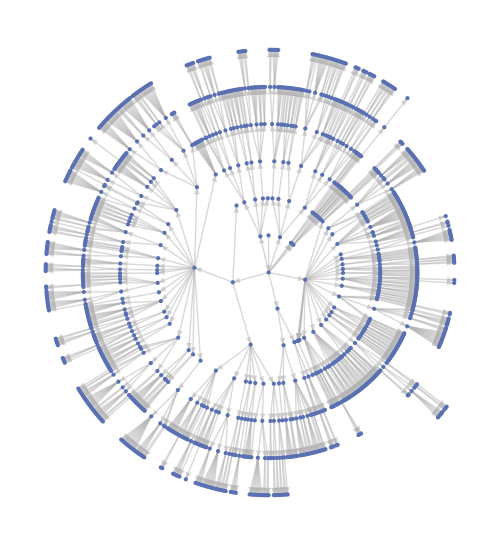

```mathematica
AmmonitesPhylogeny1=Cases[AmmonitesPhylogeny/.x_String:>ToLowerCase@x,{__,Alternatives@@Union@ToLowerCase@Join[ToLowerCase@MC[[2;;,1]],ToLowerCase@SA[[;;,2]]],__}];
AmmonitesPhylogeny2=Cases[AmmonitesPhylogeny,{Alternatives@@AmmonitesPhylogeny1[[;;,-1]],___}];
AmmonitesPhylogeny3=Cases[AmmonitesPhylogeny,{Alternatives@@AmmonitesPhylogeny2[[;;,-1]],___}];
AmmonitesPhylogeny4=Cases[AmmonitesPhylogeny,{Alternatives@@AmmonitesPhylogeny3[[;;,-1]],___}];
AmmonitesPhylogeny5=Cases[AmmonitesPhylogeny,{Alternatives@@AmmonitesPhylogeny4[[;;,-1]],___}];
AmmonitesPhylogeny6=Cases[AmmonitesPhylogeny,{Alternatives@@AmmonitesPhylogeny5[[;;,-1]],___}];
AmmonitesPhylogeny7=Cases[AmmonitesPhylogeny,{Alternatives@@AmmonitesPhylogeny6[[;;,-1]],___}];
AmmonitesPhylogenyUnion=(Union@@ToExpression["AmmonitesPhylogeny"<>ToString[#]&/@Range@7]);
AmmonitesTree=Graph[(Rule@@@#[[;;,{-1,1}]])]&@AmmonitesPhylogenyUnion;
Row[{
TreePlot[
Graph[
Rule@@@#[[;;,{-1,1}]],VertexStyle->(#[[1]]->(#[[2]]/.{"subclass"->RGBColor[0.368417, 0.506779, 0.709798],"order"->RGBColor[0.880722, 0.611041, 0.142051],"suborder"->RGBColor[0.560181, 0.691569, 0.194885],"superfamily"->RGBColor[0.922526, 0.385626, 0.209179],"family"->RGBColor[0.528488, 0.470624, 0.701351],"subfamily"->RGBColor[0.772079, 0.431554, 0.102387],"genus"->RGBColor[0.363898, 0.618501, 0.782349]})&/@#[[;;,{1,2}]]),VertexSize->1,EdgeStyle->GrayLevel[.7]]&@AmmonitesPhylogenyUnion,Center,ImageSize->500],SwatchLegend[{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349]},{"subclass","order","suborder","superfamily","family","subfamily","genus"}]},
Spacer[10]]
```

### Preparing the data to comply with the PollyPhylogenetics6 .2 package (basically inverting the tree and collapsing sub and super clades which are not represented in the datasets)

```mathematica
PhyloPath[x_]:=Quiet@Module[{p},
p[1]=x;
p[2]=Cases[AmmonitesPhylogeny2,{p[1][[-1]],__}][[1]];
p[3]=Cases[AmmonitesPhylogeny3,{p[2][[-1]],__}][[1]];
p[4]=Cases[AmmonitesPhylogeny4,{p[3][[-1]],__}][[1]];
p[5]=Cases[AmmonitesPhylogeny5,{p[4][[-1]],__}][[1]];
p[6]=Cases[AmmonitesPhylogeny6,{p[5][[-1]],__}][[1]];
p[7]=Cases[AmmonitesPhylogeny7,{p[6][[-1]],__}][[1]];
DeleteCases[#,{_,"suborder"|"superfamily"|"subfamily",__}]//.Flatten[Cases[#,{z_,"suborder"|"superfamily"|"subfamily",_,y_}:>(z->y)]]&@(TakeWhile[Table[p[i],{i,1,7}],ListQ[#]&])]
```

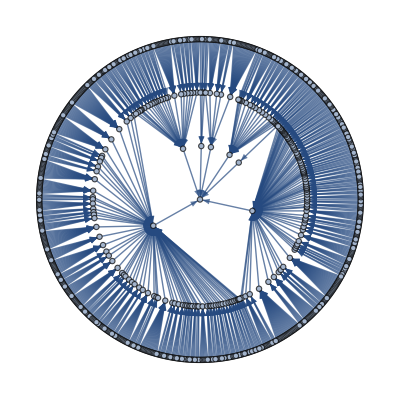

```mathematica
TreePlot[Graph[Rule@@@Union@@(Partition[#,2,1]&/@Select[PhyloPath/@AmmonitesPhylogeny1,Length@#==4&][[;;,;;,3]])],Center]
```

```mathematica
myTableAmmonites=Prepend[
Union[{#[[1]],#[[-1]],1,#[[2]]/."genus"->1/.(_String->0)}&/@(Union@@Select[PhyloPath/@AmmonitesPhylogeny1,Length@#==4&])/.(12315)->"Node 0"],
{"Descendant","Ancestor","Branch Length","Tip?"}];
DWtraits=Dispatch[#[[1]]->#[[2;;]]&/@Join[MC[[2;;,{1,6,5}]],SA[[2;;,{2,4,5}]]]/.x_String->ToLowerCase[x]];
DWtraitsAssociation=Association[#[[1]]->#[[3]]&/@AmmonitesPhylogeny1/.DWtraits];
```

#### Calculating the PICs

```mathematica
PICs=N@IndependentContrasts[myTableAmmonites,{#,t[#]}&/@Cases[myTableAmmonites,{x_,_,_,1}:>x]]/.t[x_]->t[Round[x]];
```

#### PICs are preserved after SibSwaping at the genus level

```mathematica
SibSwapPics:=Association@(Join@@(Thread[#[[;;,1]]->(RandomSample/@(#[[;;,2]]ᵀ))ᵀ]&/@Map[{#,DWtraitsAssociation@#}&,GatherBy[Cases[myTableAmmonites,{x_,__,1}],#[[2]]&][[;;,;;,1]],{2}]));
```

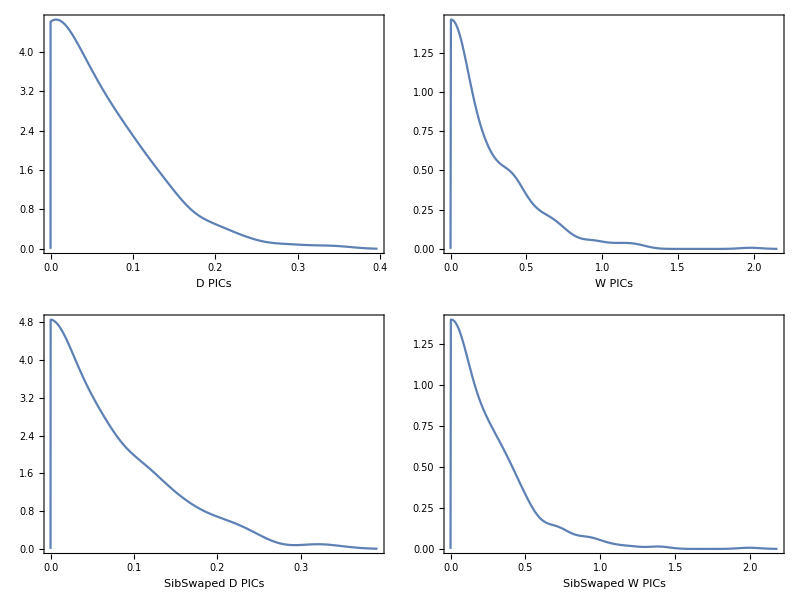

```mathematica
Grid@{SmoothHistogram[#[[1]],PlotRange->{{0,All},All},Frame->True,FrameLabel->{#[[2]],None}]&/@({((PICs/.t->DWtraitsAssociation)ᵀ),{"D PICs","W PICs"}}ᵀ),
SmoothHistogram[#[[1]],PlotRange->{{0,All},All},Frame->True,FrameLabel->{#[[2]],None}]&/@({((PICs/.t->SibSwapPics)ᵀ),{"SibSwaped D PICs","SibSwaped W PICs"}}ᵀ)}
```